# EMRI in (Spherical) Bosonic Cloud

In this notebook, we present the derivations and some methods for solving the equations presented in the notes, which model an circular extreme-mass-ratio inspiral evolving in ultralight scalar environment.

```mathematica
Quit[]
```

### Simplifications rules for Y(θ,ϕ)

We start by defining some useful rules about spherical harmonics for substitution in the equations of motion.

```mathematica
rulesY={Derivative[2,0][Y][θ,ϕ]->-ℓ(ℓ+1)Y[θ,ϕ]-1/Sin[θ]^2 Derivative[0,2][Y][θ,ϕ]-Cot[θ]Derivative[1,0][Y][θ,ϕ],Derivative[3,0][Y][θ,ϕ]->ℓ (1+ℓ) Cot[θ] Y[θ,ϕ]-(1+ℓ+ℓ^2) Derivative[1,0][Y][θ,ϕ]+Csc[θ]^2 (3 Cot[θ] Derivative[0,2][Y][θ,ϕ]+2 Derivative[1,0][Y][θ,ϕ]-Derivative[1,2][Y][θ,ϕ]),Derivative[4,0][Y][θ,ϕ]->ℓ (1+ℓ) (1+ℓ+ℓ^2-3 Csc[θ]^2) Y[θ,ϕ]+Csc[θ] (Csc[θ] (7+ℓ+ℓ^2-11 Csc[θ]^2) Derivative[0,2][Y][θ,ϕ]+((1+2 ℓ (1+ℓ)) Cos[θ]-6 Cot[θ] Csc[θ]) Derivative[1,0][Y][θ,ϕ]+Csc[θ] (5 Cot[θ] Derivative[1,2][Y][θ,ϕ]-Derivative[2,2][Y][θ,ϕ])),Derivative[2,1][Y][θ,ϕ]->-ℓ (1+ℓ) Derivative[0,1][Y][θ,ϕ]-Csc[θ]^2 Derivative[0,3][Y][θ,ϕ]-Cot[θ] Derivative[1,1][Y][θ,ϕ],Derivative[2,2][Y][θ,ϕ]->-ℓ (1+ℓ) Derivative[0,2][Y][θ,ϕ]-Csc[θ]^2 Derivative[0,4][Y][θ,ϕ]-Cot[θ] Derivative[1,2][Y][θ,ϕ]};

rulesY2={Derivative[1,1][Y][θ,ϕ]->1/2 X[θ,ϕ]+Cot[θ] Derivative[0,1][Y][θ,ϕ],Derivative[0,2][Y][θ,ϕ]->-1/2 Sin[θ] (Sin[θ] (W[θ,ϕ]+ℓ (1+ℓ) Y[θ,ϕ])+2 Cos[θ] Derivative[1,0][Y][θ,ϕ]),Derivative[2,0][Y][θ,ϕ]->1/2 (W[θ,ϕ]-ℓ (1+ℓ) Y[θ,ϕ]),Derivative[3,0][Y][θ,ϕ]->1/2 (-3 Cot[θ] W[θ,ϕ]-ℓ (1+ℓ) Cot[θ] Y[θ,ϕ]-2 (-2+ℓ+ℓ^2+Csc[θ]^2) Derivative[1,0][Y][θ,ϕ]-2 Csc[θ]^2 Derivative[1,2][Y][θ,ϕ]),Derivative[4,0][Y][θ,ϕ]->1/2 (-(7+2 ℓ (1+ℓ)-11 Csc[θ]^2) W[θ,ϕ]+2 Csc[θ]^4 Derivative[0,4][Y][θ,ϕ]+Cot[θ] (5 ℓ (1+ℓ) Cot[θ] Y[θ,ϕ]+2 (-6+5 Csc[θ]^2) Derivative[1,0][Y][θ,ϕ]+12 Csc[θ]^2 Derivative[1,2][Y][θ,ϕ])),Derivative[2,1][Y][θ,ϕ]->-1/2 Cot[θ] X[θ,ϕ]-(ℓ+ℓ^2+Cot[θ]^2) Derivative[0,1][Y][θ,ϕ]-Csc[θ]^2 Derivative[0,3][Y][θ,ϕ],Derivative[2,2][Y][θ,ϕ]->-Csc[θ]^2 Derivative[0,4][Y][θ,ϕ]+1/2 ℓ (1+ℓ) Sin[θ] (Sin[θ] (W[θ,ϕ]+ℓ (1+ℓ) Y[θ,ϕ])+2 Cos[θ] Derivative[1,0][Y][θ,ϕ])-Cot[θ] Derivative[1,2][Y][θ,ϕ],Derivative[3,1][Y][θ,ϕ]->1/4 (-2 (1+ℓ+ℓ^2-2 Csc[θ]^2) X[θ,ϕ]+Csc[θ]^3 ((7 Cos[θ]+Cos[3 θ]) Derivative[0,1][Y][θ,ϕ]+12 Cos[θ] Derivative[0,3][Y][θ,ϕ]-4 Sin[θ] Derivative[1,3][Y][θ,ϕ]))};

rulesXW={X[θ,ϕ]->2D[D[Y[θ,ϕ],θ],ϕ]-2D[Cot[θ]Y[θ,ϕ],ϕ],Derivative[1,0][X][θ,ϕ]->D[2D[D[Y[θ,ϕ],θ],ϕ]-2D[Cot[θ]Y[θ,ϕ],ϕ],θ],Derivative[0,1][X][θ,ϕ]->D[2D[D[Y[θ,ϕ],θ],ϕ]-2D[Cot[θ]Y[θ,ϕ],ϕ],ϕ],Derivative[1,1][X][θ,ϕ]->D[D[2D[D[Y[θ,ϕ],θ],ϕ]-2D[Cot[θ]Y[θ,ϕ],ϕ],ϕ],θ],
W[θ,ϕ]->D[Y[θ,ϕ],{θ,2}]-Cot[θ]D[Y[θ,ϕ],θ]-1/Sin[θ]^2 D[Y[θ,ϕ],{ϕ,2}],
Derivative[1,0][W][θ,ϕ]->D[D[Y[θ,ϕ],{θ,2}]-Cot[θ]D[Y[θ,ϕ],θ]-1/Sin[θ]^2 D[Y[θ,ϕ],{ϕ,2}],θ],Derivative[1,1][W][θ,ϕ]->D[D[D[Y[θ,ϕ],{θ,2}]-Cot[θ]D[Y[θ,ϕ],θ]-1/Sin[θ]^2 D[Y[θ,ϕ],{ϕ,2}],θ],ϕ],Derivative[0,1][W][θ,ϕ]->D[D[Y[θ,ϕ],{θ,2}]-Cot[θ]D[Y[θ,ϕ],θ]-1/Sin[θ]^2 D[Y[θ,ϕ],{ϕ,2}],ϕ]};
```

### Einstein-Klein-Gordon system

We now define the (generic) equations of motion we will want to solve.

### Geometric quantities

Definitions of the Chistofell symbols , Riemann tensor  , Ricci tensor   and Ricci Scalar as in Gravity from Robert Wald

```mathematica
Chr[metric_,Ig_,y_]:=Block[{ϵ,𝒶0,l1,l2,l3,l4,dim = Length[y],Christoffel},

Christoffel = Table[Sum[Ig[[l1,l4]]D[metric[[l2,l4]],y[[l3]]],{l4,1,dim}],{l1,1,dim},{l2,1,dim},{l3,1,dim}]
+Table[Sum[Ig[[l1,l4]]D[metric[[l4,l3]],y[[l2]]],{l4,1,dim}],{l1,1,dim},{l2,1,dim},{l3,1,dim}]
-Table[Sum[Ig[[l1,l4]]D[metric[[l2,l3]],y[[l4]]],{l4,1,dim}],{l1,1,dim},{l2,1,dim},{l3,1,dim}];

	Return[Collect[Series[Christoffel/2,{ϵ,0,1}],ϵ,Simplify]];

]
```

```mathematica
Riemann[metric_,y_,Christoffel_]:=Block[{ϵ,l1,l2,l3,l4,l5,dim = Length[y],Riem},
		
	Riem = Table[D[Christoffel[[l1]][[l2,l4]],y[[l3]]],{l1,1,dim},{l2,1,dim},{l3,1,dim},{l4,1,dim}]
			-Table[D[Christoffel[[l1]][[l2,l3]],y[[l4]]],{l1,1,dim},{l2,1,dim},{l3,1,dim},{l4,1,dim}]
			-Table[Sum[Christoffel[[l1]][[l5,l4]]Christoffel[[l5]][[l2,l3]],{l5,1,dim}],{l1,1,dim},{l2,1,dim},{l3,1,dim},{l4,1,dim}]
			+Table[Sum[Christoffel[[l1]][[l5,l3]]Christoffel[[l5]][[l2,l4]],{l5,1,dim}],{l1,1,dim},{l2,1,dim},{l3,1,dim},{l4,1,dim}]; 

	Return[Collect[Series[Riem,{ϵ,0,1}],ϵ,Simplify]];

]
```

```mathematica
Ricci[Riem_]:=Block[{l1,l2,l3,dim = Dimensions[Riem][[1]],RicciTensor},

RicciTensor = Table[Sum[Riem[[l3,l1,l3,l2]],{l3,dim}],{l1,dim},{l2,dim}];

Return[Collect[Series[RicciTensor,{ϵ,0,1}],ϵ,Simplify]];

]
```

```mathematica
RicciScalar[Ig_,RicciTensor_]:=Block[{l1,l2,dim = Dimensions[RicciTensor][[1]],RicciScal},

RicciScal = Sum[Ig[[l1,l2]]RicciTensor[[l1,l2]],{l1,1,dim},{l2,1,dim}];

Return[Collect[Series[RicciScal,{ϵ,0,1}],ϵ,Simplify]];

]
```

### Tensor harmonic decomposition

Definitions of the 10 spherical harmonics that expand any symmetric rank-2 tensor into irreducible representations of SO(2) in spherically-symmetric backgrounds. These definitions are the same used in Sago et al., Gauge problem in the gravitational self-force: Harmonic gauge approach in the Schwarzschild background, Phys. Rev. D 67, 104017 (2003) (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.67.104017). As explained in the notes, we can group them into polar/electric/even or axial/magnetic/odd depending on their behavior under parity transformations (θ, φ) → (π − θ, π + φ) (I wrote in front of them their type)

```mathematica
{Sθ[θ_,ϕ_],Sϕ[θ_,ϕ_]}={-D[Y[θ,ϕ],ϕ]/Sin[θ],D[Y[θ,ϕ],θ]Sin[θ]};
```

```mathematica
a0={{Y[θ,ϕ],0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}; (*polar*)
a1=I/Sqrt[2]{{0,Y[θ,ϕ],0,0},{Y[θ,ϕ],0,0,0},{0,0,0,0},{0,0,0,0}};(*polar*)
a={{0,0,0,0},{0,Y[θ,ϕ],0,0},{0,0,0,0},{0,0,0,0}};(*polar*)
b0=(I r)/(2ℓ(ℓ+1))^(1/2){{0,0,D[Y[θ,ϕ],θ],D[Y[θ,ϕ],ϕ]},{0,0,0,0},{D[Y[θ,ϕ],θ],0,0,0},{D[Y[θ,ϕ],ϕ],0,0,0}};(*polar*)
b=r/(2ℓ(ℓ+1))^(1/2){{0,0,0,0},{0,0,D[Y[θ,ϕ],θ],D[Y[θ,ϕ],ϕ]},{0,D[Y[θ,ϕ],θ],0,0},{0,D[Y[θ,ϕ],ϕ],0,0}};(*polar*)
c0=r/(2ℓ(ℓ+1))^(1/2){{0,0,Sθ[θ,ϕ],Sϕ[θ,ϕ]},{0,0,0,0},{Sθ[θ,ϕ],0,0,0},{Sϕ[θ,ϕ],0,0,0}};(*axial*)
c=(I r)/(2ℓ(ℓ+1))^(1/2){{0,0,0,0},{0,0,Sθ[θ,ϕ],Sϕ[θ,ϕ]},{0,Sθ[θ,ϕ],0,0},{0,Sϕ[θ,ϕ],0,0}};(*axial*)
d=-(I r^2)/(2ℓ(ℓ+1)(ℓ-1)(ℓ+2))^(1/2){{0,0,0,0},{0,0,0,0},{0,0,-X[θ,ϕ]/Sin[θ],Sin[θ]W[θ,ϕ]},
{0,0,Sin[θ]W[θ,ϕ],Sin[θ]X[θ,ϕ]}};(*axial*)
g=r^2/Sqrt[2]{{0,0,0,0},{0,0,0,0},{0,0,Y[θ,ϕ],0},{0,0,0,Sin[θ]^2 Y[θ,ϕ]}}; (*polar*)
𝒻=r^2/(2ℓ(ℓ+1)(ℓ-1)(ℓ+2))^(1/2){{0,0,0,0},{0,0,0,0},{0,0,W[θ,ϕ],X[θ,ϕ]},{0,0,X[θ,ϕ],-Sin[θ]^2 W[θ,ϕ]}};(*polar*)
```

Note for ℓ = 0 and ℓ = 1 some of the normalization coefficients above diverge. This happens because in these cases these spherical harmonics are identically 0.

### Metric and Scalar perturbations

We now want to define our set of perturbations. exp[F] is a function to expand any expression up to first-order in some parameter ϵ, which in our case will be the mass-ratio

```mathematica
exp[F_]:=Normal[Series[F,{ϵ,0,1}]];
```

ℊ0 is a generic spherically-symmetric background spacetime. In our example we will focus on polar perturbations only, because those dominate energy emission (at least for circular motion) and are more technically involved (so if you can learn how to solve them, you can do the axial sector by yourself). As mentioned in the notes,  gauge freedom in GR allows us to set some coefficients of the metric perturbations to 0. Here,  we adopt the Regge-Wheeler gauge, and work directly in the frequency-domain. For  ℓ = 1, we can further set K = 0

```mathematica
x={t,r,θ,ϕ};
ℊ0={{-F[r],0,0,0},{0,1/B[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
hpol={{F[r]H0[r],H1[r],0,0},{H1[r],H2[r]/B[r],0,0},{0,0,r^2 K[r],0},{0,0,0,r^2 K[r] Sin[θ]^2}}Y[θ,ϕ]Exp[-I σ t];
```

```mathematica
ℊ=Collect[exp[ℊ0+ϵ hpol],ϵ,Simplify];
ℊℐ=exp[Inverse[ℊ]];
dg=exp[-Det[ℊ]];
```

Now compute the geometric quantities defined above and also the Einstein tensor

```mathematica
Γ=Chr[ℊ,ℊℐ,x]; (* (-- Subscript[Γ^μ, αβ]_-- *)
```

```mathematica
Riemupdn=Riemann[ℊ,x,Γ];
```

```mathematica
RTdndn=Ricci[Riemupdn]; (* -- Subscript[R, αβ]-- *)
```

```mathematica
R=RicciScalar[ℊℐ,RTdndn]; (* -- R_-- *)
```

```mathematica
G=Collect[exp[RTdndn-exp[1/2 ℊ R]],ϵ,Simplify];(* Einstein -- Subscript[𝒢, αβ]_= Subscript[R, αβ]-1/2 Subscript[g, αβ] R -- *)
```

Define the energy-momentum tensor of the particle and the scalar field where use the expansions for  .

```mathematica
Tparticle=ϵ  mp(𝒜0[r]a0+𝒜[r]a+𝒜1[r]a1+ℬ0[r]b0+ℬ[r]b+𝒬0[r]c0+𝒬[r]c+𝒟[r]d+ℱ[r]𝒻+𝒢[r]g)Exp[-I σ t];(* -- Subscript[T, αβ] of the secondary -- *)
```

```mathematica
Tscalar=exp[Table[Table[1/2(D[(Ψ0[r]+ϵ δΨm[r]/r Exp[-ⅈ σ t]Y[θ,ϕ])Exp[ⅈ ω t],x[[l1]]]*D[(Ψ0[r]+ϵ δΨp[r]/r Exp[-ⅈ σ t]Y[θ,ϕ])Exp[-ⅈ ω t],x[[l2]]]+D[(Ψ0[r]+ϵ δΨm[r]/r Exp[-ⅈ σ t]Y[θ,ϕ])Exp[ⅈ ω t],x[[l2]]]*D[(Ψ0[r]+ϵ δΨp[r]/r Exp[-ⅈ σ t]Y[θ,ϕ])Exp[-ⅈ ω t],x[[l1]]])-1/2 ℊ[[l1,l2]](Sum[Sum[ℊℐ[[l3,l4]]D[(Ψ0[r]+ϵ δΨm[r]/r Exp[-ⅈ σ t]Y[θ,ϕ])Exp[ⅈ ω t],x[[l3]]]*D[(Ψ0[r]+ϵ δΨp[r]/r Exp[-ⅈ σ t]Y[θ,ϕ])Exp[-ⅈ ω t],x[[l4]]],{l3,1,Length[x]}],{l4,1,Length[x]}]+(V0[r]+ϵ δV[r]Exp[-ⅈ σ t]Y[θ,ϕ])),{l1,1,Length[x]}],{l2,1,Length[x]}]]//FullSimplify;(* -- Subscript[T, αβ] of the scalar field -- *)
```

We separate the 0th and 1st order components for convenience and also define some contractions (some of which we end up not using...).

```mathematica
Tscalarback=Coefficient[Tscalar,ϵ,0]/.rulesY/.rulesY2//FullSimplify;
δTscalar=Assuming[F[r]>0&&B[r]>0,Coefficient[Tscalar,ϵ,1]];
```

```mathematica
Tscalarupdwn=exp[TensorContract[ℊℐ⊗Tscalar,{2,3}]];
```

```mathematica
Tscalarupup=exp[TensorContract[ℊℐ⊗ℊℐ⊗Tscalar,{{2,5},{4,6}}]];
```

```mathematica
Tparticleupup=exp[TensorContract[ℊℐ⊗ℊℐ⊗Tparticle,{{2,5},{4,6}}]];
```

```mathematica
Gupup=exp[TensorContract[ℊℐ⊗ℊℐ⊗G,{{2,5},{4,6}}]];
```

```mathematica
ℰ=G-8π (Tscalar+Tparticle);
```

```mathematica
Coefficient[Tscalarupdwn,ϵ,0]//MatrixForm
```

(-(ω^2 Ψ0[r]^2+F[r] (V0[r]+B[r] Ψ0'[r]^2))/(2 F[r]) | 0 | 0 | 0
0 | (ω^2 Ψ0[r]^2+F[r] (-V0[r]+B[r] Ψ0'[r]^2))/(2 F[r]) | 0 | 0
0 | 0 | (-F[r] V0[r]+ω^2 Ψ0[r]^2-B[r] F[r] Ψ0'[r]^2)/(2 F[r]) | 0
0 | 0 | 0 | (-F[r] V0[r]+ω^2 Ψ0[r]^2-B[r] F[r] Ψ0'[r]^2)/(2 F[r]))

For circular motion the coefficients below that appear in the energy-momentum tensor of the particle are 0, so let us just set them already to make the equations shorter.

```mathematica
𝒜[r_]=𝒜1[r_]=ℬ[r_]=𝒬[r_]=0;
```

Define also the Klein-Gordon and treat Ψ and Ψ* as indepedent variables

```mathematica
KGPlus=exp[1/Sqrt[dg] Sum[D[Sqrt[dg]Sum[ℊℐ[[l1,l2]]D[(Ψ0[r]+ϵ δΨp[r]/r Exp[-ⅈ σ t]Y[θ,ϕ])Exp[-ⅈ ω t],x[[l1]]] ,{l1,1,4}],x[[l2]]],{l2,1,4}]-(U0[r]+ϵ δU[r]Exp[-ⅈ σ t]Y[θ,ϕ])(Ψ0[r]Exp[-ⅈ ω t]+ϵ δΨp[r]/r Exp[-ⅈ σ t]Exp[-ⅈ ω t]Y[θ,ϕ])]//.Join[rulesY2];
```

```mathematica
KGMin=exp[1/Sqrt[dg] Sum[D[Sqrt[dg]Sum[ℊℐ[[l1,l2]]D[(Ψ0[r]+ϵ δΨm[r]/r Exp[-ⅈ σ t]Y[θ,ϕ])Exp[ⅈ ω t],x[[l1]]] ,{l1,1,4}],x[[l2]]],{l2,1,4}]-(U0[r]+ϵ δU[r]Exp[-ⅈ σ t]Y[θ,ϕ])(Ψ0[r]Exp[ⅈ ω t]+ϵ δΨm[r]/r Exp[-ⅈ σ t]Exp[ⅈ ω t]Y[θ,ϕ])]//.Join[rulesY2];
```

Separate 0th and 1st order terms in the Klein-Gordon equation also

```mathematica
KGbar=Coefficient[KGPlus,ϵ,0]/.rulesY/.rulesY2//FullSimplify;
δKGPlus=Coefficient[KGPlus,ϵ,1]/.rulesY/.rulesY2//FullSimplify;
δKGMin=Coefficient[KGMin,ϵ,1]/.rulesY/.rulesY2//FullSimplify;
```

Save the equations a file

```mathematica
Export["./src/fields_equations_polar.mx",{ℰ,KGbar+δKGPlus,KGbar+δKGMin}]
```

./src/fields_equations_polar.mx

### Decoupling Background and Perturbations

We will now do several manipulations in the field equations

#### Background

You can use the 0th order equations to substitute the derivatives of the background functions (both for the metric and scalar field) in the 1st order equations. However, you need to be careful if you then use some approximation, as we will do. In that case, I suggest that you don’t replace them because you can quickly run into inconsistencies (speaking from experience).

```mathematica
ℰback=Coefficient[ℰ,ϵ,0];
```

```mathematica
soldF=Solve[ℰback[[2,2]]==0,F'[r]][[1,1,2]]
```

(F[r]-B[r] F[r]-4 π r^2 F[r] V0[r]+4 π r^2 ω^2 Φ0[r]^2+4 π r^2 B[r] F[r] Φ0'[r]^2)/(r B[r])

```mathematica
soldF
```

(F[r]-B[r] F[r]-4 π r^2 F[r] V0[r]+4 π r^2 ω^2 Φ0[r]^2+4 π r^2 B[r] F[r] Φ0'[r]^2)/(r B[r])

```mathematica
Simplify[ℰback[[1,1]]]
```

-4 π ω^2 Φ0[r]^2-(F[r] (-1+B[r]+4 π r^2 V0[r]+r B'[r]+4 π r^2 B[r] Φ0'[r]^2))/r^2

```mathematica
soldB=Solve[ℰback[[1,1]]==0,B'[r]][[1,1,2]]
```

(F[r]-B[r] F[r]-4 π r^2 F[r] V0[r]-4 π r^2 ω^2 Φ0[r]^2-4 π r^2 B[r] F[r] Φ0'[r]^2)/(r F[r])

```mathematica
KGbar
```

(ⅇ^(-ⅈ t ω) (2 r (ω^2-F[r] U0[r]) Φ0[r]+(r F[r] B'[r]+B[r] (4 F[r]+r F'[r])) Φ0'[r]+2 r B[r] F[r] Φ0''[r]))/(2 r F[r])

```mathematica
solddΦ0=Solve[KGbar==0,Φ0''[r]][[1,1,2]]
```

(-2 r ω^2 Φ0[r]+2 r F[r] U0[r] Φ0[r]-4 B[r] F[r] Φ0'[r]-r F[r] B'[r] Φ0'[r]-r B[r] F'[r] Φ0'[r])/(2 r B[r] F[r])

#### Isolate linear order terms in field’s equation

```mathematica
var={H1''[r],H1'[r],H1[r],H2''[r],H2'[r],H2[r],H0''[r],H0'[r],H0[r],K''[r],K'[r],K[r],𝒟[r],𝒬[r],𝒬0[r],δΨp[r],δΨp'[r],δΨp''[r],δΨm[r],δΨm'[r],δΨm''[r]};

varP={X[θ,ϕ],W[θ,ϕ],Y[θ,ϕ],Derivative[1,0][Y][θ,ϕ],Derivative[0,1][Y][θ,ϕ]};
```

```mathematica
rulesbackground={};
```

```mathematica
eqtt=Collect[ⅇ^(ⅈ t σ)Coefficient[ℰ[[1,1]],ϵ,1]//.Join[rulesY2,rulesbackground],Join[varP,var],FullSimplify];
```

```mathematica
eqrr=Collect[ⅇ^(ⅈ t σ)Coefficient[ℰ[[2,2]],ϵ,1]//.Join[rulesY2,rulesbackground],Join[varP,var],FullSimplify];
```

```mathematica
eqθθ=Collect[ⅇ^(ⅈ t σ)Coefficient[ℰ[[3,3]],ϵ,1]//.Join[rulesY2,rulesbackground],Join[varP,var],FullSimplify];
```

```mathematica
eqϕϕ=Collect[ⅇ^(ⅈ t σ)Coefficient[ℰ[[4,4]],ϵ,1]//.Join[rulesY2,rulesbackground],Join[varP,var],FullSimplify];
```

```mathematica
eqtr=Collect[ⅇ^(ⅈ t σ)Coefficient[ℰ[[1,2]],ϵ,1]//.Join[rulesY2,rulesbackground],Join[varP,var],FullSimplify];
```

```mathematica
eqtθ=Collect[ⅇ^(ⅈ t σ)Coefficient[ℰ[[1,3]],ϵ,1]//.Join[rulesY2,rulesbackground],Join[varP,var],FullSimplify];
```

```mathematica
eqtϕ=Collect[ⅇ^(ⅈ t σ)Coefficient[ℰ[[1,4]],ϵ,1]//.Join[rulesY2,rulesbackground],Join[varP,var],FullSimplify];
```

```mathematica
eqrθ=Collect[ⅇ^(ⅈ t σ)Coefficient[ℰ[[2,3]],ϵ,1]//.Join[rulesY2,rulesbackground],Join[varP,var],FullSimplify];
```

```mathematica
eqrϕ=Collect[ⅇ^(ⅈ t σ)Coefficient[ℰ[[2,4]],ϵ,1]//.Join[rulesY2,rulesbackground],Join[varP,var],FullSimplify];
```

```mathematica
eqθϕ=Collect[ⅇ^(ⅈ t σ)Coefficient[ℰ[[3,4]],ϵ,1]//.Join[rulesY2,rulesbackground],Join[varP,var],FullSimplify];
```

```mathematica
δKGPlus=Coefficient[KGPlus,ϵ,1]/.rulesY/.rulesY2//FullSimplify;
δKGMin=Coefficient[KGMin,ϵ,1]/.rulesY/.rulesY2//FullSimplify;
```

```mathematica
Collect[eqtt,Join[varP,var],FullSimplify]
Collect[eqrr,Join[varP,var],FullSimplify]
Collect[eqθθ,Join[varP,var],FullSimplify]
Collect[eqϕϕ/Sin[θ]^2,Join[varP,var],FullSimplify]

Collect[eqtr,Join[varP,var],FullSimplify]
Collect[eqtθ,Join[varP,var],FullSimplify]
Collect[eqtϕ,Join[varP,var],FullSimplify]

Collect[eqrθ,Join[varP,var],FullSimplify]
Collect[eqrϕ,Join[varP,var],FullSimplify]

Collect[eqθϕ,Join[varP,var],FullSimplify]
```

Y[θ,ϕ] (((-2+ℓ+ℓ^2) F[r] K[r])/(2 r^2)-4 π (2 mp 𝒜0[r]+F[r] δV[r])+(B[r] F[r] H2'[r])/r-(F[r] (6 B[r]+r B'[r]) K'[r])/(2 r)-(4 π B[r] F[r] δΨm'[r] Ψ0'[r])/r-(4 π B[r] F[r] δΨp'[r] Ψ0'[r])/r+(4 π δΨm[r] (r (σ-ω) ω Ψ0[r]+B[r] F[r] Ψ0'[r]))/r^2+(δΨp[r] (-4 π r ω (σ+ω) Ψ0[r]+4 π B[r] F[r] Ψ0'[r]))/r^2+(F[r] H0[r] (-1+r (4 π r V0[r]+B'[r])+B[r] (1+4 π r^2 Ψ0'[r]^2)))/r^2+(F[r] H2[r] (ℓ+ℓ^2+2 r B'[r]+B[r] (2+8 π r^2 Ψ0'[r]^2)))/(2 r^2)-B[r] F[r] K''[r])

Y[θ,ϕ] (-(2 ⅈ σ H1[r])/(r F[r])+((-(-2+ℓ+ℓ^2)/r^2+(2 σ^2)/F[r]) K[r])/(2 B[r])+(4 π δV[r])/B[r]+(H0[r] ((ℓ (1+ℓ))/r^2-(8 π ω^2 Ψ0[r]^2)/F[r]))/(2 B[r])-(H2[r] (1/r^2-4 π V0[r]+(4 π ω^2 Ψ0[r]^2)/F[r]))/B[r]-H0'[r]/r+(1/r+F'[r]/(2 F[r])) K'[r]-(4 π δΨm'[r] Ψ0'[r])/r-(4 π δΨp'[r] Ψ0'[r])/r+(4 π δΨp[r] (-(r ω (σ+ω) Ψ0[r])/(B[r] F[r])+Ψ0'[r]))/r^2+(4 π δΨm[r] (r (σ-ω) ω Ψ0[r]+B[r] F[r] Ψ0'[r]))/(r^2 B[r] F[r]))

-(4 ⅈ √2 mp π r^2 Csc[θ] X[θ,ϕ] 𝒟[r])/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))+W[θ,ϕ] (H0[r]/4-H2[r]/4-(4 √2 mp π r^2 ℱ[r])/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ))))+Y[θ,ϕ] (4 π r^2 (-√2 mp 𝒢[r]+δV[r])+H0[r] (1/4 ℓ (1+ℓ)-(4 π r^2 ω^2 Ψ0[r]^2)/F[r])-(ⅈ r σ H1[r] (2 B[r]+r B'[r]))/(2 F[r])-(r (r F[r] B'[r]+2 B[r] (F[r]+r F'[r])) H0'[r])/(4 F[r])-(ⅈ r^2 σ B[r] H1'[r])/F[r]-(r B[r] (2 F[r]+r F'[r]) H2'[r])/(4 F[r])+(r (r F[r] B'[r]+B[r] (4 F[r]+r F'[r])) K'[r])/(4 F[r])+4 π r B[r] δΨm'[r] Ψ0'[r]+4 π r B[r] δΨp'[r] Ψ0'[r]-(4 π δΨm[r] (r ω (-σ+ω) Ψ0[r]+B[r] F[r] Ψ0'[r]))/F[r]-(4 π δΨp[r] (r ω (σ+ω) Ψ0[r]+B[r] F[r] Ψ0'[r]))/F[r]+(r K[r] (-r B[r] F'[r]^2+2 F[r]^2 (B'[r]+8 π r (V0[r]+B[r] Ψ0'[r]^2))+F[r] (2 r σ^2-16 π r ω^2 Ψ0[r]^2+(2 B[r]+r B'[r]) F'[r]+2 r B[r] F''[r])))/(4 F[r]^2)+(H2[r] (r^2 B[r] F'[r]^2-F[r]^2 (ℓ (1+ℓ)+2 r (B'[r]+8 π r B[r] Ψ0'[r]^2))+r F[r] (2 r σ^2-r B'[r] F'[r]-2 B[r] (F'[r]+r F''[r]))))/(4 F[r]^2)-1/2 r^2 B[r] H0''[r]+1/2 r^2 B[r] K''[r])

(4 ⅈ √2 mp π r^2 Csc[θ] X[θ,ϕ] 𝒟[r])/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))+W[θ,ϕ] (-H0[r]/4+H2[r]/4+(4 √2 mp π r^2 ℱ[r])/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ))))+Y[θ,ϕ] (4 π r^2 (-√2 mp 𝒢[r]+δV[r])+H0[r] (1/4 ℓ (1+ℓ)-(4 π r^2 ω^2 Ψ0[r]^2)/F[r])-(ⅈ r σ H1[r] (2 B[r]+r B'[r]))/(2 F[r])-(r (r F[r] B'[r]+2 B[r] (F[r]+r F'[r])) H0'[r])/(4 F[r])-(ⅈ r^2 σ B[r] H1'[r])/F[r]-(r B[r] (2 F[r]+r F'[r]) H2'[r])/(4 F[r])+(r (r F[r] B'[r]+B[r] (4 F[r]+r F'[r])) K'[r])/(4 F[r])+4 π r B[r] δΨm'[r] Ψ0'[r]+4 π r B[r] δΨp'[r] Ψ0'[r]-(4 π δΨm[r] (r ω (-σ+ω) Ψ0[r]+B[r] F[r] Ψ0'[r]))/F[r]-(4 π δΨp[r] (r ω (σ+ω) Ψ0[r]+B[r] F[r] Ψ0'[r]))/F[r]+(r K[r] (-r B[r] F'[r]^2+2 F[r]^2 (B'[r]+8 π r (V0[r]+B[r] Ψ0'[r]^2))+F[r] (2 r σ^2-16 π r ω^2 Ψ0[r]^2+(2 B[r]+r B'[r]) F'[r]+2 r B[r] F''[r])))/(4 F[r]^2)+(H2[r] (r^2 B[r] F'[r]^2-F[r]^2 (ℓ (1+ℓ)+2 r (B'[r]+8 π r B[r] Ψ0'[r]^2))+r F[r] (2 r σ^2-r B'[r] F'[r]-2 B[r] (F'[r]+r F''[r]))))/(4 F[r]^2)-1/2 r^2 B[r] H0''[r]+1/2 r^2 B[r] K''[r])

Y[θ,ϕ] (-(ⅈ σ H2[r])/r+1/2 ⅈ σ K[r] (2/r-F'[r]/F[r])+ⅈ σ K'[r]+(4 ⅈ π ω Ψ0[r] δΨm'[r])/r-(4 ⅈ π ω Ψ0[r] δΨp'[r])/r-(4 ⅈ π δΨm[r] (ω Ψ0[r]+r (-σ+ω) Ψ0'[r]))/r^2+(4 ⅈ π δΨp[r] (ω Ψ0[r]+r (σ+ω) Ψ0'[r]))/r^2+H1[r] (4 π V0[r]-(4 π ω^2 Ψ0[r]^2)/F[r]+(-2+ℓ+ℓ^2+2 r B'[r])/(2 r^2)+B[r] (1/r^2+4 π Ψ0'[r]^2)))

(4 √2 mp π r Csc[θ] 𝒬0[r] Y^(0,1)[θ,ϕ])/(√(ℓ+ℓ^2))+(1/2 ⅈ σ H2[r]+1/2 ⅈ σ K[r]-(4 ⅈ √2 mp π r ℬ0[r])/(√(ℓ (1+ℓ)))+(4 ⅈ π ω δΨm[r] Ψ0[r])/r-(4 ⅈ π ω δΨp[r] Ψ0[r])/r+1/4 H1[r] (B'[r]+(B[r] F'[r])/F[r])+1/2 B[r] H1'[r]) Y^(1,0)[θ,ϕ]

(1/2 ⅈ σ H2[r]+1/2 ⅈ σ K[r]-(4 ⅈ √2 mp π r ℬ0[r])/(√(ℓ (1+ℓ)))+(4 ⅈ π ω δΨm[r] Ψ0[r])/r-(4 ⅈ π ω δΨp[r] Ψ0[r])/r+1/4 H1[r] (B'[r]+(B[r] F'[r])/F[r])+1/2 B[r] H1'[r]) Y^(0,1)[θ,ϕ]-(4 √2 mp π r Sin[θ] 𝒬0[r] Y^(1,0)[θ,ϕ])/(√(ℓ+ℓ^2))

((ⅈ σ H1[r])/(2 F[r])+1/4 H0[r] (-2/r+F'[r]/F[r])+1/4 H2[r] (2/r+F'[r]/F[r])+H0'[r]/2-K'[r]/2-(4 π δΨm[r] Ψ0'[r])/r-(4 π δΨp[r] Ψ0'[r])/r) Y^(1,0)[θ,ϕ]

((ⅈ σ H1[r])/(2 F[r])+1/4 H0[r] (-2/r+F'[r]/F[r])+1/4 H2[r] (2/r+F'[r]/F[r])+H0'[r]/2-K'[r]/2-(4 π δΨm[r] Ψ0'[r])/r-(4 π δΨp[r] Ψ0'[r])/r) Y^(0,1)[θ,ϕ]

(4 ⅈ √2 mp π r^2 Sin[θ] W[θ,ϕ] 𝒟[r])/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))+X[θ,ϕ] (H0[r]/4-H2[r]/4-(4 √2 mp π r^2 ℱ[r])/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ))))

### Master equations ()

```mathematica
κ=4π;
```

```mathematica
vartocollect={μ,𝒜0[r],ℬ0[r],𝒬0[r],H0[r],H0'[r],H1[r],H1'[r],K[r],K'[r],δΨp[r],δΨp'[r],δΨp''[r],δΨm[r],δΨm'[r],δΨm''[r]};
```

The θϕ-component of Einstein’s equations give an algebraic relation between H_2 and H_0

```mathematica
Solve[Coefficient[eqθϕ,X[θ,ϕ]]==0,H2[r]][[1,1,2]];
H2[r_]=Assuming[n==(ℓ-1)(ℓ+2)/2 ,Simplify[%]]
```

H0[r]-(8 √2 mp π r^2 ℱ[r])/(√(n (1+n)))

The tr-component of Einstein’s equations gives a 1st order ODE for K(r)
I am also setting already the coupling between gravitational and scalar perturbations to 0 because this corresponds to the test-field approximation we are going to use for bosonic clouds. You can relax this approximation if you want to.

```mathematica
L1H0H1K=Assuming[n==(ℓ-1)(ℓ+2)/2,Collect[Coefficient[eqtr/.{δΨm'[r]->0,δΨp'[r]->0,δΨm[r]->0,δΨp[r]->0},Y[θ,ϕ]],vartocollect,Simplify]]
```

-(ⅈ σ H0[r])/r+(8 ⅈ √2 mp π r σ ℱ[r])/(√(n (1+n)))+1/2 ⅈ σ K[r] (2/r-F'[r]/F[r])+ⅈ σ K'[r]+H1[r] (n/r^2+4 π V0[r]-(4 π ω^2 Ψ0[r]^2)/F[r]+B'[r]/r+B[r] (1/r^2+4 π Ψ0'[r]^2))

```mathematica
soldK=Solve[L1H0H1K==0,K'[r]][[1,1]];
```

The tθ-component of Einstein’s equations gives a 1st order ODE for H1(r)

```mathematica
L2H0H1K=Assuming[n==(ℓ-1)(ℓ+2)/2,Collect[Coefficient[eqtθ/.{δΨm'[r]->0,δΨp'[r]->0,δΨm[r]->0,δΨp[r]->0},Derivative[1,0][Y][θ,ϕ]],vartocollect,Simplify]]
```

1/2 ⅈ σ H0[r]+1/2 ⅈ σ K[r]-(4 ⅈ mp π r ℬ0[r])/(√(1+n))-(4 ⅈ √2 mp π r^2 σ ℱ[r])/(√(n (1+n)))+1/4 H1[r] (B'[r]+(B[r] F'[r])/F[r])+1/2 B[r] H1'[r]

The tθ-component of Einstein’s equations gives a 1st order ODE for H0(r)

```mathematica
L3H0H1K=Assuming[n==(ℓ-1)(ℓ+2)/2,Collect[Coefficient[eqrθ/.{δΨm'[r]->0,δΨp'[r]->0,δΨm[r]->0,δΨp[r]->0},Derivative[1,0][Y][θ,ϕ]]//.{soldK},vartocollect,FullSimplify]]
```

-(2 √2 mp π r^2 ℱ[r] F'[r])/(√(n (1+n)) F[r])+1/4 K[r] (2/r-F'[r]/F[r])+1/2 H0[r] (-1/r+F'[r]/F[r])+H0'[r]/2-(ⅈ H1[r] (-r^2 (σ^2+4 π ω^2 Ψ0[r]^2)+F[r] (n+r (4 π r V0[r]+B'[r])+B[r] (1+4 π r^2 Ψ0'[r]^2))))/(2 r^2 σ F[r])

```mathematica
soldH0=Solve[L3H0H1K==0,H0'[r]][[1,1]];
```

We know in  GR the gravitational field has only two degrees of freedom, so not all the functions above are independent. For example, the rr-component of Einstein’s equation yields a constraint between the H0(r), H1(r) and K(r) which we can use to reduce the number of equations we have to solve.

```mathematica
IH0H1K=Assuming[n==(ℓ-1)(ℓ+2)/2,Collect[Coefficient[eqrr/.{δΨm'[r]->0,δΨp'[r]->0,δΨm[r]->0,δΨp[r]->0},Y[θ,ϕ]]//.{soldK,soldH0},vartocollect,FullSimplify]]
```

(K[r] (-4 n F[r]^2+r^2 B[r] F'[r]^2+2 r F[r] (2 r σ^2-B[r] F'[r])))/(4 r^2 B[r] F[r]^2)+(4 π (F[r] (-2 √2 mp (-1+B[r]+4 π r^2 V0[r]) ℱ[r]+√(n (1+n)) δV[r])+2 √2 mp r ℱ[r] (4 π r ω^2 Ψ0[r]^2-B[r] F'[r])))/(√(n (1+n)) B[r] F[r])+(H0[r] (2 F[r] (n+4 π r^2 V0[r])+r (-16 π r ω^2 Ψ0[r]^2+3 B[r] F'[r])))/(2 r^2 B[r] F[r])+(ⅈ H1[r] (-4 π r^2 ω^2 Ψ0[r]^2 F'[r]+F[r] (-2 r σ^2+F'[r] (n+B[r]+4 π r^2 V0[r]+r B'[r]+4 π r^2 B[r] Ψ0'[r]^2))))/(2 r^2 σ F[r]^2)

```mathematica
solH0=Collect[Solve[IH0H1K==0,H0[r]][[1,1]],vartocollect,FullSimplify]
```

H0[r]→(K[r] (2 n F[r]-(r^2 B[r] F'[r]^2)/(2 F[r])+r (-2 r σ^2+B[r] F'[r])))/(2 F[r] (n+4 π r^2 V0[r])+r (-16 π r ω^2 Ψ0[r]^2+3 B[r] F'[r]))+(8 π r^2 (F[r] (2 √2 mp (-1+B[r]+4 π r^2 V0[r]) ℱ[r]-√(n (1+n)) δV[r])+2 √2 mp r ℱ[r] (-4 π r ω^2 Ψ0[r]^2+B[r] F'[r])))/(√(n (1+n)) (2 F[r] (n+4 π r^2 V0[r])+r (-16 π r ω^2 Ψ0[r]^2+3 B[r] F'[r])))-(ⅈ B[r] H1[r] (-4 π r^2 ω^2 Ψ0[r]^2 F'[r]+F[r] (-2 r σ^2+F'[r] (n+B[r]+4 π r^2 V0[r]+r B'[r]+4 π r^2 B[r] Ψ0'[r]^2))))/(σ F[r] (2 F[r] (n+4 π r^2 V0[r])+r (-16 π r ω^2 Ψ0[r]^2+3 B[r] F'[r])))

```mathematica
L1H0H1KRed=Collect[L1H0H1K/.solH0/.{δΨm'[r]->0,δΨp'[r]->0,δΨm[r]->0,δΨp[r]->0},vartocollect,FullSimplify]
```

(8 ⅈ π r σ (√(n (1+n)) F[r] δV[r]+√2 mp ℱ[r] (2 (1+n-B[r]) F[r]+r (-8 π r ω^2 Ψ0[r]^2+B[r] F'[r]))))/(√(n (1+n)) (2 F[r] (n+4 π r^2 V0[r])+r (-16 π r ω^2 Ψ0[r]^2+3 B[r] F'[r])))+1/2 ⅈ σ K[r] (2/r-F'[r]/F[r]-(2 (2 n F[r]-(r^2 B[r] F'[r]^2)/(2 F[r])+r (-2 r σ^2+B[r] F'[r])))/(r (2 F[r] (n+4 π r^2 V0[r])+r (-16 π r ω^2 Ψ0[r]^2+3 B[r] F'[r]))))+ⅈ σ K'[r]+H1[r] (n/r^2+4 π V0[r]-(4 π ω^2 Ψ0[r]^2)/F[r]+B'[r]/r+B[r] (1/r^2+4 π Ψ0'[r]^2)-(B[r] (-4 π r^2 ω^2 Ψ0[r]^2 F'[r]+F[r] (-2 r σ^2+F'[r] (n+B[r]+4 π r^2 V0[r]+r B'[r]+4 π r^2 B[r] Ψ0'[r]^2))))/(r F[r] (2 F[r] (n+4 π r^2 V0[r])+r (-16 π r ω^2 Ψ0[r]^2+3 B[r] F'[r]))))

```mathematica
L2H0H1KRed=Collect[L2H0H1K/.solH0/.{δΨm'[r]->0,δΨp'[r]->0,δΨm[r]->0,δΨp[r]->0},vartocollect,FullSimplify]
```

-(4 ⅈ mp π r ℬ0[r])/(√(1+n))-(4 ⅈ π r^2 σ (√(n (1+n)) F[r] δV[r]+√2 mp ℱ[r] (2 (1+n-B[r]) F[r]+r (-8 π r ω^2 Ψ0[r]^2+B[r] F'[r]))))/(√(n (1+n)) (2 F[r] (n+4 π r^2 V0[r])+r (-16 π r ω^2 Ψ0[r]^2+3 B[r] F'[r])))+1/2 ⅈ σ K[r] (1+(2 n F[r]-(r^2 B[r] F'[r]^2)/(2 F[r])+r (-2 r σ^2+B[r] F'[r]))/(2 F[r] (n+4 π r^2 V0[r])+r (-16 π r ω^2 Ψ0[r]^2+3 B[r] F'[r])))+1/2 B[r] H1'[r]+1/4 H1[r] (B'[r]+(B[r] F'[r])/F[r]+(2 B[r] (-4 π r^2 ω^2 Ψ0[r]^2 F'[r]+F[r] (-2 r σ^2+F'[r] (n+B[r]+4 π r^2 V0[r]+r B'[r]+4 π r^2 B[r] Ψ0'[r]^2))))/(F[r] (2 F[r] (n+4 π r^2 V0[r])+r (-16 π r ω^2 Ψ0[r]^2+3 B[r] F'[r]))))

```mathematica
LH1H0KW=Solve[{L1H0H1K==0,L2H0H1K==0,L3H0H1K==0,δKGPlus==0},{H1'[r],H0'[r],K'[r],δΨp''[r]}][[1]];
```

```mathematica
LH1KWRed=Solve[{L1H0H1KRed==0,L2H0H1KRed==0,δKGPlus==0},{H1'[r],K'[r],δΨp''[r],ℱ[r],ℱ'[r]}][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Collect[Solve[δKGPlus==0,δΨp''[r]],vartocollect,FullSimplify]
```

{{δΨp''[r]→-(r σ ω K[r] Ψ0[r])/(B[r] F[r])+(δΨp[r] (F[r] (2 ℓ (1+ℓ)+r (2 r U0[r]+B'[r]))+r (-2 r (σ+ω)^2+B[r] F'[r])))/(2 r^2 B[r] F[r])+(ⅈ r ω Ψ0[r] H1'[r])/F[r]+(-B'[r]/(2 B[r])-F'[r]/(2 F[r])) δΨp'[r]+r H0'[r] Ψ0'[r]-r K'[r] Ψ0'[r]+(ⅈ H1[r] (ω Ψ0[r] (r F[r] B'[r]+B[r] (4 F[r]-r F'[r]))+2 r (σ+2 ω) B[r] F[r] Ψ0'[r]))/(2 B[r] F[r]^2)+(H0[r] (-2 r ω (σ+ω) Ψ0[r]+(r F[r] B'[r]+B[r] (4 F[r]+r F'[r])) Ψ0'[r]+2 r B[r] F[r] Ψ0''[r]))/(2 B[r] F[r])+(r (δU[r] Ψ0[r]-(4 √2 mp π r (r B[r] F[r] ℱ'[r] Ψ0'[r]+ℱ[r] (-r σ ω Ψ0[r]+(6 B[r] F[r]+r F[r] B'[r]+r B[r] F'[r]) Ψ0'[r]+2 r B[r] F[r] Ψ0''[r])))/(√(n (1+n)) F[r])))/B[r]}}

Here we define the coefficients on the point particle source term

```mathematica
Ωp=Sqrt[F'[r]/(2 r)];
ϵp=F[r]/Sqrt[F[r]-r^2 Ωp^2];
Lp=r^2 Ωp/Sqrt[F[r]-r^2 Ωp^2];
```

```mathematica
𝒜0[r_]=Sqrt[F[r]B[r]]/r^2 ϵp Conjugate[SphericalHarmonicY[ℓ,𝓂,π/2,0]] δ[r];
ℬ0[r_]=Sqrt[F[r]B[r]]/r^3 Lp Conjugate[1/(√(ℓ (1+ℓ)/2))] Conjugate[𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]] δ[r];
𝒬0[r_]=-Sqrt[F[r]B[r]]/r^3 Lp Conjugate[1/(√(ℓ (1+ℓ)/2))] Conjugate[(√Gamma[1+ℓ-𝓂] √Gamma[2+ℓ+𝓂] SphericalHarmonicY[ℓ,1+𝓂,π/2,0])/(√Gamma[ℓ-𝓂] √Gamma[1+ℓ+𝓂])] δ[r];
𝒟[r_]=Sqrt[F[r]B[r]]/r^4 Lp^2/ϵp Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)/2))] Conjugate[(𝓂 √Gamma[1+ℓ-𝓂] √Gamma[2+ℓ+𝓂] SphericalHarmonicY[ℓ,1+𝓂,π/2,0])/(√Gamma[ℓ-𝓂] √Gamma[1+ℓ+𝓂])] δ[r];
ℱ[r_]=-Sqrt[F[r]B[r]]/r^4 Lp^2/(2ϵp)Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)/2))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] δ[r];
𝒢[r_]=Sqrt[F[r]B[r]/2]/r^4 Lp^2/ϵp Conjugate[SphericalHarmonicY[ℓ,𝓂,π/2,0]] δ[r];
```

Now just do some manipulations and save the equations in a file

```mathematica
hyp=r>2MBH&&r>0&&MBH>0&&ω>0&&n>0&&ℓ>=2&&𝓂>=1&&ℓ-𝓂>=0&&SphericalHarmonicY[ℓ,𝓂,π/2,0]∈Reals&&SphericalHarmonicY[ℓ,2+𝓂,π/2,0]∈Reals;
```

```mathematica
eqfinH1=Assuming[n==(ℓ-1)(ℓ+2)/2&&hyp,H1'[r]-Collect[LH1H0KW[[1,2]]/.{Ψ0[r]->0,V0[r]->0,Ψ0'[r]^2->0},vartocollect,FullSimplify]]
```

(ⅈ σ H0[r])/B[r]+(ⅈ σ K[r])/B[r]+(H1[r] (B'[r]+(B[r] F'[r])/F[r]))/(2 B[r])+1/(n (1+n) √(B[r] F[r]) √(2 F[r]-r F'[r]))2 ⅈ mp π δ[r] (√2 r σ ((-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+Conjugate[1/(√Gamma[-1+ℓ-𝓂])] √((1+ℓ+𝓂) (2+ℓ+𝓂) Gamma[1+ℓ-𝓂]) SphericalHarmonicY[ℓ,2+𝓂,π/2,0]) F'[r]-4 n 𝓂 F[r] SphericalHarmonicY[ℓ,𝓂,π/2,0] √(F'[r]/r))+H1'[r]

```mathematica
eqfinH1Red=Assuming[n==(ℓ-1)(ℓ+2)/2&&hyp,H1'[r]-Collect[LH1KWRed[[1,2]]/.{Ψ0[r]->0,V0[r]->0,Ψ0'[r]^2->0},vartocollect,Simplify]]
```

-(8 mp π 𝓂 √(B[r] F[r]) SphericalHarmonicY[ℓ,𝓂,π/2,0] δ[r] √F'[r])/(r^(3/2) (σ+n σ) √(2 F[r]-r F'[r]))-(ⅈ H1[r] (F[r] (2 n+2 B[r]+3 r B'[r])+r B[r] F'[r]))/(2 r^2 σ F[r])-K[r] (-2/r+F'[r]/(2 F[r]))+H1'[r]-(ⅈ B[r] H1'[r])/(r σ)

```mathematica
eqfinH0=Assuming[n==(ℓ-1)(ℓ+2)/2&&hyp,H0'[r]-Collect[LH1H0KW[[2,2]]/.{Ψ0[r]->0,V0[r]->0,Ψ0'[r]^2->0},vartocollect,FullSimplify]]
```

-H1[r] (-(ⅈ σ)/F[r]+(ⅈ (n+B[r]+r B'[r]))/(r^2 σ))+(√2 mp π r √(B[r] F[r]) ((-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+Conjugate[1/(√Gamma[-1+ℓ-𝓂])] √((1+ℓ+𝓂) (2+ℓ+𝓂) Gamma[1+ℓ-𝓂]) SphericalHarmonicY[ℓ,2+𝓂,π/2,0]) δ[r] F'[r]^2)/(n (1+n) F[r]^2 √(2 F[r]-r F'[r]))-H0[r] (1/r-F'[r]/F[r])-K[r] (-1/r+F'[r]/(2 F[r]))+H0'[r]

```mathematica
eqfinK=Assuming[n==(ℓ-1)(ℓ+2)/2&&hyp,K'[r]-Collect[LH1H0KW[[3,2]]/.{Ψ0[r]->0,V0[r]->0,Ψ0'[r]^2->0},vartocollect,FullSimplify]]
```

-H0[r]/r-(ⅈ H1[r] (n+B[r]+r B'[r]))/(r^2 σ)-(2 √2 mp π √((B[r] F[r])/(n+n^2)) ((-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+Conjugate[1/(√Gamma[-1+ℓ-𝓂])] √((1+ℓ+𝓂) (2+ℓ+𝓂) Gamma[1+ℓ-𝓂]) SphericalHarmonicY[ℓ,2+𝓂,π/2,0]) δ[r] F'[r])/(F[r] √(n (1+n) (2 F[r]-r F'[r])))-K[r] (-1/r+F'[r]/(2 F[r]))+K'[r]

```mathematica
eqfinKRed=Assuming[n==(ℓ-1)(ℓ+2)/2&&hyp,K'[r]-Collect[LH1KWRed[[2,2]]/.{Ψ0[r]->0,V0[r]->0,Ψ0'[r]^2->0},vartocollect,Simplify]]
```

$Aborted

```mathematica
eqfinδΨ=Assuming[n==(ℓ-1)(ℓ+2)/2&&hyp,δΨp''[r]-Collect[LH1H0KW[[4,2]]/.{U0[r]->μ^2,δU[r]->0},vartocollect,Simplify]]
```

-(μ^2 δΨp[r])/B[r]-(δΨp[r] (F[r] (4+4 n+r B'[r])+r (-2 r (σ+ω)^2+B[r] F'[r])))/(2 r^2 B[r] F[r])-1/2 (-B'[r]/B[r]-F'[r]/F[r]) δΨp'[r]-(ⅈ ω H1[r] (-r Ψ0[r] F'[r]+2 F[r] (Ψ0[r]+r Ψ0'[r])))/F[r]^2+δΨp''[r]-1/2 H0[r] ((4-(r F'[r])/F[r]) Ψ0'[r]+(-(2 r ω^2 Ψ0[r])/F[r]+r B'[r] Ψ0'[r])/B[r]+2 r Ψ0''[r])-1/(n (B[r] F[r])^(3/2) ((1+n) (2 F[r]-r F'[r]))^(3/2))B[r] (8 mp n π 𝓂 ω F[r] SphericalHarmonicY[ℓ,𝓂,π/2,0] δ[r] Ψ0[r] √((1+n) r F'[r]) (-2 F[r]+r F'[r])+1/(√2)mp √(1+n) π r ((-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+Conjugate[1/(√Gamma[-1+ℓ-𝓂])] √((Gamma[1+ℓ-𝓂] Gamma[3+ℓ+𝓂])/Gamma[1+ℓ+𝓂]) SphericalHarmonicY[ℓ,2+𝓂,π/2,0]) (r^2 δ[r] F'[r]^2 (-2 σ ω Ψ0[r]+B[r] F'[r] Ψ0'[r])+2 F[r]^2 (3 r δ[r] B'[r] F'[r] Ψ0'[r]+2 B[r] (r F'[r] δ'[r] Ψ0'[r]+δ[r] (r Ψ0'[r] F''[r]+F'[r] (3 Ψ0'[r]+2 r Ψ0''[r]))))-r F[r] F'[r] (2 r B[r] F'[r] δ'[r] Ψ0'[r]+δ[r] (-4 σ ω Ψ0[r]+3 r B'[r] F'[r] Ψ0'[r]+B[r] (r Ψ0'[r] F''[r]+F'[r] (9 Ψ0'[r]+4 r Ψ0''[r]))))))

Changing the K variable here because of some internal protections from Mathematica

```mathematica
Export["./src/master_polar_l2.mx",{eqfinH1,eqfinH0,eqfinK,eqfinδΨ}//.{K'[r]->KK'[r],K[r]->KK[r]}]
```

./src/master_polar_l2.mx

```mathematica
Export["./src/master_red_polar_l2.mx",{eqfinH1Red,eqfinKRed,eqfinδΨ}//.{K'[r]->KK'[r],K[r]->KK[r]}]
```

./src/master_red_polar_l2.mx

You could choose to work with the set of 3 ODEs for K’(r), H_0'(r) and  H_1'(r) or the 2 ODEs for K’(r) and  H_1'(r) plus the constraint for H_0(r). Because we will solve for an inhomogeneous problem where we have the point particle source term they are equivalent. I chose to work with the set of 3 ODEs because that is what I had done in the past (but probably it is more efficient to work with the 2 ODEs + constraint)

### Master equations (l=1)

```mathematica
Collect[eqtt/.{X[θ,ϕ]->0,W[θ,ϕ]->0},Join[varP,var],FullSimplify]
Collect[eqrr/.{X[θ,ϕ]->0,W[θ,ϕ]->0},Join[varP,var],FullSimplify]
Collect[eqθθ/.{X[θ,ϕ]->0,W[θ,ϕ]->0},Join[varP,var],FullSimplify]
Collect[eqϕϕ/Sin[θ]^2/.{X[θ,ϕ]->0,W[θ,ϕ]->0},Join[varP,var],FullSimplify]
Collect[eqtr/.{X[θ,ϕ]->0,W[θ,ϕ]->0},Join[varP,var],FullSimplify]
Collect[eqtθ/.{X[θ,ϕ]->0,W[θ,ϕ]->0},Join[varP,var],FullSimplify]
Collect[eqtϕ/.{X[θ,ϕ]->0,W[θ,ϕ]->0},Join[varP,var],FullSimplify]
Collect[eqrθ/.{X[θ,ϕ]->0,W[θ,ϕ]->0},Join[varP,var],FullSimplify]
Collect[eqrϕ/.{X[θ,ϕ]->0,W[θ,ϕ]->0},Join[varP,var],FullSimplify]
Collect[eqθϕ/.{X[θ,ϕ]->0,W[θ,ϕ]->0},Join[varP,var],FullSimplify]
```

Y[θ,ϕ] (((-2+ℓ+ℓ^2) F[r] K[r])/(2 r^2)-4 π F[r] δV[r]-(8 mp π Conjugate[SphericalHarmonicY[ℓ,𝓂,π/2,0]] F[r] √(B[r] F[r]) δ[r])/(r^2 √(F[r]-1/2 r F'[r]))-(F[r] (6 B[r]+r B'[r]) K'[r])/(2 r)-(4 π B[r] F[r] δΨm'[r] Ψ0'[r])/r-(4 π B[r] F[r] δΨp'[r] Ψ0'[r])/r+(4 π δΨm[r] (r (σ-ω) ω Ψ0[r]+B[r] F[r] Ψ0'[r]))/r^2+(δΨp[r] (-4 π r ω (σ+ω) Ψ0[r]+4 π B[r] F[r] Ψ0'[r]))/r^2+(F[r] H0[r] (-1+r (4 π r V0[r]+B'[r])+B[r] (1+4 π r^2 Ψ0'[r]^2)))/r^2+(F[r] (H0[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))) (ℓ+ℓ^2+2 r B'[r]+B[r] (2+8 π r^2 Ψ0'[r]^2)))/(2 r^2)+1/r B[r] F[r] ((4 mp π Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))-(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r]^2)/(√(n (1+n)) F[r]^2 √(F[r]-1/2 r F'[r]))+(2 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] δ[r] F'[r] (F[r] B'[r]+B[r] F'[r]))/(√(n (1+n)) F[r] √(B[r] F[r]) √(F[r]-1/2 r F'[r]))+H0'[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) F'[r] δ'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F''[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))-(2 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r] (F'[r]/2-1/2 r F''[r]))/(√(n (1+n)) F[r] (F[r]-1/2 r F'[r])^(3/2)))-B[r] F[r] K''[r])

Y[θ,ϕ] (-(2 ⅈ σ H1[r])/(r F[r])+((-(-2+ℓ+ℓ^2)/r^2+(2 σ^2)/F[r]) K[r])/(2 B[r])+(4 π δV[r])/B[r]+(H0[r] ((ℓ (1+ℓ))/r^2-(8 π ω^2 Ψ0[r]^2)/F[r]))/(2 B[r])-((1/r^2-4 π V0[r]+(4 π ω^2 Ψ0[r]^2)/F[r]) (H0[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))))/B[r]-H0'[r]/r+(1/r+F'[r]/(2 F[r])) K'[r]-(4 π δΨm'[r] Ψ0'[r])/r-(4 π δΨp'[r] Ψ0'[r])/r+(4 π δΨp[r] (-(r ω (σ+ω) Ψ0[r])/(B[r] F[r])+Ψ0'[r]))/r^2+(4 π δΨm[r] (r (σ-ω) ω Ψ0[r]+B[r] F[r] Ψ0'[r]))/(r^2 B[r] F[r]))

Y[θ,ϕ] (4 π r^2 δV[r]+H0[r] (1/4 ℓ (1+ℓ)-(4 π r^2 ω^2 Ψ0[r]^2)/F[r])-(ⅈ r σ H1[r] (2 B[r]+r B'[r]))/(2 F[r])-(2 mp π r B[r] Conjugate[SphericalHarmonicY[ℓ,𝓂,π/2,0]] δ[r] F'[r])/(√(B[r] F[r]) √(F[r]-1/2 r F'[r]))-(r (r F[r] B'[r]+2 B[r] (F[r]+r F'[r])) H0'[r])/(4 F[r])-(ⅈ r^2 σ B[r] H1'[r])/F[r]+(r (r F[r] B'[r]+B[r] (4 F[r]+r F'[r])) K'[r])/(4 F[r])+4 π r B[r] δΨm'[r] Ψ0'[r]+4 π r B[r] δΨp'[r] Ψ0'[r]-(4 π δΨm[r] (r ω (-σ+ω) Ψ0[r]+B[r] F[r] Ψ0'[r]))/F[r]-(4 π δΨp[r] (r ω (σ+ω) Ψ0[r]+B[r] F[r] Ψ0'[r]))/F[r]-1/(4 F[r])r B[r] (2 F[r]+r F'[r]) ((4 mp π Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))-(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r]^2)/(√(n (1+n)) F[r]^2 √(F[r]-1/2 r F'[r]))+(2 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] δ[r] F'[r] (F[r] B'[r]+B[r] F'[r]))/(√(n (1+n)) F[r] √(B[r] F[r]) √(F[r]-1/2 r F'[r]))+H0'[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) F'[r] δ'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F''[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))-(2 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r] (F'[r]/2-1/2 r F''[r]))/(√(n (1+n)) F[r] (F[r]-1/2 r F'[r])^(3/2)))+(r K[r] (-r B[r] F'[r]^2+2 F[r]^2 (B'[r]+8 π r (V0[r]+B[r] Ψ0'[r]^2))+F[r] (2 r σ^2-16 π r ω^2 Ψ0[r]^2+(2 B[r]+r B'[r]) F'[r]+2 r B[r] F''[r])))/(4 F[r]^2)+1/(4 F[r]^2)(H0[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))) (r^2 B[r] F'[r]^2-F[r]^2 (ℓ (1+ℓ)+2 r (B'[r]+8 π r B[r] Ψ0'[r]^2))+r F[r] (2 r σ^2-r B'[r] F'[r]-2 B[r] (F'[r]+r F''[r])))-1/2 r^2 B[r] H0''[r]+1/2 r^2 B[r] K''[r])

Y[θ,ϕ] (H0[r] (1/4 ℓ (1+ℓ)-(4 π r^2 ω^2 Ψ0[r]^2)/F[r])-(ⅈ r σ H1[r] (2 B[r]+r B'[r]))/(2 F[r])+2 π r (2 r δV[r]-(√2 mp B[r] Conjugate[SphericalHarmonicY[ℓ,𝓂,π/2,0]] δ[r] F'[r])/(√(B[r] F[r]) √(2 F[r]-r F'[r])))-(r (r F[r] B'[r]+2 B[r] (F[r]+r F'[r])) H0'[r])/(4 F[r])-(ⅈ r^2 σ B[r] H1'[r])/F[r]+(r (r F[r] B'[r]+B[r] (4 F[r]+r F'[r])) K'[r])/(4 F[r])+4 π r B[r] δΨm'[r] Ψ0'[r]+4 π r B[r] δΨp'[r] Ψ0'[r]-(4 π δΨm[r] (r ω (-σ+ω) Ψ0[r]+B[r] F[r] Ψ0'[r]))/F[r]-(4 π δΨp[r] (r ω (σ+ω) Ψ0[r]+B[r] F[r] Ψ0'[r]))/F[r]-1/(4 F[r])r B[r] (2 F[r]+r F'[r]) ((4 mp π Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))-(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r]^2)/(√(n (1+n)) F[r]^2 √(F[r]-1/2 r F'[r]))+(2 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] δ[r] F'[r] (F[r] B'[r]+B[r] F'[r]))/(√(n (1+n)) F[r] √(B[r] F[r]) √(F[r]-1/2 r F'[r]))+H0'[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) F'[r] δ'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F''[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))-(2 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r] (F'[r]/2-1/2 r F''[r]))/(√(n (1+n)) F[r] (F[r]-1/2 r F'[r])^(3/2)))+(r K[r] (-r B[r] F'[r]^2+2 F[r]^2 (B'[r]+8 π r (V0[r]+B[r] Ψ0'[r]^2))+F[r] (2 r σ^2-16 π r ω^2 Ψ0[r]^2+(2 B[r]+r B'[r]) F'[r]+2 r B[r] F''[r])))/(4 F[r]^2)+1/(4 F[r]^2)(H0[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))) (r^2 B[r] F'[r]^2-F[r]^2 (ℓ (1+ℓ)+2 r (B'[r]+8 π r B[r] Ψ0'[r]^2))+r F[r] (2 r σ^2-r B'[r] F'[r]-2 B[r] (F'[r]+r F''[r])))-1/2 r^2 B[r] H0''[r]+1/2 r^2 B[r] K''[r])

Y[θ,ϕ] (1/2 ⅈ σ K[r] (2/r-F'[r]/F[r])-(ⅈ σ (H0[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r]))))/r+ⅈ σ K'[r]+(4 ⅈ π ω Ψ0[r] δΨm'[r])/r-(4 ⅈ π ω Ψ0[r] δΨp'[r])/r-(4 ⅈ π δΨm[r] (ω Ψ0[r]+r (-σ+ω) Ψ0'[r]))/r^2+(4 ⅈ π δΨp[r] (ω Ψ0[r]+r (σ+ω) Ψ0'[r]))/r^2+H1[r] (4 π V0[r]-(4 π ω^2 Ψ0[r]^2)/F[r]+(-2+ℓ+ℓ^2+2 r B'[r])/(2 r^2)+B[r] (1/r^2+4 π Ψ0'[r]^2)))

-(4 mp √π Conjugate[(√(1+2 ℓ) √Gamma[1+ℓ-𝓂] LegendreP[ℓ,1+𝓂,0])/(√Gamma[1+ℓ+𝓂])] Csc[θ] √(B[r] F[r]) δ[r] √(F'[r]/r) Y^(0,1)[θ,ϕ])/(Abs[ℓ (1+ℓ)] √(2 F[r]-r F'[r]))+(1/2 ⅈ σ K[r]+(4 ⅈ π ω δΨm[r] Ψ0[r])/r-(4 ⅈ π ω δΨp[r] Ψ0[r])/r-(8 ⅈ mp π Conjugate[𝓂] Conjugate[SphericalHarmonicY[ℓ,𝓂,π/2,0]] √(B[r] F[r]) δ[r] √(F'[r]/r))/(Abs[ℓ (1+ℓ)] √(2 F[r]-r F'[r]))+1/4 H1[r] (B'[r]+(B[r] F'[r])/F[r])+1/2 ⅈ σ (H0[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r])))+1/2 B[r] H1'[r]) Y^(1,0)[θ,ϕ]

(1/2 ⅈ σ K[r]+(4 ⅈ π ω δΨm[r] Ψ0[r])/r-(4 ⅈ π ω δΨp[r] Ψ0[r])/r-(8 ⅈ mp π Conjugate[𝓂] Conjugate[SphericalHarmonicY[ℓ,𝓂,π/2,0]] √(B[r] F[r]) δ[r] √(F'[r]/r))/(Abs[ℓ (1+ℓ)] √(2 F[r]-r F'[r]))+1/4 H1[r] (B'[r]+(B[r] F'[r])/F[r])+1/2 ⅈ σ (H0[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r])))+1/2 B[r] H1'[r]) Y^(0,1)[θ,ϕ]+(4 mp √π Conjugate[(√(1+2 ℓ) √Gamma[1+ℓ-𝓂] LegendreP[ℓ,1+𝓂,0])/(√Gamma[1+ℓ+𝓂])] √(B[r] F[r]) Sin[θ] δ[r] √(F'[r]/r) Y^(1,0)[θ,ϕ])/(Abs[ℓ (1+ℓ)] √(2 F[r]-r F'[r]))

((ⅈ σ H1[r])/(2 F[r])+1/4 H0[r] (-2/r+F'[r]/F[r])+1/4 (2/r+F'[r]/F[r]) (H0[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r])))+H0'[r]/2-K'[r]/2-(4 π δΨm[r] Ψ0'[r])/r-(4 π δΨp[r] Ψ0'[r])/r) Y^(1,0)[θ,ϕ]

((ⅈ σ H1[r])/(2 F[r])+1/4 H0[r] (-2/r+F'[r]/F[r])+1/4 (2/r+F'[r]/F[r]) (H0[r]+(4 mp π r Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] √(B[r] F[r]) δ[r] F'[r])/(√(n (1+n)) F[r] √(F[r]-1/2 r F'[r])))+H0'[r]/2-K'[r]/2-(4 π δΨm[r] Ψ0'[r])/r-(4 π δΨp[r] Ψ0'[r])/r) Y^(0,1)[θ,ϕ]

0

```mathematica
κ=4π;
```

```mathematica
K[r_]=0;
X[θ_,ϕ_]=0;
 W[θ_,ϕ_]=0;
```

```mathematica
vartocollect={μ,𝒜0[r],ℬ0[r],𝒬0[r],H0[r],H0'[r],H1[r],H1'[r],,δΨp[r],δΨp'[r],δΨp''[r], δΨm[r], δΨm'[r]};
```

Now the θϕ-component of Einstein’s equations is identically 0

```mathematica
eqθϕ
```

0

The tr-component of Einstein’s equations gives an algebraic relation between H1 and H2

```mathematica
L1H0H1H2=Assuming[n==(ℓ-1)(ℓ+2)/2,Collect[Coefficient[eqtr/.{δΨm'[r]->0,δΨp'[r]->0,δΨm[r]->0,δΨp[r]->0},Y[θ,ϕ]],vartocollect,Simplify]]
```

-(ⅈ σ H2[r])/r+H1[r] (n/r^2+4 π V0[r]-(4 π ω^2 Ψ0[r]^2)/F[r]+B'[r]/r+B[r] (1/r^2+4 π Ψ0'[r]^2))

```mathematica
solH2=Collect[Solve[L1H0H1H2==0,H2[r]][[1,1]],vartocollect]
```

H2[r]→-(ⅈ H1[r] (n F[r]+B[r] F[r]+4 π r^2 F[r] V0[r]-4 π r^2 ω^2 Ψ0[r]^2+r F[r] B'[r]+4 π r^2 B[r] F[r] Ψ0'[r]^2))/(r σ F[r])

Using the relationship above, the rθ-component of Einstein’s equations gives a decoupled 1st order ODE for H1(r)

```mathematica
L2H0H1H2=Assuming[n==(ℓ-1)(ℓ+2)/2,Collect[Coefficient[eqtϕ/.{δΨm'[r]->0,δΨp'[r]->0,δΨm[r]->0,δΨp[r]->0},Derivative[0,1][Y][θ,ϕ]],vartocollect,Simplify]]
```

1/2 ⅈ σ H2[r]-(4 ⅈ mp π r ℬ0[r])/(√(1+n))+1/4 H1[r] (B'[r]+(B[r] F'[r])/F[r])+1/2 B[r] H1'[r]

```mathematica
soldH1=Solve[L2H0H1H2==0/.solH2,H1'[r]][[1,1]]//FullSimplify
```

H1'[r]→((8 ⅈ mp π r ℬ0[r])/(√(1+n))-(H1[r] (r (-8 π r ω^2 Ψ0[r]^2+B[r] F'[r])+F[r] (2 n+8 π r^2 V0[r]+3 r B'[r]+B[r] (2+8 π r^2 Ψ0'[r]^2))))/(2 r F[r]))/B[r]

The rr-component of Einstein’s equations gives a ODE for H0(r)

```mathematica
L3H0H1H2=Assuming[n==(ℓ-1)(ℓ+2)/2,Collect[Coefficient[eqrr/.{δΨm'[r]->0,δΨp'[r]->0,δΨm[r]->0,δΨp[r]->0},Y[θ,ϕ]],vartocollect,FullSimplify]]
```

-(2 ⅈ σ H1[r])/(r F[r])+(H0[r] ((2 (1+n))/r^2-(8 π ω^2 Ψ0[r]^2)/F[r]))/(2 B[r])+(4 π δV[r]-H2[r] (1/r^2-4 π V0[r]+(4 π ω^2 Ψ0[r]^2)/F[r]))/B[r]-H0'[r]/r

```mathematica
soldH0=Solve[L3H0H1H2==0,H0'[r]][[1,1]]//FullSimplify
```

H0'[r]→(-2 ⅈ r σ B[r] H1[r]+F[r] ((1+n) H0[r]+H2[r] (-1+4 π r^2 V0[r])+4 π r^2 δV[r])-4 π r^2 ω^2 (H0[r]+H2[r]) Ψ0[r]^2)/(r B[r] F[r])

Here we define the coefficients on the point particle source term

```mathematica
Ωp=Sqrt[F'[r]/(2 r)];
ϵp=F[r]/Sqrt[F[r]-r^2 Ωp^2];
Lp=r^2 Ωp/Sqrt[F[r]-r^2 Ωp^2];
```

```mathematica
𝒜0[r_]=Sqrt[F[r]B[r]]/r^2 ϵp Conjugate[SphericalHarmonicY[ℓ,𝓂,π/2,0]] δ[r];
ℬ0[r_]=Sqrt[F[r]B[r]]/r^3 Lp Conjugate[1/(√(ℓ (1+ℓ)/2))] Conjugate[𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]] δ[r];
𝒬0[r_]=-Sqrt[F[r]B[r]]/r^3 Lp Conjugate[1/(√(ℓ (1+ℓ)/2))] Conjugate[(√Gamma[1+ℓ-𝓂] √Gamma[2+ℓ+𝓂] SphericalHarmonicY[ℓ,1+𝓂,π/2,0])/(√Gamma[ℓ-𝓂] √Gamma[1+ℓ+𝓂])] δ[r];
𝒟[r_]=Sqrt[F[r]B[r]]/r^4 Lp^2/ϵp Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)/2))] Conjugate[(𝓂 √Gamma[1+ℓ-𝓂] √Gamma[2+ℓ+𝓂] SphericalHarmonicY[ℓ,1+𝓂,π/2,0])/(√Gamma[ℓ-𝓂] √Gamma[1+ℓ+𝓂])] δ[r];
ℱ[r_]=-Sqrt[F[r]B[r]]/r^4 Lp^2/(2ϵp)Conjugate[1/(√((-1+ℓ) ℓ (1+ℓ) (2+ℓ)/2))] Conjugate[(-1+𝓂) 𝓂 SphericalHarmonicY[ℓ,𝓂,π/2,0]+(√Gamma[1+ℓ-𝓂] √Gamma[3+ℓ+𝓂] SphericalHarmonicY[ℓ,2+𝓂,π/2,0])/(√Gamma[-1+ℓ-𝓂] √Gamma[1+ℓ+𝓂])] δ[r];
𝒢[r_]=Sqrt[F[r]B[r]/2]/r^4 Lp^2/ϵp Conjugate[SphericalHarmonicY[ℓ,𝓂,π/2,0]] δ[r];
```

```mathematica
hyp=r>2MBH&&r>0&&MBH>0&&ω>0&&SphericalHarmonicY[ℓ,𝓂,π/2,0]∈Reals&&SphericalHarmonicY[ℓ,2+𝓂,π/2,0]∈Reals;
```

```mathematica
eqfinH1=Assuming[n==(ℓ-1)(ℓ+2)/2&&hyp,H1'[r]-Collect[soldH1[[2]]/.{Ψ0[r]->0,V0[r]->0,Ψ0'[r]^2->0},vartocollect,FullSimplify]]
```

-(8 ⅈ mp π Conjugate[𝓂] √((B[r] F[r])/r) SphericalHarmonicY[ℓ,𝓂,π/2,0] δ[r] √F'[r])/(Abs[1+n] B[r] √(2 F[r]-r F'[r]))-H1[r] (-(2 (n+B[r])+3 r B'[r])/(2 r B[r])-F'[r]/(2 F[r]))+H1'[r]

```mathematica
eqfinH2=Assuming[n==(ℓ-1)(ℓ+2)/2&&hyp,H2[r]-Collect[solH2[[2]]/.{Ψ0[r]->0,V0[r]->0,Ψ0'[r]^2->0},vartocollect,FullSimplify]]
```

H2[r]+(ⅈ H1[r] (n+B[r]+r B'[r]))/(r σ)

```mathematica
eqfinH0=Assuming[n==(ℓ-1)(ℓ+2)/2&&hyp,H0'[r]-Collect[soldH0[[2]]/.{Ψ0[r]->0,V0[r]->0,Ψ0'[r]^2->0,δV[r]->0},vartocollect,FullSimplify]]
```

-((1+n) H0[r])/(r B[r])+(2 ⅈ σ H1[r])/F[r]+H2[r]/(r B[r])+H0'[r]

```mathematica
solddδΨp=Solve[δKGPlus==0,δΨp''[r]][[1,1]]
```

δΨp''[r]→1/(2 r^2 B[r] F[r]^2)(-2 r^2 σ^2 F[r] δΨp[r]-4 r^2 σ ω F[r] δΨp[r]-2 r^2 ω^2 F[r] δΨp[r]+2 ℓ F[r]^2 δΨp[r]+2 ℓ^2 F[r]^2 δΨp[r]+2 r^2 F[r]^2 U0[r] δΨp[r]-r^3 σ ω F[r] H0[r] Ψ0[r]-2 r^3 ω^2 F[r] H0[r] Ψ0[r]-r^3 σ ω F[r] H2[r] Ψ0[r]+2 r^3 F[r]^2 δU[r] Ψ0[r]+r F[r]^2 δΨp[r] B'[r]+r B[r] F[r] δΨp[r] F'[r]-r^2 F[r]^2 B'[r] δΨp'[r]-r^2 B[r] F[r] F'[r] δΨp'[r]+4 r^2 B[r] F[r]^2 H2[r] Ψ0'[r]+r^3 F[r]^2 H2[r] B'[r] Ψ0'[r]+r^3 B[r] F[r] H2[r] F'[r] Ψ0'[r]+r^3 B[r] F[r]^2 H0'[r] Ψ0'[r]+r^3 B[r] F[r]^2 H2'[r] Ψ0'[r]+ⅈ (4 r^2 ω B[r] F[r] H1[r] Ψ0[r]+r^3 ω F[r] H1[r] Ψ0[r] B'[r]-r^3 ω B[r] H1[r] Ψ0[r] F'[r]+2 r^3 ω B[r] F[r] Ψ0[r] H1'[r]+2 r^3 σ B[r] F[r] H1[r] Ψ0'[r]+4 r^3 ω B[r] F[r] H1[r] Ψ0'[r])+2 r^3 B[r] F[r]^2 H2[r] Ψ0''[r])

```mathematica
eqfinδΨp=Assuming[n==(ℓ-1)(ℓ+2)/2&&hyp,δΨp''[r]-Collect[solddδΨp[[2]],vartocollect,FullSimplify]]
```

(r ω (σ+2 ω) H0[r] Ψ0[r])/(2 B[r] F[r])-(δΨp[r] (F[r] (4+4 n+2 r^2 U0[r]+r B'[r])+r (-2 r (σ+ω)^2+B[r] F'[r])))/(2 r^2 B[r] F[r])-(ⅈ r ω Ψ0[r] H1'[r])/F[r]-1/2 (-B'[r]/B[r]-F'[r]/F[r]) δΨp'[r]-1/2 r H0'[r] Ψ0'[r]-(ⅈ H1[r] (ω Ψ0[r] (r F[r] B'[r]+B[r] (4 F[r]-r F'[r]))+2 r (σ+2 ω) B[r] F[r] Ψ0'[r]))/(2 B[r] F[r]^2)+δΨp''[r]-(r F[r] (2 δU[r] Ψ0[r]+B[r] H2'[r] Ψ0'[r])+H2[r] (-r σ ω Ψ0[r]+(4 B[r] F[r]+r F[r] B'[r]+r B[r] F'[r]) Ψ0'[r]+2 r B[r] F[r] Ψ0''[r]))/(2 B[r] F[r])

```mathematica
Export["./src/master_polar_l1.mx",{eqfinH1,eqfinH2,eqfinH0,eqfinδΨp}]
```

./src/master_polar_l1.mx

### Asymptotic expansions

In this section we define the boundary conditions to our master equations

```mathematica
Quit[]
```

```mathematica
MBH=1;
hyp=r>2MBH&&r>0&&ω>0&&n>=2&&ℓ>=2&&ℓ-𝓂>=0&&n>=ℓ&&ℓ∈Integers&&𝓂∈Integers&&SphericalHarmonicY[ℓ,𝓂,π/2,0]∈Reals&&SphericalHarmonicY[ℓ,2+𝓂,π/2,0]∈Reals&&μ>0&& μ<1
```

r>2&&r>0&&ω>0&&n≥2&&ℓ≥2&&ℓ-𝓂≥0&&n≥ℓ&&ℓ∈ℤ&&𝓂∈ℤ&&SphericalHarmonicY[ℓ,𝓂,π/2,0]∈ℝ&&SphericalHarmonicY[ℓ,2+𝓂,π/2,0]∈ℝ&&μ>0&&μ<1

```mathematica
master=Import["./src/master_polar_l2.mx"];
```

```mathematica
H1coeff=Assuming[hyp,Collect[Coefficient[master[[1]],#]#&/@{H0'[r],H0[r],H1'[r],H1[r],KK'[r],KK[r], δΨp[r],δΨp''[r],δΦp''[r]},{δ[r],δ'[r]},FullSimplify]];

H0coeff=Assuming[hyp,Collect[Coefficient[master[[2]],#]#&/@{H0'[r],H0[r],H1'[r],H1[r],KK'[r],KK[r], δΨp[r],δΨp''[r],δΨp''[r]},{δ[r],δ'[r]},FullSimplify]];

Kcoeff=Assuming[hyp,Collect[Coefficient[master[[3]],#]#&/@{H0'[r],H0[r],H1'[r],H1[r],KK'[r],KK[r], δΨp[r],δΨp''[r],δΨp''[r]},{δ[r],δ'[r]},FullSimplify]];

δΨpcoeff=Assuming[hyp,Collect[Coefficient[master[[4]],#]#&/@{H0'[r],H0[r],H1'[r],H1[r],KK'[r],KK[r],  δΨp[r],δΨp''[r],δΨp''[r]},{δ[r],δ'[r]},FullSimplify]];
```

For simplicity, we will define the background metric functions. You could also work with generic functions and specify them at the end, but the computations become more involved. 
As mentioned in the notes, we are going to focus on a BH surrounded by a (spherical) boson cloud in the test field limit, so the background spacetime is just Schwarzschild.

```mathematica
m[r_]=MBH;
B[r_]=1-2m[r]/r;
F[r_]=B[r];
```

To keep things simple we are going to use a Newtonian analytic expression for the scalar field’s background profile. To solve the full relativistic problem,  you would have to solve the 0th-order Klein-Gordon equation and use the numeric profile as Ψ_0 in the 1st-order perturbation equations.

```mathematica
Ψ0[r_]=Sqrt[MBS/MBH/π](MBH μ)^2 Exp[-MBH μ^2 r]Exp[-2 ⅈ μ MBH Log[1-2MBH/r]];
V0[r_]=μ^2 Ψ0[r]^2;
δU[r_]=0;
```

Define the tortoise coordinate dr_*/dr = 1/√F(r)*B(r) to facilitate the asymptotic expansions

```mathematica
drdrs=Assuming[hyp,Simplify[(1/(B[r]F[r]))^(1/2)]];
ddrdrs=Assuming[hyp,Simplify[D[drdrs,r]]];
rulestortoise={rt[r]->0,rt'[r]->drdrs,rt''[r]->ddrdrs};
```

Once again to keep things simple, we are only going to do the asymptotic expansions of the perturbations to second order. Results will be more accurate the more terms you include in the expansion, and it is just a matter of computation time so feel free to go further. For the purpose of the school, this is enough.

We start with the BH horizon. The expansions we use are the ones defined in Eqs.~

```mathematica
orderh=1;
```

```mathematica
H0[r_]:= Sum[Exp[-I σ rt[r]]H0h[i](r-2MBH)^(i-1),{i,0,orderh}];
H1[r_]:= Sum[Exp[-I σ rt[r]]H1h[i](r-2MBH)^(i-1),{i,0,orderh}];
KK[r_]:= Sum[Exp[-I σ rt[r]]Kh[i](r-2MBH)^i,{i,0,orderh}];
δΨp[r_]:= Sum[Exp[-I (ω+σ) rt[r]]δΨph[i](r-2MBH)^i,{i,0,orderh}];
```

```mathematica
seriesKsimpl=Monitor[Table[Assuming[hyp&&σ>0&&ω>0&&rp>0,Collect[Kcoeff[[i]]//.rulestortoise,{δ[r],δ'[r]},Simplify]],{i,1,Length[Kcoeff]}],i];
```

```mathematica
seriesH0simpl=Monitor[Table[Assuming[hyp&&σ>0&&ω>0&&rp>0,Collect[H0coeff[[i]]//.rulestortoise,{δ[r],δ'[r]},Simplify]],{i,1,Length[H0coeff]}],i];
```

```mathematica
seriesH1simpl=Monitor[Table[Assuming[hyp&&σ>0&&ω>0&&rp>0,Collect[H1coeff[[i]]//.rulestortoise,{δ[r],δ'[r]},Simplify]],{i,1,Length[H1coeff]}],i];
```

```mathematica
seriesδΨpsimpl=Monitor[Table[Assuming[hyp&&σ>0&&ω>0&&rp>0,Collect[δΨpcoeff[[i]]//.rulestortoise,{δ[r],δ'[r]},Simplify]],{i,1,Length[δΨpcoeff]}],i];
```

```mathematica
seriesK=Monitor[Sum[Assuming[hyp,Collect[Normal[Series[seriesKsimpl[[i]],{r,2MBH,orderh+1}]],{r-2MBH,Kh[0],δ[2],δ'[2]},Simplify]],{i,1,Length[Kcoeff]}],Row[{ProgressIndicator[i,{1,Length[Kcoeff]}],i}," "]];
```

```mathematica
seriesH0=Monitor[Sum[Assuming[hyp,Collect[Normal[Series[seriesH0simpl[[i]],{r,2MBH,orderh+1}]],{r-2MBH,Kh[0],δ[2],δ'[2]},Simplify]],{i,1,Length[H0coeff]}],Row[{ProgressIndicator[i,{1,Length[H0coeff]}],i}," "]];
```

```mathematica
seriesH1=Monitor[Sum[Assuming[hyp,Collect[Normal[Series[seriesH1simpl[[i]],{r,2MBH,orderh+1}]],{r-2MBH,Kh[0],δ[2],δ'[2]},Simplify]],{i,1,Length[H1coeff]}],Row[{ProgressIndicator[i,{1,Length[H1coeff]}],i}," "]];
```

```mathematica
seriesδΨp=Monitor[Sum[Assuming[hyp,Collect[Normal[Series[seriesδΨpsimpl[[i]],{r,2MBH,orderh+1}]],{r-2MBH,Kh[0],δ[2],δ'[2]},Simplify]],{i,1,Length[δΨpcoeff]}],Row[{ProgressIndicator[i,{1,Length[seriesδΨpsimpl]}],i}," "]];
```

```mathematica
Coefficient[seriesH0,r-2MBH,-2]//Simplify
Coefficient[seriesH1,r-2MBH,-2]//Simplify
Coefficient[seriesK,r-2MBH,-1]//Simplify
Coefficient[seriesδΨp,r-2MBH,-1]//Simplify
```

-2 ⅈ σ (H0h[0]-H1h[0])

2 ⅈ σ (H0h[0]-H1h[0])

-(ⅈ ((1+n) H1h[0]+8 σ^2 Kh[0]-2 ⅈ σ (H0h[0]+Kh[0])))/(4 σ)

-1/2 (3+2 n+4 μ^2+8 σ^2+16 σ ω+8 ω^2) δΨph[0]-4 (σ^2+ω (ⅈ+ω)+σ (ⅈ+2 ω)) δΨph[1]

As you can see there are 3 equations BCs for the gravitational sector but they are not all independent (this is our hidden constraint equation appearing once more). We can specify the expansion of H_0(r) and H_1(r) in terms of K(r).  We are therefore going to solve all the coefficients in terms of Kh[0] and δΨph[0]

```mathematica
Solve[{Coefficient[seriesH1,r-2MBH,-2]==0,Coefficient[seriesK,r-2MBH,-1]==0,Coefficient[seriesδΨp,r-2MBH,-1]==0},{H1h[0],H0h[0],δΨph[1]}][[1,All,2]];
{H1h[0],H0h[0],δΨph[1]}=Assuming[hyp,Collect[%,Kh[0],FullSimplify]]
```

{(2 (ⅈ-4 σ) σ Kh[0])/(1+n-2 ⅈ σ),(2 (ⅈ-4 σ) σ Kh[0])/(1+n-2 ⅈ σ),-((3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(8 (σ+ω) (ⅈ+σ+ω))}

```mathematica
Coefficient[seriesH0,r-2MBH,-1]//Simplify
Coefficient[seriesH1,r-2MBH,-1]//Simplify
Coefficient[seriesK,r-2MBH,0]//Simplify
Coefficient[seriesδΨp,r-2MBH,0]//Simplify
```

((1-2 ⅈ σ) (1+n-2 ⅈ σ) H0h[1]+σ (2 ⅈ+2 ⅈ n+4 σ) H1h[1]+σ (ⅈ+2 ⅈ n+8 σ) Kh[0])/(1+n-2 ⅈ σ)

((1+n) H1h[1]+4 σ^2 (H0h[1]-H1h[1]+2 Kh[0])+ⅈ σ (2 (1+n) H0h[1]-2 (2+n) H1h[1]+(1+2 n) Kh[0]))/(1+n-2 ⅈ σ)

((1+n)^2 H1h[1]-ⅈ (1+n) σ (2 H0h[1]+2 H1h[1]-Kh[0]-2 Kh[1])-16 ⅈ σ^3 (Kh[0]+Kh[1])-4 σ^2 (H0h[1]-(4+3 n) Kh[0]-(3+2 n) Kh[1]))/(4 σ (ⅈ+ⅈ n+2 σ))

(1+n/2-μ^2+σ^2+2 σ ω+ω^2) δΨph[0]-((-3-2 n-4 μ^2+8 σ^2+16 σ ω+8 ω^2) (3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(16 (σ+ω) (ⅈ+σ+ω))+2 (σ+ω) (-((σ+ω) δΨph[0])+((2 ⅈ+4 (σ+ω)) (3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(8 (σ+ω) (ⅈ+σ+ω)))

```mathematica
Solve[{Coefficient[seriesH1,r-2MBH,-2+1]==0,Coefficient[seriesK,r-2MBH,-1+1]==0,Coefficient[seriesH0,r-2MBH,-2+1]==0},{H1h[1],H0h[1],Kh[1]}][[1,All,2]];
sol=Assuming[hyp&,Collect[%,Kh[0],Simplify]];
```

```mathematica
H1h[1]=Assuming[hyp,Collect[sol[[1]],Kh[0],FullSimplify]];
```

```mathematica
H0h[1]=Assuming[hyp,Collect[sol[[2]],Kh[0],FullSimplify]];
```

```mathematica
Kh[1]=Assuming[hyp,Collect[sol[[3]],Kh[0],FullSimplify]];
```

Finally save it in some file

```mathematica
dK=KK'[r]//.{rt'[r]->drdrs};
dH0=H0'[r]//.{rt'[r]->drdrs};
dH1=H1'[r]//.{rt'[r]->drdrs};
dδΨp=δΨp'[r]//.{rt'[r]->drdrs};
```

```mathematica
dδΨp
```

-(ⅈ ⅇ^(-ⅈ (σ+ω) rt[r]) r (σ+ω) δΨph[0])/(-2+r)+(ⅈ ⅇ^(-ⅈ (σ+ω) rt[r]) r (3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(8 (ⅈ+σ+ω))-(ⅇ^(-ⅈ (σ+ω) rt[r]) (3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(8 (σ+ω) (ⅈ+σ+ω))

```mathematica
Export["./src/boundary_horizon_inh_polar_l2.mx",{{H1[r],dH1,H0[r],dH0,KK[r],dK,δΨp[r],dδΨp}}]
```

./src/boundary_horizon_inh_polar_l2.mx

Now we do the same at infinity

```mathematica
Clear[H0∞,H1∞,K∞,δΨp∞]
```

```mathematica
order∞=1;
```

```mathematica
H0[r_]:= Sum[Exp[I σ rt[r]]H0∞[i] r^(-i+1),{i,0,order∞}];
H1[r_]:= Sum[Exp[I σ rt[r]]H1∞[i] r^(-i+1),{i,0,order∞}];
KK[r_]:= Sum[Exp[I σ rt[r]]K∞[i] r^-i,{i,0,order∞}];
δΨp[r_]:= Sum[Exp[I Sqrt[(ω+σ)^2-μ^2] rt[r]]δΨp∞[i] r^(ⅈ MBH μ^2/Sqrt[(ω+σ)^2-μ^2] -i),{i,0,order∞}];
```

```mathematica
seriesK=Monitor[Sum[Assuming[hyp,Collect[Normal[Series[Kcoeff[[i]]//.rulestortoise,{r,∞,order∞+1}]],r,Simplify]],{i,1,Length[Kcoeff]}],Row[{ProgressIndicator[i,{1,Length[Kcoeff]}],i}," "]];
```

```mathematica
seriesH0=Monitor[Sum[Assuming[hyp,Collect[Normal[Series[H0coeff[[i]]//.rulestortoise,{r,∞,order∞+1}]],r,Simplify]],{i,1,Length[H0coeff]}],Row[{ProgressIndicator[i,{1,Length[H0coeff]}],i}," "]];
```

```mathematica
seriesH1=Monitor[Sum[Assuming[hyp,Collect[Normal[Series[H1coeff[[i]]//.rulestortoise,{r,∞,order∞+1}]],r,Simplify]],{i,1,Length[H1coeff]}],Row[{ProgressIndicator[i,{1,Length[H1coeff]}],i}," "]];
```

```mathematica
seriesδΨp=Monitor[Sum[Assuming[hyp,Collect[Normal[Series[δΨpcoeff[[i]]//.rulestortoise,{r,∞,order∞+1}]],r,Simplify]],{i,1,Length[δΨpcoeff]}],Row[{ProgressIndicator[i,{1,Length[δΨpcoeff]}],i}," "]];
```

```mathematica
Coefficient[seriesK,r,0]//Simplify
Coefficient[seriesH1,r,1]//Simplify
Coefficient[seriesH0,r,1]//Simplify
Coefficient[seriesδΨp,r,0]/.MBS->0//Simplify
```

-H0∞[0]+ⅈ σ K∞[0]

ⅈ σ (H0∞[0]+H1∞[0])

ⅈ σ (H0∞[0]+H1∞[0])

r^((ⅈ μ^2)/(√(-μ^2+(σ+ω)^2))) (μ^2-(σ+ω)^2) δΨp∞[0]

```mathematica
{H1∞[0],H0∞[0]}=Solve[{Coefficient[seriesH1,r,1]==0,Coefficient[seriesK,r,0]==0==0},{H1∞[0],H0∞[0]}][[1,All,2]]
```

{-ⅈ σ K∞[0],ⅈ σ K∞[0]}

```mathematica
Coefficient[seriesK,r,-1]//Simplify
Coefficient[seriesH1,r,0]//Simplify
Coefficient[seriesH0,r,1]//Simplify
Coefficient[seriesδΨp,r,-1]/.MBS->0//Simplify
```

-H0∞[1]-n K∞[0]+ⅈ σ (2 K∞[0]+K∞[1])

ⅈ σ (H0∞[1]+H1∞[1])

0

r^((ⅈ μ^2)/(√(-μ^2+(σ+ω)^2))) (μ^2 (2 δΨp∞[0]+δΨp∞[1])-(σ+ω)^2 (4 δΨp∞[0]+δΨp∞[1]))

```mathematica
{H0∞[1],H1∞[1],K∞[1],δΨp∞[1]}=Solve[{Coefficient[seriesH1,r,0]==0,Coefficient[seriesH1,r,-1]==0,Coefficient[seriesK,r,-1]==0,Coefficient[seriesδΨp,r,-1]==0/.MBS->0},{H0∞[1],H1∞[1],K∞[1],δΨp∞[1]}][[1,All,2]]
```

{-n K∞[0]+2 ⅈ σ K∞[0],n K∞[0]-2 ⅈ σ K∞[0],0,-(2 (μ^2 δΨp∞[0]-2 σ^2 δΨp∞[0]-4 σ ω δΨp∞[0]-2 ω^2 δΨp∞[0]))/(μ^2-σ^2-2 σ ω-ω^2)}

```mathematica
dK=KK'[r]//.{rt'[r]->drdrs};
dH0=H0'[r]//.{rt'[r]->drdrs};
dH1=H1'[r]//.{rt'[r]->drdrs};
dδΨp=δΨp'[r]//.{rt'[r]->drdrs};
```

Now we do the same at infinity

```mathematica
Export["./src/boundary_infinity_radiative_inh_polar_l2.mx",{H1[r],dH1,H0[r],dH0,KK[r],dK,δΨp[r],dδΨp}]
```

./src/boundary_infinity_radiative_inh_polar_l2.mx

### Export the final form for the integration routines

Here I just do some manipulation to save everything needed for the integration of the ODEs into a final file

```mathematica
Quit[]
```

```mathematica
hyp=r>2MBH&&r>0&&ω>0&&σ>0&&n>=2&&ℓ>=2&&-ℓ<=𝓂<=ℓ&&n>=ℓ&&ℓ∈Integers&&𝓂∈Integers;
```

```mathematica
m[r_]=MBH;
B[r_]=1-2m[r]/r;
F[r_]=(1-2MBH/r);
Ψ0[r_]=Sqrt[MBS/MBH/π](MBH μ)^2 Exp[-MBH μ^2 r]Exp[-2 ⅈ μ MBH Log[1-2MBH/r]];
V0[r_]=μ^2 Ψ0[r]^2;
δU[r_]=0;
```

```mathematica
drdrs=Assuming[hyp,Simplify[(1/(B[r]F[r]))^(1/2)]];
ddrdrs=Assuming[hyp,Simplify[D[drdrs,r]]];
```

```mathematica
master=Assuming[hyp,Collect[Import["./src/master_polar_l2.mx"]//.mp->0,{H1'[r],H1[r],H0'[r],H0[r],KK'[r],KK[r],δΨp∞[r],δΨp∞'[r],δΨp∞''[r]},Simplify]];
```

```mathematica
source=Assuming[hyp,Simplify[Coefficient[Import["./src/master_polar_l2.mx"],mp,1]]];
```

For the numerical integration, we are going to approximate the Dirac Deltas in the source term by Gaussian Distributions centered at the radius of the particle with some width σ which should be small (you can vary it to ensure your results converge)

```mathematica
δ[r_]=PDF[NormalDistribution[rpart,σ],r];
```

```mathematica
Import["./src/boundary_horizon_inh_polar_l2.mx"]//.{rt[r]->0,rp->rpart}
```

{{(2 (ⅈ-4 σ) σ Kh[0])/((-2+r) (1+n-2 ⅈ σ))-(ⅈ (1+2 n-8 ⅈ σ) σ Kh[0])/(1+n-2 ⅈ σ),-(2 (ⅈ-4 σ) σ Kh[0])/((-2+r)^2 (1+n-2 ⅈ σ))-(2 ⅈ r (ⅈ-4 σ) σ^2 Kh[0])/((-2+r)^2 (1+n-2 ⅈ σ))-(r (1+2 n-8 ⅈ σ) σ^2 Kh[0])/((-2+r) (1+n-2 ⅈ σ)),(2 (ⅈ-4 σ) σ Kh[0])/((-2+r) (1+n-2 ⅈ σ))-(ⅈ (1+2 n-8 ⅈ σ) σ Kh[0])/(1+n-2 ⅈ σ),-(2 (ⅈ-4 σ) σ Kh[0])/((-2+r)^2 (1+n-2 ⅈ σ))-(2 ⅈ r (ⅈ-4 σ) σ^2 Kh[0])/((-2+r)^2 (1+n-2 ⅈ σ))-(r (1+2 n-8 ⅈ σ) σ^2 Kh[0])/((-2+r) (1+n-2 ⅈ σ)),Kh[0]+(ⅈ (-2+r) (n+n^2+3 ⅈ σ) Kh[0])/((1+n-2 ⅈ σ) (ⅈ+4 σ)),-(ⅈ r σ Kh[0])/(-2+r)+(ⅈ (n+n^2+3 ⅈ σ) Kh[0])/((1+n-2 ⅈ σ) (ⅈ+4 σ))+(r (n+n^2+3 ⅈ σ) σ Kh[0])/((1+n-2 ⅈ σ) (ⅈ+4 σ)),δΨph[0]-((-2+r) (3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(8 (σ+ω) (ⅈ+σ+ω)),-(ⅈ r (σ+ω) δΨph[0])/(-2+r)+(ⅈ r (3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(8 (ⅈ+σ+ω))-((3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(8 (σ+ω) (ⅈ+σ+ω))}}

```mathematica
{H1horinh,dH1horinh,H0horinh,dH0horinh,Khorinh,dKhorinh,δΨphorinh,dδΨphorinh}=Import["./src/boundary_horizon_inh_polar_l2.mx"][[1]]//.{rt[r]->0,rp->rpart}
```

{(2 (ⅈ-4 σ) σ Kh[0])/((-2+r) (1+n-2 ⅈ σ))-(ⅈ (1+2 n-8 ⅈ σ) σ Kh[0])/(1+n-2 ⅈ σ),-(2 (ⅈ-4 σ) σ Kh[0])/((-2+r)^2 (1+n-2 ⅈ σ))-(2 ⅈ r (ⅈ-4 σ) σ^2 Kh[0])/((-2+r)^2 (1+n-2 ⅈ σ))-(r (1+2 n-8 ⅈ σ) σ^2 Kh[0])/((-2+r) (1+n-2 ⅈ σ)),(2 (ⅈ-4 σ) σ Kh[0])/((-2+r) (1+n-2 ⅈ σ))-(ⅈ (1+2 n-8 ⅈ σ) σ Kh[0])/(1+n-2 ⅈ σ),-(2 (ⅈ-4 σ) σ Kh[0])/((-2+r)^2 (1+n-2 ⅈ σ))-(2 ⅈ r (ⅈ-4 σ) σ^2 Kh[0])/((-2+r)^2 (1+n-2 ⅈ σ))-(r (1+2 n-8 ⅈ σ) σ^2 Kh[0])/((-2+r) (1+n-2 ⅈ σ)),Kh[0]+(ⅈ (-2+r) (n+n^2+3 ⅈ σ) Kh[0])/((1+n-2 ⅈ σ) (ⅈ+4 σ)),-(ⅈ r σ Kh[0])/(-2+r)+(ⅈ (n+n^2+3 ⅈ σ) Kh[0])/((1+n-2 ⅈ σ) (ⅈ+4 σ))+(r (n+n^2+3 ⅈ σ) σ Kh[0])/((1+n-2 ⅈ σ) (ⅈ+4 σ)),δΨph[0]-((-2+r) (3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(8 (σ+ω) (ⅈ+σ+ω)),-(ⅈ r (σ+ω) δΨph[0])/(-2+r)+(ⅈ r (3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(8 (ⅈ+σ+ω))-((3+2 n+4 μ^2+8 (σ+ω)^2) δΨph[0])/(8 (σ+ω) (ⅈ+σ+ω))}

```mathematica
{H1infinh,dH1infinh,H0infinh,dH0infinh,Kinfinh,dKinfinh,δΨpinfinh,dδΨpinfinh}=Import["./src/boundary_infinity_radiative_inh_polar_l2.mx"]//.{rt[r]->0,rp->rpart}
```

{n K∞[0]-2 ⅈ σ K∞[0]-ⅈ r σ K∞[0],-ⅈ σ K∞[0]+(r^2 σ^2 K∞[0])/(-2+r)+(ⅈ r σ (n K∞[0]-2 ⅈ σ K∞[0]))/(-2+r),-n K∞[0]+2 ⅈ σ K∞[0]+ⅈ r σ K∞[0],ⅈ σ K∞[0]-(r^2 σ^2 K∞[0])/(-2+r)+(ⅈ r σ (-n K∞[0]+2 ⅈ σ K∞[0]))/(-2+r),K∞[0],(ⅈ r σ K∞[0])/(-2+r),r^((ⅈ μ^2)/(√(-μ^2+(σ+ω)^2))) δΨp∞[0]-(2 r^(-1+(ⅈ μ^2)/(√(-μ^2+(σ+ω)^2))) (μ^2 δΨp∞[0]-2 σ^2 δΨp∞[0]-4 σ ω δΨp∞[0]-2 ω^2 δΨp∞[0]))/(μ^2-σ^2-2 σ ω-ω^2),(ⅈ r^(-1+(ⅈ μ^2)/(√(-μ^2+(σ+ω)^2))) μ^2 δΨp∞[0])/(√(-μ^2+(σ+ω)^2))+(ⅈ r^(1+(ⅈ μ^2)/(√(-μ^2+(σ+ω)^2))) √(-μ^2+(σ+ω)^2) δΨp∞[0])/(-2+r)-(2 ⅈ r^((ⅈ μ^2)/(√(-μ^2+(σ+ω)^2))) √(-μ^2+(σ+ω)^2) (μ^2 δΨp∞[0]-2 σ^2 δΨp∞[0]-4 σ ω δΨp∞[0]-2 ω^2 δΨp∞[0]))/((-2+r) (μ^2-σ^2-2 σ ω-ω^2))-(2 r^(-2+(ⅈ μ^2)/(√(-μ^2+(σ+ω)^2))) (-1+(ⅈ μ^2)/(√(-μ^2+(σ+ω)^2))) (μ^2 δΨp∞[0]-2 σ^2 δΨp∞[0]-4 σ ω δΨp∞[0]-2 ω^2 δΨp∞[0]))/(μ^2-σ^2-2 σ ω-ω^2)}

```mathematica
Export["./src/final_polar_full_l2.mx",{master,source,H1horinh,dH1horinh,H0horinh,dH0horinh,Khorinh,dKhorinh,δΨphorinh,dδΨphorinh,H1infinh,dH1infinh,H0infinh,dH0infinh,Kinfinh,dKinfinh,δΨpinfinh,dδΨpinfinh}]
```

./src/final_polar_full_l2.mx

```mathematica
hyp=r>2MBH&&r>0&&ω>0&&σ>0ℓ∈Integers&&𝓂∈Integers;
```

```mathematica
m[r_]=MBH;
B[r_]=1-2m[r]/r;
F[r_]=(1-2MBH/r);
Ψ0[r_]=Sqrt[MBS/MBH/π](MBH μ)^2 Exp[-MBH μ^2 r]Exp[-2 ⅈ μ MBH Log[1-2MBH/r]];
V0[r_]=μ^2 Ψ0[r]^2;
U0[r_]=μ^2;
δU[r_]=0;
```

```mathematica
drdrs=Assuming[hyp,Simplify[(1/(B[r]F[r]))^(1/2)]];
ddrdrs=Assuming[hyp,Simplify[D[drdrs,r]]];
```

```mathematica
master=Assuming[hyp,Collect[Import["./src/master_polar_l1.mx"],{H1'[r],H1[r],H0'[r],H0[r],H2'[r],H2[r]},Simplify]];
```

```mathematica
Export["./src/final_polar_full_l1.mx",{master}]
```

./src/final_polar_full_l1.mx

### Results

```mathematica
Quit[]
```

```mathematica
{master,source,H1horinh,dH1horinh,H0horinh,dH0horinh,Khorinh,dKhorinh,δΨphorinh,dδΨphorinh,H1infinh,dH1infinh,H0infinh,dH0infinh,Kinfinh,dKinfinh,δΨpinfinh,dδΨpinfinh}= Import["./src/final_polar_full_l2.m"];
```

```mathematica
δU[r_]=0;
```

Now we define our integrations routine. Since we are ignoring δϕ in the equations for the gravitational perturbations, the gravitational and the polar sector are completely decoupled. Therefore, we can solve first for the gravitational perturbations and then used them as the source for the scalar perturbations.

For the gravitational sector, we are going to use a shooting method to solve the 3 ODEs at the same time.

```mathematica
solvergrav[x0_ (*the constant for which we shoot*),rp_(*radius of the particle*),σδ_ (*width of Gaussian distribution that is approximating the Dirac Delta*),l_(* l mode number *),lm_ (* m mode number *),rinf_(* outer radius in frequency units up to which we integrate *),precision_ (* precision that we want to use *)]:=Block[{rpart=rp,n,mp=1,MBH=1,M=1,ϵ=10^-4(* defines inner radius of integration by 2MBH(1+ϵ) *),r,r1,r2,ω,YH,rules,eqns,σ,ℓ=l,𝓂=lm,Kh,K∞,H0,H1,KK,H0H,KH,H1H,KI,dKI},

Kh[0]=x0; (* amplitude to shoot for *)
K∞[0]=1;(* amplitude at infinity *)


rules={MaxSteps->Infinity,Method->"StiffnessSwitching",InterpolationOrder->All,WorkingPrecision->precision} (* some inner integration rules of Mathematica that are helpfull *);

n=(ℓ-1)(ℓ+2)/2;

(* Define frequency and inner/outer boundary locations *)
σ=𝓂 Sqrt[1/r^3]//.r->rp;
{r1,r2}={2MBH(1+ϵ),Max[rinf/Abs[σ]]};

(* --- Boundary conditions at the horizon --- *)
{H1H,H0H,KH}=SetPrecision[{H1horinh,H0horinh,Khorinh}//.r->r1,precision];
eqns=Join[SetPrecision[{master[[1]]-source[[1]]==0,master[[2]]-source[[2]]==0,master[[3]]-source[[3]]==0},precision],{H1[r1]==H1H,H0[r1]==H0H,KK[r1]==KH}];

(* --- Forward integration --- *)
YH=NDSolve[eqns,{H1,H0,KK},{r,r1,r2},rules][[1]];

(* --- Boundary conditions at the infinity --- *)
KI=SetPrecision[Kinfinh//.r->r2,precision];
dKI=SetPrecision[dKinfinh//.r->r2,precision];

(* --- The quantity below is used to see how well our shooting choice for x0 was. When this quantity is sufficiently small we accept it --- *)
PrintTemporary[Abs[((KK[r2]//.YH)dKI-KI(KK'[r2]//.YH))/KI]];

(* --- Here I write the asymptotic values of the Zerilli master function in terms  of those of K, to then compute the energy flux carried by GWs to infinity and the horizon--- *)
Z∞ =-KK[r2]/(ⅈ σ);
ZH  =KK[r1]/((6 MBH^2+n(1+n)r1^2+3MBH*n*r1)/(r1^2*(3MBH+n*r1))-ⅈ σ);

Return[{((KK[r2]//.YH)dKI-KI(KK'[r2]//.YH))/KI,1/(64π)((ℓ+2)!)/((ℓ-2)!)Abs[ ⅈ σ Z∞//.YH]^2 (*flux at infinity*),1/(64π)((ℓ+2)!)/((ℓ-2)!)Abs[ ⅈ σ ZH  //.YH]^2 (*flux at the horizon*),YH(*store the solution to be used in the scalar sector*)}];

]
```

For the gravitational sector, we are going to use a shooting method to solve the 3 ODEs at the same time.

```mathematica
rext=1000;
```

```mathematica
shoot[x0_?NumberQ,rp_,σδ_,l_,m_]:=solvergrav[x0,rp,σδ,l,m,rext ,MachinePrecision][[1]]
```

```mathematica
rpart=10(*79456*10^-4 *)(*the more precision you use the better*);
σpart=1/10;
lpart=2;
mpart=2;
x0=0.0001-0.001ⅈ;(*initial guess*)
```

```mathematica
shoot[x0,rpart,σpart,lpart,mpart]
```

-0.0621611+0.0279208 ⅈ

```mathematica
(* --- Now we vary x0 until the boundary conditions are satisfied --- *)
xsol=FindRoot[shoot[x,rpart,σpart,lpart,mpart],{x,x0}][[1,2]]
```

-0.00341987-0.00387637 ⅈ

```mathematica
solgrav=solvergrav[xsol,rpart,σpart,lpart,mpart,rext,MachinePrecision];
solgrav[[1;;3]](*Subscript[(dE/dt), ∞], Subscript[(dE/dt), H]*)
```

{2.31629×10^-13+3.81538×10^-13 ⅈ,0.0000268954,5.66594×10^-9}

The BCs are satisfied. Let us compare our result with the one in the Black Hole Perturbation Theory Toolkit

```mathematica
<<Teukolsky`
```

```mathematica
With[{a=0.0,p=10. ,e=0.0,x=1,s=-2,l=2,m=2},orbit=KerrGeoOrbit[a,p,e,x];
ψ4=TeukolskyPointParticleMode[s,l,m,0,0,orbit];
ψ4["Fluxes"]]
```

RenormalizedAngularMomentum::precision: Method "Monodromy" currently only works reliably with arbitrary precision input parameters.

<|Energy→<|ℐ→0.000026844,ℋ→5.65414×10^-9|>,AngularMomentum→<|ℐ→0.000848881,ℋ→1.788×10^-7|>|>

```mathematica
(0.000026895859460590847-0.00002684397745733155)/0.00002684397745733155
```

0.00193272

Error is less then 1% which is good enough for our purposes here. We could make it smaller by including more terms in the BCs, going to larger r_* or increase the working precision. 
Now let us move to the scalar sector. We are going to solve with the method of variation of constants. I could say it is because I want to be pedagogical and show you different methods to solve similar problems but the truth is I had already a similar version of it implemented. Feel free to solve the different set of equations with different methods!

```mathematica
solverscalar[rp_(*radius of the particle*),σδ_ (*width of Gaussian distribution that is approximating the Dirac Delta*),l_(* l mode number *),lm_ (* m mode number *),rinf_(* outer radius in frequency units up to which we integrate *),precision_ (* precision that we want to use *),mu_(*μ*),Mc_(*mass of the boson cloud in units of MBH*) ,solsgrav_(*solution of the gravitational sector*)]:=Block[{rpart=rp,n,mp=1,MBH=1,μ=mu,MBS = Mc,ϵ=10^-4,r,r1,r2,ω,YH,YI,rules,eqns,σ,ℓ=l,𝓂=lm,δΨph,δΨp∞,δΨp,δΨpH,δΨpI,dδΨpI,dδΨpH,wronsk},

rules={MaxSteps->Infinity,Method->"StiffnessSwitching",InterpolationOrder->All,WorkingPrecision->precision};

n=(ℓ-1)(ℓ+2)/2;
σ=𝓂 Sqrt[1/r^3]//.r->rp;
ω=μ*(1-1/2(MBH μ)^2)(*again using a Newtonian approximation for the frequency of the scalar field*);
{r1,r2}={2MBH(1+ϵ),rinf/Abs[σ]};

(* --- Forward integration --- *)
δΨph[0]=1;
{δΨpH,dδΨpH}=SetPrecision[{δΨphorinh(*1*),dδΨphorinh(*-ⅈ (ω+σ)/(1-2MBH/r1)*) }/.r->r1,precision](*SetPrecision[{1,-ⅈ (ω+σ)/(1-2MBH/r1) },precision];*);
eqnsaux=Join[SetPrecision[{master[[4]]==0/.{H1[r]->0,H0[r]->0,KK[r]->0}},precision],{δΨp[r1]==δΨpH,δΨp'[r1]==dδΨpH}];
eqns=eqnsaux;
YH=NDSolve[eqns,{δΨp},{r,r1,r2},rules][[1]];

(* --- Backward integration --- *)
δΨp∞[0]=1;
{δΨpI,dδΨpI}=SetPrecision[{δΨpinfinh(*1*),dδΨpinfinh(*ⅈ Sqrt[(ω+σ)^2-μ^2]*) }/.r->r2,precision];
eqnsaux=Join[SetPrecision[{master[[4]]==0/.{H1[r]->0,H0[r]->0,KK[r]->0}},precision],{δΨp[r2]==δΨpI,δΨp'[r2]==dδΨpI}];
eqns=eqnsaux;
YI=NDSolve[eqns,{δΨp},{r,r1,r2},rules][[1]];

(* --- Compute Wronskian --- *)
wronsk[rr_]=Wronskian[{δΨp[r]/.YH,δΨp[r]/.YI},r]/.r->rr;

(* --- Integrate over source term --- *)
masteraux=master[[4]]-source[[4]]/.{δΨp[r]->0,δΨp'[r]->0,δΨp''[r]->0}/.solsgrav[[4]];
δΦplusAsymI=NIntegrate[masteraux*δΨp[r]/wronsk[r]/.solsgrav[[4]]/.YH,{r,r1,r2},MaxRecursion->25];
δΦplusAsymH=NIntegrate[masteraux*δΨp[r]/wronsk[r]/.solsgrav[[4]]/.YI,{r,r1,r2},MaxRecursion->25];

Return[{(σ)*Sqrt[(ω+σ)^2-μ^2] Abs[δΦplusAsymI]^2,(ω+σ)σ Abs[δΦplusAsymH]^2}];

]
```

```mathematica
μpart=0.2;
MCpart=1;
```

```mathematica
solsc=solverscalar[rpart,σpart,lpart,mpart,rext/1.5,MachinePrecision,μpart,MCpart,solgrav]
```

{0.0000181762,1.8697×10^-9}

```mathematica
tabμ02l2=Table[{rpart,
xshoot=FindRoot[shoot[x,rpart,σpart,lpart,mpart],{x,x0}][[1,2]];
solgrav=solvergrav[xshoot,rpart,σpart,lpart,mpart,rext,19];
solsc=solverscalar[rpart,σpart,lpart,mpart,rext/2,19,μpart,MCpart,solgrav];
solgrav[[2]],solgrav[[3]],
solsc[[1]],solsc[[2]]
},{rpart,6,15,0.5}]
```

NDSolve::precw: The precision of the differential equation ({{-(4.74341649025256837 ⅈ 2.718281828459045235^(-27. Power[«2»]) (8.-4. r+0.1360827634879543391 Power[«2»]))/(√(-3.+r) (-2.+r) r)-(0.1360827634879543391 ⅈ r H0[r])/(2.+Times[«2»])-(2. H1[r])/(Times[«2»]+Times[«2»])-(0.1360827634879543391 ⅈ r KK[r])/(2.+Times[«2»])+H1'[r]==0,«4»,KK[10001/5000]==0.0120079784483321707-0.03493515549803659359 ⅈ},{},{},{},{}}) is less than WorkingPrecision (19.).

NDSolve::precw: The precision of the differential equation ({{-(5.34852978241061384 ⅈ 2.718281828459045235^(-34.328125 Power[«2»]) (8.-4. r+0.1206868523927286385 Power[«2»]))/(√(-3.+r) (-2.+r) r)-(0.1206868523927286385 ⅈ r H0[r])/(2.+Times[«2»])-(2. H1[r])/(Times[«2»]+Times[«2»])-(0.1206868523927286385 ⅈ r KK[r])/(2.+Times[«2»])+H1'[r]==0,«4»,KK[10001/5000]==0.00258782905594128832-0.02609502850044456701 ⅈ},{},{},{},{}}) is less than WorkingPrecision (19.).

NDSolve::precw: The precision of the differential equation ({{-(5.97738794680976587 ⅈ 2.718281828459045235^(-42.875 Power[«2»]) (8.-4. r+0.1079898494312077767 Power[«2»]))/(√(-3.+r) (-2.+r) r)-(0.1079898494312077767 ⅈ r H0[r])/(2.+Times[«2»])-(2. H1[r])/(Times[«2»]+Times[«2»])-(0.1079898494312077767 ⅈ r KK[r])/(2.+Times[«2»])+H1'[r]==0,«4»,KK[10001/5000]==-0.00171231491960880658-0.01929916044619651994 ⅈ},{},{},{},{}}) is less than WorkingPrecision (19.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
tabμ02l2={{6.,0.00037544469950269807,1.3300474916925026*^-6,0.0000313578902096321,1.691099918922624*^-6},{6.5,0.0002438270263982825,5.2805708617567*^-7,0.00002760341376434824,5.274686448809454*^-7},{7.,0.00016498203495765834,2.3110035186670648*^-7,0.000025003261050815524,1.7742710124233553*^-7},{7.5,0.00011534766542357038,1.0935480175908124*^-7,0.000023099616991223456,6.552704503360417*^-8},{8.,0.00008285075539730986,5.516604774258236*^-8,0.00002165030375978067,2.675653975486776*^-8},{8.5,0.00006087672746113307,2.9356625360209604*^-8,0.00002051129292741324,1.2074519663555395*^-8},{9.,0.00004561295520946435,1.634583383249176*^-8,0.000019591035354165663,5.984757475697931*^-9},{9.5,0.00003476227539668275,9.462392494027124*^-9,0.000018828870236517362,3.2258691144958827*^-9},{10.,0.00002689203659944738,5.665936013011478*^-9,0.00001818340652512625,1.869710008845758*^-9},{10.5,0.000021082437563795065,3.494793622602468*^-9,0.000017625680560298906,1.1528267896460134*^-9},{11.,0.000016725976931555427,2.212946766251057*^-9,0.000017134838489367835,7.491541195771991*^-10},{11.5,0.000013413395861937465,1.4344601314366663*^-9,0.00001669562365216897,5.091409866026019*^-10},{12.,0.000010862376688022624,9.495904808573147*^-10,0.00001629671924748232,3.5957789855181857*^-10},{12.5,8.875236138396518*^-6,6.406672300017064*^-10,0.000015929492219426323,2.6248845452998717*^-10},{13.,7.311098998159382*^-6,4.3976470764960225*^-10,0.000015587471720931243,1.9714851216824505*^-10},{13.5,6.069751175060637*^-6,3.066410461781283*^-10,0.000015264661208683287,1.5175271386309964*^-10},{14.,5.074453763207077*^-6,2.1693019556367477*^-10,0.000014958776102022575,1.1928341996393788*^-10},{14.5,4.270136363896027*^-6,1.5551704084130314*^-10,0.000014666037482175299,9.546151262091047*^-11},{15.,1.417874917147637*^-17,7.597883466744992*^-26,1.1477938282792484*^-6,1.13167643356299*^-11}};
```

```mathematica
rpart=10(*79456*10^-4 *)(*the more precision you use the better*);
σpart=1/10;
lpart=3;
mpart=3;
x0=0.0001-0.001ⅈ;(*initial guess*)
```

```mathematica
tabμ02l3=Table[{rpart,
xshoot=FindRoot[shoot[x,rpart,σpart,lpart,mpart],{x,x0}][[1,2]];
solgrav=solvergrav[xshoot,rpart,σpart,lpart,mpart,rext,19];
solsc=solverscalar[rpart,σpart,lpart,mpart,rext/2,19,μpart,MCpart,solgrav];
solgrav[[2]],solgrav[[3]],
solsc[[1]],solsc[[2]]
},{rpart,6,15,0.5}]
```

NDSolve::precw: The precision of the differential equation ({{(1.02469507659595968 ⅈ 2.718281828459045235^(-12. Power[«2»]) (20.-10. r+0.4082482904638630172 Power[«2»]))/(√(-3.+r) (-2.+r) r)-(0.2041241452319315086 ⅈ r H0[r])/(2.+Times[«2»])-(2. H1[r])/(Times[«2»]+Times[«2»])-(0.2041241452319315086 ⅈ r KK[r])/(2.+Times[«2»])+H1'[r]==0,«4»,KK[10001/5000]==-0.002626305511818147979+0.00185624707429105041 ⅈ},{},{},{},{}}) is less than WorkingPrecision (19.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NDSolve::precw: The precision of the differential equation ({{(1.15541448791716678 ⅈ 2.718281828459045235^(-15.25694444444444464 Power[«2»]) (20.-10. r+0.3620605571781859156 Power[«2»]))/(√(-3.+r) (-2.+r) r)-(0.1810302785890929578 ⅈ r H0[r])/(2.+Times[«2»])-(2. H1[r])/(Times[«2»]+Times[«2»])-(0.1810302785890929578 ⅈ r KK[r])/(2.+Times[«2»])+H1'[r]==0,«4»,KK[10001/5000]==-0.00117069680121120886+0.001576164010113894872 ⅈ},{},{},{},{}}) is less than WorkingPrecision (19.).

NDSolve::precw: The precision of the differential equation ({{(1.29126337790208822 ⅈ 2.718281828459045235^(-19.05555555555555358 Power[«2»]) (20.-10. r+0.3239695482936233439 Power[«2»]))/(√(-3.+r) (-2.+r) r)-(0.161984774146811672 ⅈ r H0[r])/(2.+Times[«2»])-(2. H1[r])/(Times[«2»]+Times[«2»])-(0.161984774146811672 ⅈ r KK[r])/(2.+Times[«2»])+H1'[r]==0,«4»,KK[10001/5000]==-0.000477938516114707033+0.001180390711814786496 ⅈ},{},{},{},{}}) is less than WorkingPrecision (19.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
tabμ02l3∞={{6.,0.0000801159909413277,2.8453361990889915*^-8,7.51020606553954*^-6,4.78004896246341*^-9},{6.5,0.00004689742565506241,8.348860657857051*^-9,6.395152258251502*^-6,1.4325269737408128*^-9},{7.,0.000029026900681488884,2.814272293457992*^-9,5.648955894111257*^-6,4.5081114858207354*^-10},{7.5,0.000018758440826460397,1.059094359913422*^-9,5.1225581932489245*^-6,1.6275223800079846*^-10},{8.,0.000012549727433500957,4.3585968423045674*^-10,4.735691996827229*^-6,6.791245955108686*^-11},{8.5,8.637450999098251*^-6,1.931520428290666*^-10,4.441950673042437*^-6,3.180934687832164*^-11},{9.,6.017327911518878*^-6,9.108809797298332*^-11,4.212621810993425*^-6,1.618198797390648*^-11},{9.5,4.278396155643376*^-6,4.5294778531481016*^-11,4.029302843940949*^-6,8.732664769926975*^-12},{10.,3.0735439271584118*^-6,2.3576693150012417*^-11,3.879479709861963*^-6,4.930883911036301*^-12},{10.5,2.2188062371397663*^-6,1.2770576485281924*^-11,3.7545457260853113*^-6,2.8908753312225583*^-12},{11.,1.5999566885541575*^-6,7.1638004697283974*^-12,3.648370275545107*^-6,1.752062479077686*^-12},{11.5,1.136688544894151*^-6,4.145335969205722*^-12,3.556610544095296*^-6,1.094622413093295*^-12},{12.,8.008814982601241*^-7,2.466079511845916*^-12,3.4756285068625553*^-6,7.035065533810408*^-13},{12.5,5.577345685158796*^-7,1.5040785608339106*^-12,3.403079604299579*^-6,4.642622661006391*^-13},{13.,4.3228236809863923*^-7,9.382511705304164*^-13,3.337215873676231*^-6,3.1402115019887526*^-13},{13.5,3.5119767979459136*^-7,5.973767462805545*^-13,3.2762424468670395*^-6,2.1733492253061615*^-13},{14.,3.479615555184588*^-7,3.875091625295222*^-13,3.2191784879626496*^-6,1.536338663023579*^-13},{14.5,4.602074342553582*^-7,2.557111408175932*^-13,3.1646156718226028*^-6,1.1073826081417517*^-13},{15.,7.184535859207637*^-7,1.7141926102846457*^-13,3.1121065149281308*^-6,8.124820058690775*^-14}}
```

{{6.,0.000080116,2.84534×10^-8,7.51021×10^-6,4.78005×10^-9},{6.5,0.0000468974,8.34886×10^-9,6.39515×10^-6,1.43253×10^-9},{7.,0.0000290269,2.81427×10^-9,5.64896×10^-6,4.50811×10^-10},{7.5,0.0000187584,1.05909×10^-9,5.12256×10^-6,1.62752×10^-10},{8.,0.0000125497,4.3586×10^-10,4.73569×10^-6,6.79125×10^-11},{8.5,8.63745×10^-6,1.93152×10^-10,4.44195×10^-6,3.18093×10^-11},{9.,6.01733×10^-6,9.10881×10^-11,4.21262×10^-6,1.6182×10^-11},{9.5,4.2784×10^-6,4.52948×10^-11,4.0293×10^-6,8.73266×10^-12},{10.,3.07354×10^-6,2.35767×10^-11,3.87948×10^-6,4.93088×10^-12},{10.5,2.21881×10^-6,1.27706×10^-11,3.75455×10^-6,2.89088×10^-12},{11.,1.59996×10^-6,7.1638×10^-12,3.64837×10^-6,1.75206×10^-12},{11.5,1.13669×10^-6,4.14534×10^-12,3.55661×10^-6,1.09462×10^-12},{12.,8.00881×10^-7,2.46608×10^-12,3.47563×10^-6,7.03507×10^-13},{12.5,5.57735×10^-7,1.50408×10^-12,3.40308×10^-6,4.64262×10^-13},{13.,4.32282×10^-7,9.38251×10^-13,3.33722×10^-6,3.14021×10^-13},{13.5,3.51198×10^-7,5.97377×10^-13,3.27624×10^-6,2.17335×10^-13},{14.,3.47962×10^-7,3.87509×10^-13,3.21918×10^-6,1.53634×10^-13},{14.5,4.60207×10^-7,2.55711×10^-13,3.16462×10^-6,1.10738×10^-13},{15.,7.18454×10^-7,1.71419×10^-13,3.11211×10^-6,8.12482×10^-14}}

```mathematica
tabμ02l3H={(*{6.,0.0000801159909413277,2.8453361990889915*^-8,7.51020606553954*^-6,4.78004896246341*^-9},{6.5,0.00004689742565506241,8.348860657857051*^-9,6.395152258251502*^-6,1.4325269737408128*^-9},{7.,0.000029026900681488884,2.814272293457992*^-9,5.648955894111257*^-6,4.5081114858207354*^-10},{7.5,0.000018758440826460397,1.059094359913422*^-9,5.1225581932489245*^-6,1.6275223800079846*^-10},{8.,0.000012549727433500957,4.3585968423045674*^-10,4.735691996827229*^-6,6.791245955108686*^-11},{8.5,8.637450999098251*^-6,1.931520428290666*^-10,4.441950673042437*^-6,3.180934687832164*^-11},*){9.,6.017327911518878*^-6,9.108809797298332*^-11,4.212621810993425*^-6,1.618198797390648*^-11},{9.5,4.278396155643376*^-6,4.5294778531481016*^-11,4.029302843940949*^-6,8.732664769926975*^-12},{10.,3.0735439271584118*^-6,2.3576693150012417*^-11,3.879479709861963*^-6,4.930883911036301*^-12},{10.5,2.2188062371397663*^-6,1.2770576485281924*^-11,3.7545457260853113*^-6,2.8908753312225583*^-12},{11.,1.5999566885541575*^-6,7.1638004697283974*^-12,3.648370275545107*^-6,1.752062479077686*^-12},{11.5,1.136688544894151*^-6,4.145335969205722*^-12,3.556610544095296*^-6,1.094622413093295*^-12},{12.,8.008814982601241*^-7,2.466079511845916*^-12,3.4756285068625553*^-6,7.035065533810408*^-13},{12.5,5.577345685158796*^-7,1.5040785608339106*^-12,3.403079604299579*^-6,4.642622661006391*^-13},{13.,4.3228236809863923*^-7,9.382511705304164*^-13,3.337215873676231*^-6,3.1402115019887526*^-13},{13.5,3.5119767979459136*^-7,5.973767462805545*^-13,3.2762424468670395*^-6,2.1733492253061615*^-13},{14.,3.479615555184588*^-7,3.875091625295222*^-13,3.2191784879626496*^-6,1.536338663023579*^-13},{14.5,4.602074342553582*^-7,2.557111408175932*^-13,3.1646156718226028*^-6,1.1073826081417517*^-13},{15.,7.184535859207637*^-7,1.7141926102846457*^-13,3.1121065149281308*^-6,8.124820058690775*^-14}}
```

{{9.,6.01733×10^-6,9.10881×10^-11,4.21262×10^-6,1.6182×10^-11},{9.5,4.2784×10^-6,4.52948×10^-11,4.0293×10^-6,8.73266×10^-12},{10.,3.07354×10^-6,2.35767×10^-11,3.87948×10^-6,4.93088×10^-12},{10.5,2.21881×10^-6,1.27706×10^-11,3.75455×10^-6,2.89088×10^-12},{11.,1.59996×10^-6,7.1638×10^-12,3.64837×10^-6,1.75206×10^-12},{11.5,1.13669×10^-6,4.14534×10^-12,3.55661×10^-6,1.09462×10^-12},{12.,8.00881×10^-7,2.46608×10^-12,3.47563×10^-6,7.03507×10^-13},{12.5,5.57735×10^-7,1.50408×10^-12,3.40308×10^-6,4.64262×10^-13},{13.,4.32282×10^-7,9.38251×10^-13,3.33722×10^-6,3.14021×10^-13},{13.5,3.51198×10^-7,5.97377×10^-13,3.27624×10^-6,2.17335×10^-13},{14.,3.47962×10^-7,3.87509×10^-13,3.21918×10^-6,1.53634×10^-13},{14.5,4.60207×10^-7,2.55711×10^-13,3.16462×10^-6,1.10738×10^-13},{15.,7.18454×10^-7,1.71419×10^-13,3.11211×10^-6,8.12482×10^-14}}

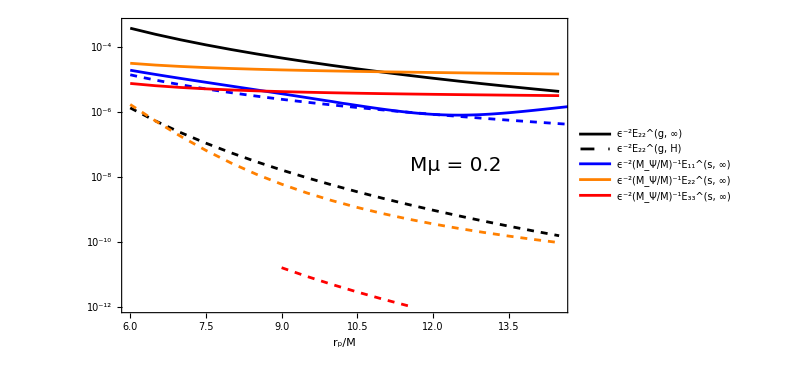

```mathematica
ListLogPlot[{tabμ02l2[[1;;-2,{1,2}]],tabμ02l2[[1;;-2,{1,3}]],tabμ02l1[[1;;-2,{1,2}]],tabμ02l1[[1;;-2,{1,3}]],tabμ02l2[[1;;-2,{1,4}]],tabμ02l2[[1;;-2,{1,5}]],tabμ02l3∞[[1;;-2,{1,4}]],tabμ02l3H[[1;;-2,{1,5}]]},Joined->True,Frame->True,FrameStyle->Directive[GrayLevel[0],20,Italic(*,FontFamily->"Times New Roman"*),AbsoluteThickness[2]],FrameLabel->{{None,None},{"r_p/M",None}},ImageSize->600,PlotRange->{{6,14.5},{10^-12,5*10^-4}},PlotStyle->{Black,{Black,Dashed},Blue,{Blue,Dashed},{Orange},{Orange,Dashed},{Red},{Red,Dashed}},PlotLegends->Placed[{Style["ϵ^-2E_22^(g, ∞)",18,Italic],Style["ϵ^-2E_22^(g, H)",18,Italic],Style["ϵ^-2(M_Ψ/M)^-1E_11^(s, ∞)",18,Italic],None,Style["ϵ^-2(M_Ψ/M)^-1E_22^(s, ∞)",18,Italic],None,Style["ϵ^-2(M_Ψ/M)^-1E_33^(s, ∞)",18,Italic]},{0.185,0.245}],Epilog->{Text[Style["Mμ = 0.2",20,Italic],Scaled[{0.75,0.5}]]}]
```

```mathematica
Quit[];
```

```mathematica
master=Import["./src/final_polar_full_l1.mx"];
```

```mathematica
master
```

{{-((2 MBH+r+n r) H1[r])/(2 MBH r-r^2)-(8 ⅈ mp π Conjugate[𝓂] SphericalHarmonicY[ℓ,𝓂,π/2,0] δ[r])/(r √(-3+r/MBH) Abs[1+n])+H1'[r],(ⅈ (1+n) H1[r])/(r σ)+H2[r],((1+n) H0[r])/(2 MBH-r)-(2 ⅈ r σ H1[r])/(2 MBH-r)+H2[r]/(-2 MBH+r)+H0'[r],(ⅇ^(-MBH r μ^2) MBH^(3/2) √MBS (1-(2 MBH)/r)^(-2-2 ⅈ MBH μ) r μ^2 ω (σ+2 ω) H0[r])/(2 √π)-(ⅈ ⅇ^(-MBH r μ^2) MBH^(3/2) √MBS (1-(2 MBH)/r)^(-2 ⅈ MBH μ) r μ^2 (2 r ω+2 MBH^2 μ (-2 ⅈ+r μ) (σ+2 ω)-MBH (4 ω+r^2 μ^2 (σ+2 ω))) H1[r])/(√π (-2 MBH+r)^2)-(ⅇ^(-MBH r μ^2) MBH^(3/2) √MBS (1-(2 MBH)/r)^(-2 ⅈ MBH μ) μ^2 (-4 MBH r^3 μ^2+8 MBH^4 μ^2 (-2 ⅈ+r μ)^2+2 MBH^2 r^2 μ^2 (6+r^2 μ^2)-8 MBH^3 r μ^2 (1-2 ⅈ r μ+r^2 μ^2)-r^4 σ ω) H2[r])/(2 √π r (-2 MBH+r)^2)+(ⅇ^(-MBH r μ^2) MBH^(5/2) √MBS (1-(2 MBH)/r)^(-2 ⅈ MBH μ) μ^3 (-r^2 μ+2 MBH (-2 ⅈ+r μ)) H0'[r])/(2 √π (2 MBH-r))-(ⅈ ⅇ^(-MBH r μ^2) MBH^(3/2) √MBS (1-(2 MBH)/r)^(-1-2 ⅈ MBH μ) r μ^2 ω H1'[r])/(√π)+(ⅇ^(-MBH r μ^2) MBH^(5/2) √MBS (1-(2 MBH)/r)^(-2 ⅈ MBH μ) μ^3 (-r^2 μ+2 MBH (-2 ⅈ+r μ)) H2'[r])/(2 √π (2 MBH-r))+((4 MBH^2+2 MBH (r+2 n r+r^3 μ^2)+r^2 (-2-2 n+r^2 (-μ^2+(σ+ω)^2))) δΨp[r]+(2 MBH-r) r (-2 MBH δΨp'[r]+(2 MBH-r) r δΨp''[r]))/(r^2 (-2 MBH+r)^2)}}

```mathematica
solvergravl1[rp_(*radius of the particle*),rinf_(* outer radius in frequency units up to which we integrate *),precision_ (* precision that we want to use *)]:=Block[{rpart=rp,n=0,mp=1,MBH=1,ℓ=1,𝓂=1,ϵ=10^-4(* defines inner radius of integration by 2MBH(1+ϵ) *),r,r1,r2,ω,YH1,YH2,YH0,rules,eqnsH1,eqnsH2,eqnsH0,σ,H0,H1,H2,H0H,H1H,H2H,δ},

rules={MaxSteps->Infinity,Method->"StiffnessSwitching",InterpolationOrder->All,WorkingPrecision->precision} (* some inner integration rules of Mathematica that are helpfull *);
(* Define frequency and inner/outer boundary locations *)
σ=𝓂 Sqrt[1/r^3]//.r->rp;
{r1,r2}={2MBH(1+ϵ),Max[rinf/Abs[σ]]};

δ[r_]=DiracDelta[r-rp];

(* --- Boundary conditions at the horizon --- *)
{H0H,H1H,H2H}=SetPrecision[{0,0,0}//.r->r1,precision];
(* --- solve for H1 --- *)
eqnsH1=Join[SetPrecision[{master[[1,1]]==0},precision],{H1[r1]==H1H}];
YH1=NDSolve[eqnsH1,{H1},{r,r1,r2},rules][[1]];
(* --- solve for H2 --- *)
eqnsH2=Join[SetPrecision[{master[[1,2]]==0/.YH1},precision]];
YH2=Solve[eqnsH2,{H2[r]}][[1]];
(* --- solve for H0 --- *)
eqnsH0=Join[SetPrecision[{master[[1,3]]==0/.YH1/.YH2},precision],{H0[r1]==H0H}];
YH0=NDSolve[eqnsH0,{H0},{r,r1,r2},rules][[1]];
(* --- Forward integration --- *)
Return[{YH0[[1]],YH1[[1]],YH2[[1]],H0'[r]->D[H0[r]/.YH0,r],H1'[r]->D[H1[r]/.YH1,r],H2'[r]->D[H2[r]/.YH2,r]}];

]
```

```mathematica
solgravl1=solvergravl1[10,500,MachinePrecision]
```

{H0→InterpolatingFunction[…],H1→InterpolatingFunction[…],H2[r]→0.-((0.+31.6228 ⅈ) InterpolatingFunction[…][r])/r,H0'[r]→InterpolatingFunction[…][r],H1'[r]→InterpolatingFunction[…][r],H2'[r]→((0.+31.6228 ⅈ) InterpolatingFunction[…][r])/r^2-((0.+31.6228 ⅈ) InterpolatingFunction[…][r])/r}

```mathematica
{H1horinh,dH1horinh,H0horinh,dH0horinh,Khorinh,dKhorinh,δΨphorinh,dδΨphorinh,H1infinh,dH1infinh,H0infinh,dH0infinh,Kinfinh,dKinfinh,δΨpinfinh,dδΨpinfinh}= Import["./src/final_polar_full_l2.m"][[3;;-1]];
```

```mathematica
solverscalarl1[rp_(*radius of the particle*),rinf_(* outer radius in frequency units up to which we integrate *),precision_ (* precision that we want to use *),mu_(*μ*),Mc_(*mass of the boson cloud in units of MBH*) ,solsgrav_(*solution of the gravitational sector*)]:=Block[{rpart=rp,n,mp=1,MBH=1,,ℓ=1,𝓂=1,μ=mu,MBS = Mc,ϵ=10^-4,r,r1,r2,ω,YH,YI,rules,eqns,σ,δΨph,δΨp∞,δΨp,δΨpH,δΨpI,dδΨpI,dδΨpH,wronsk,eqnsaux,masteraux,δΦplusAsymI,δΦplusAsymH},

rules={MaxSteps->Infinity,Method->"StiffnessSwitching",InterpolationOrder->All,WorkingPrecision->precision};

n=(ℓ-1)(ℓ+2)/2;
σ=𝓂 Sqrt[1/r^3]//.r->rp;
ω=μ*(1-1/2(MBH μ)^2)(*again using a Newtonian approximation for the frequency of the scalar field*);
{r1,r2}={2MBH(1+ϵ),rinf/Abs[σ]};

(* --- Forward integration --- *)
δΨph[0]=1;
{δΨpH,dδΨpH}=SetPrecision[{δΨphorinh(*1*),dδΨphorinh(*-ⅈ (ω+σ)/(1-2MBH/r1)*) }/.r->r1,precision](*SetPrecision[{1,-ⅈ (ω+σ)/(1-2MBH/r1) },precision];*);
eqnsaux=Join[SetPrecision[{master[[1,4]]==0/.{H1[r]->0,H0[r]->0,H2[r]->0,H0'[r]->0,H1'[r]->0,H2'[r]->0}},precision],{δΨp[r1]==δΨpH,δΨp'[r1]==dδΨpH}];
eqns=eqnsaux;
YH=NDSolve[eqns,{δΨp},{r,r1,r2},rules][[1]];
(* --- Backward integration --- *)
δΨp∞[0]=1;
{δΨpI,dδΨpI}=SetPrecision[{δΨpinfinh(*1*),dδΨpinfinh(*ⅈ Sqrt[(ω+σ)^2-μ^2]*) }/.r->r2,precision];
eqnsaux=Join[SetPrecision[{master[[1,4]]==0/.{H1[r]->0,H0[r]->0,H2[r]->0,H0'[r]->0,H1'[r]->0,H2'[r]->0}},precision],{δΨp[r2]==δΨpI,δΨp'[r2]==dδΨpI}];
eqns=eqnsaux;
YI=NDSolve[eqns,{δΨp},{r,r1,r2},rules][[1]];
(* --- Compute Wronskian --- *)
wronsk[rr_]=Wronskian[{δΨp[r]/.YH,δΨp[r]/.YI},r]/.r->rr;
(* --- Integrate over source term --- *)
masteraux=master[[1,4]]/.{δΨp[r]->0,δΨp'[r]->0,δΨp''[r]->0}/.solsgrav;
δΦplusAsymI=NIntegrate[masteraux*δΨp[r]/wronsk[r]/.solsgrav/.YH,{r,r1,r2},MaxRecursion->25];
δΦplusAsymH=NIntegrate[masteraux*δΨp[r]/wronsk[r]/.solsgrav/.YI,{r,r1,r2},MaxRecursion->25];

Return[{(σ)*Sqrt[(ω+σ)^2-μ^2] Abs[δΦplusAsymI]^2,(ω+σ)(σ)Abs[δΦplusAsymH]^2}];

]
```

```mathematica
solverscalarl1[10,1000/2,MachinePrecision,0.3,1,solgravl1]
```

{3.71326×10^-6,0.0000678005}

```mathematica
rpart=10(*79456*10^-4 *)(*the more precision you use the better*);
σpart=1/100;
lpart=1;
mpart=1;
x0=0.0001-0.001ⅈ;(*initial guess*)
μpart=0.2;
MCpart=1;
rext=1000;
```

```mathematica
tabμ02l1=Table[{rpart,
solgravl1=solvergravl1[rpart,rext,MachinePrecision];
solscl1=solverscalarl1[rpart,rext/2,MachinePrecision,μpart,MCpart,solgravl1];
solscl1[[1]],solscl1[[2]]
},{rpart,6,50,0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 25 recursive bisections in r near {r} = {6.00001}. NIntegrate obtained -0.032818-0.0236346 ⅈ and 6.95346×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 25 recursive bisections in r near {r} = {6.10001}. NIntegrate obtained -0.0349568-0.019444 ⅈ and 5.1365×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 25 recursive bisections in r near {r} = {6.10001}. NIntegrate obtained -0.00922647-0.0255061 ⅈ and 3.5608×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: (2.04839×10^-220)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.40887×10^-190)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.62841×10^-228)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
tabμ02l1={{6.,0.000019185064154157664,0.000013858665203278347},{6.1,0.000018036021628445476,0.000012812140495397531},{6.2,0.000016972119394982504,0.000011868858279322312},{6.3,0.00001598510057977569,0.000011016488149666653},{6.4,0.000015067636798220329,0.000010244386811515805},{6.5,0.000014213312660363214,9.54336387529894*^-6},{6.6,0.000013416447228373216,8.90546932257699*^-6},{6.7,0.000012671970930176732,8.323758130312897*^-6},{6.8,0.000011975361221179602,7.792192316158025*^-6},{6.9,0.0000113226376010473,7.3054814323530325*^-6},{7.,0.000010710134642975987,6.859000781172307*^-6},{7.1,0.000010136061896135804,6.4488403684721166*^-6},{7.2,9.593345704062337*^-6,6.070851084375313*^-6},{7.3,9.08357805808303*^-6,5.722422097572118*^-6},{7.4,8.603018086030097*^-6,5.400587300404322*^-6},{7.5,8.14950439702786*^-6,5.102793283216825*^-6},{7.6,7.721190712962327*^-6,4.826869985876665*^-6},{7.7,7.316295251007354*^-6,4.570798528799951*^-6},{7.8,6.933238153992517*^-6,4.332848074506124*^-6},{7.9,6.570620346528281*^-6,4.111406068151367*^-6},{8.,6.227099582568715*^-6,3.905067105079067*^-6},{8.1,5.901499020902575*^-6,3.712551704769359*^-6},{8.2,5.5927352745000795*^-6,3.532705334340466*^-6},{8.3,5.299794581389404*^-6,3.3644988279687433*^-6},{8.4,5.021786867937413*^-6,3.2069992318494604*^-6},{8.5,4.757849124180344*^-6,3.0593559008887027*^-6},{8.6,4.507223964157907*^-6,2.9208004881440436*^-6},{8.7,4.269200499875651*^-6,2.7906464743571657*^-6},{8.8,4.043102075141865*^-6,2.668238871420529*^-6},{8.9,3.8283699094347325*^-6,2.5530279613081396*^-6},{9.,3.6244050136279617*^-6,2.4444667350064156*^-6},{9.1,3.430704374206567*^-6,2.3420938293981935*^-6},{9.2,3.246773581912551*^-6,2.245448936850763*^-6},{9.3,3.07218261235921*^-6,2.154147361108861*^-6},{9.4,2.9065045038177323*^-6,2.06781255153473*^-6},{9.5,2.7493545295880907*^-6,1.9861097836732776*^-6},{9.6,2.6003816002256672*^-6,1.9087315927696297*^-6},{9.7,2.4592375457533425*^-6,1.8353791307172604*^-6},{9.8,2.325614124215175*^-6,1.7658136261602186*^-6},{9.9,2.1992165250303714*^-6,1.699767560832695*^-6},{10.,2.0885034507105544*^-6,1.637814310719255*^-6},{10.100000000000001,1.9639667070386795*^-6,1.577112865347828*^-6},{10.2,1.847254858259834*^-6,1.5194639671507391*^-6},{10.3,1.7605884572593777*^-6,1.4666374123317*^-6},{10.4,1.6667113831689909*^-6,1.4152141053176317*^-6},{10.5,1.5781968265300225*^-6,1.3661645865085262*^-6},{10.600000000000001,1.495508986768375*^-6,1.3194037513307153*^-6},{10.7,1.4182449817001556*^-6,1.2747797401866338*^-6},{10.8,1.346237399359301*^-6,1.2321747640620182*^-6},{10.9,1.279320503045418*^-6,1.1914669247132104*^-6},{11.,1.217342681587218*^-6,1.1525525560501992*^-6},{11.100000000000001,1.1601591756045202*^-6,1.1153380898027648*^-6},{11.2,1.1076284105559201*^-6,1.079720970552519*^-6},{11.3,1.0596202516347344*^-6,1.0456222716119442*^-6},{11.4,1.0155445059438533*^-6,1.0129244334880332*^-6},{11.5,9.766771510201561*^-7,9.8165517621051*^-7},{11.600000000000001,9.415066189531111*^-7,9.516380401798363*^-7},{11.7,9.10392219304977*^-7,9.228442319131477*^-7},{11.8,8.832256765262671*^-7,8.952063362850604*^-7},{11.9,8.599101833321953*^-7,8.686685450486776*^-7},{12.,8.40356443951807*^-7,8.431817289497725*^-7},{12.100000000000001,8.244621508693253*^-7,8.18684029565034*^-7},{12.2,8.121459687371917*^-7,7.951327756827509*^-7},{12.3,8.033313222598914*^-7,7.724855419763425*^-7},{12.4,7.979212814025462*^-7,7.506889226881858*^-7},{12.5,7.958413246735152*^-7,7.297051497241965*^-7},{12.600000000000001,7.97022015137974*^-7,7.094998844211197*^-7},{12.7,8.014028337979349*^-7,6.900395401368164*^-7},{12.8,8.089001538075997*^-7,6.712852981987854*^-7},{12.9,8.194284444712105*^-7,6.531979000324839*^-7},{13.,8.329678439005792*^-7,6.357627128790312*^-7},{13.100000000000001,8.494263174196683*^-7,6.189400279957161*^-7},{13.2,8.687594348512561*^-7,6.027081274204549*^-7},{13.3,8.908819175258573*^-7,5.870338162510285*^-7},{13.4,9.157889492334198*^-7,5.719041545174768*^-7},{13.5,9.433459760284547*^-7,5.57279516520459*^-7},{13.600000000000001,9.735687679735574*^-7,5.431519485699317*^-7},{13.7,1.006383075398403*^-6,5.294961818705153*^-7},{13.8,1.0417393797239073*^-6,5.162919093451142*^-7},{13.9,1.079597444195198*^-6,5.035222777686531*^-7},{14.,1.1199023935850403*^-6,4.911676472534123*^-7},{14.1,1.16259598183493*^-6,4.792091472903287*^-7},{14.200000000000001,1.207674951676806*^-6,4.6763714258559727*^-7},{14.3,1.255048372771842*^-6,4.564287442711003*^-7},{14.4,1.3046858559665694*^-6,4.455720159877662*^-7},{14.5,1.3565833396467957*^-6,4.350567763962071*^-7},{14.6,1.4106511170880928*^-6,4.248639717289575*^-7},{14.700000000000001,1.466868557780119*^-6,4.149843346471822*^-7},{14.8,1.5252109260538155*^-6,4.0540559407638737*^-7},{14.9,1.5856534639234948*^-6,3.961176462708836*^-7},{15.,1.6481413684183221*^-6,3.871083692851415*^-7},{15.1,1.7125724913569068*^-6,3.783616174662161*^-7},{15.200000000000001,1.779022574949064*^-6,3.698759618251322*^-7},{15.3,1.8474127370851846*^-6,3.6163872605088094*^-7},{15.4,1.9177105444078324*^-6,3.536405750116915*^-7},{15.5,1.9898738074460863*^-6,3.4587247625695967*^-7},{15.600000000000001,2.064509820564631*^-6,3.383372476102347*^-7},{15.700000000000001,2.1397269268579792*^-6,3.309961926084527*^-7},{15.8,2.217332962564001*^-6,3.238710175808814*^-7},{15.9,2.2967158146097705*^-6,3.169464341720318*^-7},{16.,2.37778550859795*^-6,3.1021257363383596*^-7},{16.1,2.460575308129881*^-6,3.036651969487053*^-7},{16.200000000000003,2.545058133102069*^-6,2.972980856216578*^-7},{16.3,2.6311128157950104*^-6,2.911012963178369*^-7},{16.4,2.7188393752900274*^-6,2.850742316955558*^-7},{16.5,2.808121035919089*^-6,2.792072972148964*^-7},{16.6,2.8989860318576543*^-6,2.7349740207179113*^-7},{16.700000000000003,2.9913817346429178*^-6,2.679383539334291*^-7},{16.8,3.085260329426465*^-6,2.6252434445674794*^-7},{16.9,3.180693654433397*^-6,2.5725366445219553*^-7},{17.,3.27755069401111*^-6,2.5211835707994464*^-7},{17.1,3.3758486435808155*^-6,2.4711522316588737*^-7},{17.200000000000003,3.4759755441288143*^-6,2.422404006231584*^-7},{17.3,3.576715756228553*^-6,2.3748998219728584*^-7},{17.4,3.6792072647932073*^-6,2.328589833210076*^-7},{17.5,3.7830470934674445*^-6,2.2834415329040823*^-7},{17.6,3.88827597455297*^-6,2.2394296094822768*^-7},{17.700000000000003,3.994691788748768*^-6,2.1964846981765143*^-7},{17.8,4.102538834870793*^-6,2.1546282918049898*^-7},{17.9,4.211515074773912*^-6,2.113765171054688*^-7},{18.,4.321832221214104*^-6,2.0739173668604947*^-7},{18.1,4.433307301877314*^-6,2.0350183230078965*^-7},{18.200000000000003,4.5460378103428805*^-6,1.9970626308717205*^-7},{18.3,4.659917040487318*^-6,1.9600060389801557*^-7},{18.4,4.774991874801158*^-6,1.9238374548183296*^-7},{18.5,4.8911710863823534*^-6,1.8885132540818808*^-7},{18.6,5.008597845121169*^-6,1.8540375548748702*^-7},{18.700000000000003,5.12712605882533*^-6,1.8203635277325062*^-7},{18.8,5.246639718630766*^-6,1.7874546802038798*^-7},{18.9,5.367596401389352*^-6,1.7553080406520697*^-7},{19.,5.488996021264088*^-6,1.723908136990682*^-7},{19.1,5.611752051176236*^-6,1.6932212096754374*^-7},{19.200000000000003,5.73550098651234*^-6,1.6632249456294598*^-7},{19.3,5.860261142939594*^-6,1.6339066850158363*^-7},{19.4,5.98621555164782*^-6,1.6052707992521648*^-7},{19.5,6.112756107316399*^-6,1.5772261906457963*^-7},{19.6,6.24052687166736*^-6,1.5498366492615684*^-7},{19.700000000000003,6.369137352987851*^-6,1.52303843350628*^-7},{19.8,6.498698968465149*^-6,1.496837274171046*^-7},{19.9,6.629238443040894*^-6,1.4712058531686747*^-7},{20.,6.760594183361664*^-6,1.4461274386195628*^-7},{20.1,6.892885499989443*^-6,1.421596322017214*^-7},{20.200000000000003,7.026095289522897*^-6,1.3975962955482236*^-7},{20.3,7.160060382428424*^-6,1.37410114355322*^-7},{20.4,7.294870115433129*^-6,1.3511067857931952*^-7},{20.5,7.430616667513089*^-6,1.3286088982695732*^-7},{20.6,7.567030659400431*^-6,1.3065735378258773*^-7},{20.700000000000003,7.70428927280981*^-6,1.2850039927933755*^-7},{20.8,7.84233543027697*^-6,1.2638843888345627*^-7},{20.9,7.981199845161146*^-6,1.2432070335671355*^-7},{21.,8.1207981182815*^-6,1.2229552019933608*^-7},{21.1,8.261098771610587*^-6,1.2031167532844103*^-7},{21.200000000000003,8.40243036983671*^-6,1.1836814778919953*^-7},{21.3,8.543907588862967*^-6,1.1646494534500993*^-7},{21.4,8.686215578492572*^-6,1.1459889978432469*^-7},{21.5,8.829529656726531*^-6,1.1277253554987872*^-7},{21.6,8.973391713465731*^-6,1.1098208774877008*^-7},{21.700000000000003,9.117793158110961*^-6,1.0922660813228382*^-7},{21.8,9.262980956299436*^-6,1.075067466550579*^-7},{21.9,9.4087415096926*^-6,1.0582069004548329*^-7},{22.,9.555103958085798*^-6,1.0416756005040366*^-7},{22.1,9.70222470458489*^-6,1.0254773027943924*^-7},{22.2,9.849911985933664*^-6,1.0095927322334485*^-7},{22.3,9.998093351837521*^-6,9.940124084044609*^-8},{22.400000000000002,0.000010146904804928361,9.787358490628272*^-8},{22.5,0.000010296338979067104,9.637576897237861*^-8},{22.6,0.000010454930975725845,9.489944807379026*^-8},{22.7,0.000010596010317816447,9.346649820755132*^-8},{22.8,0.000010736508505342987,9.20594750880964*^-8},{22.900000000000002,0.000010899475810341318,9.066436609635619*^-8},{23.,0.000011051385057203248,8.930267972767345*^-8},{23.1,0.000011204072178441034,8.796763519071648*^-8},{23.2,0.000011357180573606274,8.665738656108855*^-8},{23.3,0.000011510726403207508,8.537130659136707*^-8},{23.400000000000002,0.000011664720581749602,8.410902053765456*^-8},{23.5,0.000011819324017805479,8.287051345641893*^-8},{23.6,0.000011974281775339638,8.165450190238719*^-8},{23.7,0.000012129577265234566,8.046042581441947*^-8},{23.8,0.00001228549552193885,7.928879562557502*^-8},{23.900000000000002,0.000012441755967085448,7.81381427683364*^-8},{24.,0.000012598222555361949,7.700852147572495*^-8},{24.1,0.000012755362017251523,7.589837240767526*^-8},{24.2,0.000012912918116701493,7.480926690187178*^-8},{24.3,0.00001307085770184818,7.373942292878881*^-8},{24.400000000000002,0.0000132291277199639,7.268857098875727*^-8},{24.5,0.000013387740989154722,7.165626243144952*^-8},{24.6,0.000013546618309748298,7.064201658153691*^-8},{24.7,0.000013706115725763987,6.964640501018028*^-8},{24.8,0.000013867481775038481,6.866701677809069*^-8},{24.900000000000002,0.0000140257888042175,6.770630702164182*^-8},{25.,0.000014186127984967328,6.676159302818628*^-8},{25.1,0.000014346758273398838,6.58331652326144*^-8},{25.200000000000003,0.000014507777750994582,6.492109700341856*^-8},{25.3,0.00001466889849448159,6.402421446675053*^-8},{25.400000000000002,0.000014830488931489967,6.314322095234563*^-8},{25.5,0.000014992431806421924,6.22774476440382*^-8},{25.6,0.000015154386600041626,6.14257721929485*^-8},{25.700000000000003,0.000015316699677801235,6.058880337860002*^-8},{25.8,0.00001547941115594772,5.976635692983341*^-8},{25.900000000000002,0.000015642276666646336,5.8957581021090935*^-8},{26.,0.000015805472009636324,5.816256759437642*^-8},{26.1,0.00001596855912292113,5.7380078920296744*^-8},{26.200000000000003,0.000016132431873952098,5.661195073479341*^-8},{26.3,0.000016296683246534604,5.585691027529393*^-8},{26.400000000000002,0.000016460006325385814,5.5111976283781934*^-8},{26.5,0.00001662462590594407,5.438162171970297*^-8},{26.6,0.000016788828862844773,5.3662060234684554*^-8},{26.700000000000003,0.000016953500461778622,5.2954835202423176*^-8},{26.8,0.00001711835996006048,5.225924138205337*^-8},{26.900000000000002,0.000017283220491007326,5.157458576075552*^-8},{27.,0.000017448334319387508,5.0901378405602456*^-8},{27.1,0.000017615714171668408,5.023830678117*^-8},{27.200000000000003,0.000017779163010604232,4.958745970051678*^-8},{27.3,0.00001794485334098824,4.8946437113490746*^-8},{27.400000000000002,0.000018110534129393145,4.8315479398331845*^-8},{27.5,0.00001827648988079774,4.769484836468396*^-8},{27.6,0.00001844237475161469,4.708376812737605*^-8},{27.700000000000003,0.00001860874773999179,4.648300338341174*^-8},{27.8,0.000018774988182848246,4.589137412252042*^-8},{27.900000000000002,0.000018941296208003025,4.530901432626808*^-8},{28.,0.00001910791563344816,4.473621332323615*^-8},{28.1,0.000019274575479479417,4.417222438533713*^-8},{28.200000000000003,0.000019441141719206824,4.3616823524129085*^-8},{28.3,0.00001960800069054065,4.307037366071935*^-8},{28.400000000000002,0.000019774872848682333,4.253241227400434*^-8},{28.5,0.00001994190377388677,4.2002895501532746*^-8},{28.6,0.000020108763715118643,4.148121695256795*^-8},{28.700000000000003,0.00002027591674398064,4.0967914639664074*^-8},{28.8,0.000020442789824747578,4.046207974652513*^-8},{28.900000000000002,0.000020610046371339596,3.996445266697762*^-8},{29.,0.000020777274014662683,3.947427593626427*^-8},{29.1,0.000020944618872090677,3.899176441707263*^-8},{29.200000000000003,0.0000211118008943014,3.851630596837203*^-8},{29.3,0.000021279121840597162,3.804821759407762*^-8},{29.400000000000002,0.000021446520260285432,3.7587242958100594*^-8},{29.5,0.000021614099198414738,3.7133437188931006*^-8},{29.6,0.000021783631240964005,3.66858717117887*^-8},{29.700000000000003,0.000021948720252641485,3.6245530404423975*^-8},{29.8,0.000022116186201158892,3.581167196068001*^-8},{29.900000000000002,0.000022283574452758206,3.5384226772779406*^-8},{30.,0.000022450960346521575,3.496314706563866*^-8},{30.1,0.000022618446165057962,3.4548437814148266*^-8},{30.200000000000003,0.000022785620779093684,3.413953561021292*^-8},{30.3,0.00002295310255338952,3.373707762475547*^-8},{30.400000000000002,0.000023120625545622,3.33405933852116*^-8},{30.5,0.000023287746356210802,3.2949553981100396*^-8},{30.6,0.000023455221429920493,3.2564616523711515*^-8},{30.700000000000003,0.000023622386660006485,3.2185054703371465*^-8},{30.8,0.00002378963900865526,3.1811166116997133*^-8},{30.900000000000002,0.00002395677184078046,3.144261466506188*^-8},{31.,0.000024124016496849275,3.1079565533206454*^-8},{31.1,0.000024291176479228626,3.07218101117348*^-8},{31.200000000000003,0.00002445803550384994,3.0368942229573226*^-8},{31.3,0.000024625102280962273,3.0021404201979696*^-8},{31.400000000000002,0.000024792024385617687,2.9678833138140086*^-8},{31.5,0.000024958920532497983,2.9341180007733453*^-8},{31.6,0.00002512559628349099,2.9008209621007904*^-8},{31.700000000000003,0.0000252923394307197,2.868016800837793*^-8},{31.8,0.000025458832527110763,2.8356606382160924*^-8},{31.900000000000002,0.00002562553330562697,2.803791620129284*^-8},{32.,0.000025792111639131055,2.7723731326613695*^-8},{32.1,0.00002595844931978065,2.7413802172614624*^-8},{32.2,0.00002612462998989067,2.7108228253603706*^-8},{32.3,0.00002629611737966659,2.6806979417891625*^-8},{32.400000000000006,0.00002644649565243863,2.6510675811981285*^-8},{32.5,0.00002662289502703075,2.6217381600796904*^-8},{32.6,0.000026789014398164936,2.592885844646629*^-8},{32.7,0.000026954711440122136,2.564416293124822*^-8},{32.8,0.000027120423418665867,2.5363475893157004*^-8},{32.900000000000006,0.000027285902859058963,2.5086650763342683*^-8},{33.,0.00002745145334499467,2.481381620102689*^-8},{33.1,0.00002761704857798223,2.4544847268692896*^-8},{33.2,0.000027782275029568922,2.4279384418918685*^-8},{33.3,0.00002794737296160679,2.401764562339354*^-8},{33.400000000000006,0.000028112664802264553,2.3759640876693877*^-8},{33.5,0.00002827711212196527,2.3504779784648137*^-8},{33.6,0.000028442290247751018,2.3253925178585783*^-8},{33.7,0.000028606773580640426,2.3006143800043566*^-8},{33.8,0.00002877141982321641,2.276193577184987*^-8},{33.900000000000006,0.000028936673275743238,2.252149199094213*^-8},{34.,0.000029100501249829006,2.228353855698786*^-8},{34.1,0.0000292647239966052,2.204914075957379*^-8},{34.2,0.00002942892668534519,2.1817966491450077*^-8},{34.3,0.000029592914046847208,2.158987166554719*^-8},{34.400000000000006,0.000029757053004976462,2.1365050281276784*^-8},{34.5,0.00002992035208709885,2.114278314628816*^-8},{34.6,0.00003008416040451641,2.0923938464797014*^-8},{34.7,0.0000302478913586454,2.070800526172221*^-8},{34.8,0.000030411393097296444,2.049494650070527*^-8},{34.900000000000006,0.00003057443142663771,2.0284497536632663*^-8},{35.,0.00003073792172528585,2.00771815534422*^-8},{35.1,0.00003090134740561191,1.9872663386956762*^-8},{35.2,0.000031064288307778014,1.9670671518101773*^-8},{35.3,0.00003122655531978424,1.94714932645713*^-8},{35.400000000000006,0.00003138982242576266,1.927473137969182*^-8},{35.5,0.00003155304858024172,1.9080932508735835*^-8},{35.6,0.00003171587685994506,1.8889561123506448*^-8},{35.7,0.000031878868468140686,1.8700848137208105*^-8},{35.8,0.00003204103107584191,1.851428053758157*^-8},{35.900000000000006,0.00003220411764270624,1.8330583353556426*^-8},{36.,0.000032367055026814496,1.814923385675428*^-8},{36.1,0.00003252969441762005,1.797017625226778*^-8},{36.2,0.00003269190246711336,1.779327558508528*^-8},{36.3,0.000032855590375854164,1.761923675216663*^-8},{36.400000000000006,0.000033018138234345026,1.7447108914164225*^-8},{36.5,0.000033180927049827506,1.7277183617383593*^-8},{36.6,0.00003334422434939668,1.7109664163513362*^-8},{36.7,0.000033507824865997605,1.694439152037645*^-8},{36.8,0.00003367084474815166,1.6781038150411166*^-8},{36.900000000000006,0.00003383480135314039,1.6620080767936963*^-8},{37.,0.00003399871539460409,1.6460953616886008*^-8},{37.1,0.00003416345229013446,1.6304172494557908*^-8},{37.2,0.00003432801226026333,1.6149181298979654*^-8},{37.3,0.00003449379212105977,1.599644219689379*^-8},{37.400000000000006,0.000034659029163146156,1.584539113402175*^-8},{37.5,0.0000348260850441035,1.5696460803447767*^-8},{37.6,0.000034994111859287326,1.554957353194014*^-8},{37.7,0.00003516275973690095,1.540453399695844*^-8},{37.8,0.000035333711197973176,1.5261545940868232*^-8},{37.900000000000006,0.00003550472920695511,1.5120100742828136*^-8},{38.,0.000035678618878457995,1.4980497180137963*^-8},{38.1,0.00003585454492936299,1.4842981450728213*^-8},{38.2,0.00003603303086649622,1.4706959884680398*^-8},{38.300000000000004,0.00003621600420996242,1.4572757494924922*^-8},{38.4,0.000036402754753444484,1.4440352752451712*^-8},{38.5,0.00003659880718184235,1.4309810287021733*^-8},{38.6,0.00003679474981836744,1.4180769829943027*^-8},{38.7,0.00003700311787534964,1.4052793249254548*^-8},{38.800000000000004,0.00003722743449185253,1.3927751890546554*^-8},{38.9,0.000037465923455624585,1.3802899471270964*^-8},{39.,0.000037735118847241487,1.3680813251639443*^-8},{39.1,0.000038043866795343463,1.3560490404765718*^-8},{39.2,0.000038414563111521275,1.3439276696059198*^-8},{39.300000000000004,0.000038916955533900287,1.3322756657835026*^-8},{39.4,0.00003966243772382432,1.3206376445656323*^-8},{39.5,0.00004112326350489798,1.3092304607119383*^-8},{39.6,0.00004643226187039413,1.3010202468704098*^-8},{39.7,0.+0. ⅈ,7.23059962032004*^-8},{39.800000000000004,0.+0. ⅈ,2.1432928179604897*^-8},{39.9,0.+0. ⅈ,3.2965062560146763*^-8},{40.,0.+0. ⅈ,1.9765454342805862*^-8},{40.1,0.+0. ⅈ,8.654369095420763*^-8},{40.2,0.+0. ⅈ,1.8020204156344608*^-8},{40.300000000000004,0.+0. ⅈ,3.355277257934163*^-10},{40.4,0.+0. ⅈ,2.8582110315306853*^-8},{40.5,0.+0. ⅈ,5.6202531072963224*^-9},{40.6,0.+0. ⅈ,4.461703054222916*^-9},{40.7,0.+0. ⅈ,2.2289994466060475*^-8},{40.800000000000004,0.+0. ⅈ,1.0937920777603423*^-6},{40.9,0.+0. ⅈ,3.4767962339793022*^-9},{41.,0.+0. ⅈ,9.64449748643493*^-10},{41.1,0.+0. ⅈ,5.360708166424868*^-9},{41.2,0.+0. ⅈ,1.250915683633887*^-8},{41.300000000000004,0.+0. ⅈ,2.8213508748637513*^-8},{41.4,0.+0. ⅈ,1.0047162758816769*^-7},{41.5,0.+0. ⅈ,9.418917500527483*^-6},{41.6,0.+0. ⅈ,2.6434123055238843*^-8},{41.7,0.+0. ⅈ,2.051049772314242*^-9},{41.800000000000004,0.+0. ⅈ,6.851742378658108*^-13},{41.9,0.+0. ⅈ,7.760356629116704*^-10},{42.,0.+0. ⅈ,2.2900122927429083*^-9},{42.1,0.+0. ⅈ,4.190791484886915*^-9},{42.2,0.+0. ⅈ,6.4914390806986125*^-9},{42.300000000000004,0.+0. ⅈ,9.365492116744729*^-9},{42.4,0.+0. ⅈ,1.3161453372938593*^-8},{42.5,0.+0. ⅈ,1.8549686680057925*^-8},{42.6,0.+0. ⅈ,2.6938430324312747*^-8},{42.7,0.+0. ⅈ,4.174513803572838*^-8},{42.800000000000004,0.+0. ⅈ,7.333444782918021*^-8},{42.9,0.+0. ⅈ,1.679908371300584*^-7},{43.,0.+0. ⅈ,8.4790545913633*^-7},{43.1,0.+0. ⅈ,5.450585981972566*^-6},{43.2,0.+0. ⅈ,2.0989011286951198*^-7},{43.300000000000004,0.+0. ⅈ,5.4239477360034964*^-8},{43.4,0.+0. ⅈ,2.0725589631122013*^-8},{43.5,0.+0. ⅈ,9.142736692595964*^-9},{43.6,0.+0. ⅈ,4.188709050929286*^-9},{43.7,0.+0. ⅈ,1.8558857823484767*^-9},{43.800000000000004,0.+0. ⅈ,7.160322532355482*^-10},{43.9,0.+0. ⅈ,1.9222549851172548*^-10},{44.,0.+0. ⅈ,1.0883295473516806*^-11},{44.1,0.+0. ⅈ,3.2423211693872297*^-11},{44.2,0.+0. ⅈ,1.8101596150083457*^-10},{44.300000000000004,0.+0. ⅈ,4.1353746019120606*^-10},{44.400000000000006,0.+0. ⅈ,7.047293259355255*^-10},{44.5,0.+0. ⅈ,1.0395899619856753*^-9},{44.6,0.+0. ⅈ,1.4093496034070006*^-9},{44.7,0.+0. ⅈ,1.8090824557209737*^-9},{44.800000000000004,0.+0. ⅈ,2.236488185557027*^-9},{44.900000000000006,0.+0. ⅈ,2.691026441314572*^-9},{45.,0.+0. ⅈ,3.173522015803668*^-9},{45.1,0.+0. ⅈ,3.6857836261752884*^-9},{45.2,0.+0. ⅈ,4.2306980603895064*^-9},{45.300000000000004,0.+0. ⅈ,4.811944135513398*^-9},{45.400000000000006,0.+0. ⅈ,5.433867082831307*^-9},{45.5,0.+0. ⅈ,6.099997627539705*^-9},{45.6,0.+0. ⅈ,6.821960298050036*^-9},{45.7,0.+0. ⅈ,7.604599145145258*^-9},{45.800000000000004,0.+0. ⅈ,8.456963059665453*^-9},{45.900000000000006,0.+0. ⅈ,9.390049763870611*^-9},{46.,0.+0. ⅈ,1.041691925807518*^-8},{46.1,0.+0. ⅈ,1.1553859452797533*^-8},{46.2,0.+0. ⅈ,1.2819784898165122*^-8},{46.300000000000004,0.+0. ⅈ,1.4237540514747137*^-8},{46.400000000000006,0.+0. ⅈ,1.5836730393597918*^-8},{46.5,0.+0. ⅈ,1.7652851460881474*^-8},{46.6,0.+0. ⅈ,1.9730859581073573*^-8},{46.7,0.+0. ⅈ,2.2128312926469717*^-8},{46.800000000000004,0.+0. ⅈ,2.4918256635005788*^-8},{46.900000000000006,0.+0. ⅈ,2.8196204501305308*^-8},{47.,0.+0. ⅈ,3.214395915341682*^-8},{47.1,0.+0. ⅈ,3.684106292057091*^-8},{47.2,0.+0. ⅈ,4.256212240167592*^-8},{47.300000000000004,0.+0. ⅈ,4.963631420384007*^-8},{47.400000000000006,0.+0. ⅈ,5.853775940411557*^-8},{47.5,0.+0. ⅈ,6.996354964261306*^-8},{47.6,0.+0. ⅈ,8.498511388886849*^-8},{47.7,0.+0. ⅈ,1.0530519984690164*^-7},{47.800000000000004,0.+0. ⅈ,1.337610373843822*^-7},{47.900000000000006,0.+0. ⅈ,1.75408460942496*^-7},{48.,0.+0. ⅈ,2.399255823390676*^-7},{48.1,0.+0. ⅈ,3.478620781130121*^-7},{48.2,0.+0. ⅈ,5.493341159165415*^-7},{48.300000000000004,0.+0. ⅈ,9.952186551665367*^-7},{48.400000000000006,0.+0. ⅈ,2.3325320782616623*^-6},{48.5,0.+0. ⅈ,0.000010674744917014493},{48.6,0.+0. ⅈ,0.0005170751245525072},{48.7,0.+0. ⅈ,6.392738133498273*^-6},{48.800000000000004,0.+0. ⅈ,1.783393164211366*^-6},{48.900000000000006,0.+0. ⅈ,8.203326604201684*^-7},{49.,0.+0. ⅈ,4.681747366460932*^-7},{49.1,0.+0. ⅈ,3.0149869177225546*^-7},{49.2,0.+0. ⅈ,2.097596446132652*^-7},{49.300000000000004,0.+0. ⅈ,1.539916774859741*^-7},{49.400000000000006,0.+0. ⅈ,1.1760327039939423*^-7},{49.5,0.+0. ⅈ,9.257358150691842*^-8},{49.6,0.+0. ⅈ,7.463424589843782*^-8},{49.7,0.+0. ⅈ,6.134651832170946*^-8},{49.800000000000004,0.+0. ⅈ,5.123608575346532*^-8},{49.900000000000006,0.+0. ⅈ,4.337213902255549*^-8},{50.,0.+0. ⅈ,3.713586519226837*^-8}}
```

{{6.,0.0000191851,0.0000138587},{6.1,0.000018036,0.0000128121},{6.2,0.0000169721,0.0000118689},{6.3,0.0000159851,0.0000110165},{6.4,0.0000150676,0.0000102444},{6.5,0.0000142133,9.54336×10^-6},{6.6,0.0000134164,8.90547×10^-6},{6.7,0.000012672,8.32376×10^-6},{6.8,0.0000119754,7.79219×10^-6},{6.9,0.0000113226,7.30548×10^-6},{7.,0.0000107101,6.859×10^-6},{7.1,0.0000101361,6.44884×10^-6},{7.2,9.59335×10^-6,6.07085×10^-6},{7.3,9.08358×10^-6,5.72242×10^-6},{7.4,8.60302×10^-6,5.40059×10^-6},{7.5,8.1495×10^-6,5.10279×10^-6},{7.6,7.72119×10^-6,4.82687×10^-6},{7.7,7.3163×10^-6,4.5708×10^-6},{7.8,6.93324×10^-6,4.33285×10^-6},{7.9,6.57062×10^-6,4.11141×10^-6},{8.,6.2271×10^-6,3.90507×10^-6},{8.1,5.9015×10^-6,3.71255×10^-6},{8.2,5.59274×10^-6,3.53271×10^-6},{8.3,5.29979×10^-6,3.3645×10^-6},{8.4,5.02179×10^-6,3.207×10^-6},{8.5,4.75785×10^-6,3.05936×10^-6},{8.6,4.50722×10^-6,2.9208×10^-6},{8.7,4.2692×10^-6,2.79065×10^-6},{8.8,4.0431×10^-6,2.66824×10^-6},{8.9,3.82837×10^-6,2.55303×10^-6},{9.,3.62441×10^-6,2.44447×10^-6},{9.1,3.4307×10^-6,2.34209×10^-6},{9.2,3.24677×10^-6,2.24545×10^-6},{9.3,3.07218×10^-6,2.15415×10^-6},{9.4,2.9065×10^-6,2.06781×10^-6},{9.5,2.74935×10^-6,1.98611×10^-6},{9.6,2.60038×10^-6,1.90873×10^-6},{9.7,2.45924×10^-6,1.83538×10^-6},{9.8,2.32561×10^-6,1.76581×10^-6},{9.9,2.19922×10^-6,1.69977×10^-6},{10.,2.0885×10^-6,1.63781×10^-6},{10.1,1.96397×10^-6,1.57711×10^-6},{10.2,1.84725×10^-6,1.51946×10^-6},{10.3,1.76059×10^-6,1.46664×10^-6},{10.4,1.66671×10^-6,1.41521×10^-6},{10.5,1.5782×10^-6,1.36616×10^-6},{10.6,1.49551×10^-6,1.3194×10^-6},{10.7,1.41824×10^-6,1.27478×10^-6},{10.8,1.34624×10^-6,1.23217×10^-6},{10.9,1.27932×10^-6,1.19147×10^-6},{11.,1.21734×10^-6,1.15255×10^-6},{11.1,1.16016×10^-6,1.11534×10^-6},{11.2,1.10763×10^-6,1.07972×10^-6},{11.3,1.05962×10^-6,1.04562×10^-6},{11.4,1.01554×10^-6,1.01292×10^-6},{11.5,9.76677×10^-7,9.81655×10^-7},{11.6,9.41507×10^-7,9.51638×10^-7},{11.7,9.10392×10^-7,9.22844×10^-7},{11.8,8.83226×10^-7,8.95206×10^-7},{11.9,8.5991×10^-7,8.68669×10^-7},{12.,8.40356×10^-7,8.43182×10^-7},{12.1,8.24462×10^-7,8.18684×10^-7},{12.2,8.12146×10^-7,7.95133×10^-7},{12.3,8.03331×10^-7,7.72486×10^-7},{12.4,7.97921×10^-7,7.50689×10^-7},{12.5,7.95841×10^-7,7.29705×10^-7},{12.6,7.97022×10^-7,7.095×10^-7},{12.7,8.01403×10^-7,6.9004×10^-7},{12.8,8.089×10^-7,6.71285×10^-7},{12.9,8.19428×10^-7,6.53198×10^-7},{13.,8.32968×10^-7,6.35763×10^-7},{13.1,8.49426×10^-7,6.1894×10^-7},{13.2,8.68759×10^-7,6.02708×10^-7},{13.3,8.90882×10^-7,5.87034×10^-7},{13.4,9.15789×10^-7,5.71904×10^-7},{13.5,9.43346×10^-7,5.5728×10^-7},{13.6,9.73569×10^-7,5.43152×10^-7},{13.7,1.00638×10^-6,5.29496×10^-7},{13.8,1.04174×10^-6,5.16292×10^-7},{13.9,1.0796×10^-6,5.03522×10^-7},{14.,1.1199×10^-6,4.91168×10^-7},{14.1,1.1626×10^-6,4.79209×10^-7},{14.2,1.20767×10^-6,4.67637×10^-7},{14.3,1.25505×10^-6,4.56429×10^-7},{14.4,1.30469×10^-6,4.45572×10^-7},{14.5,1.35658×10^-6,4.35057×10^-7},{14.6,1.41065×10^-6,4.24864×10^-7},{14.7,1.46687×10^-6,4.14984×10^-7},{14.8,1.52521×10^-6,4.05406×10^-7},{14.9,1.58565×10^-6,3.96118×10^-7},{15.,1.64814×10^-6,3.87108×10^-7},{15.1,1.71257×10^-6,3.78362×10^-7},{15.2,1.77902×10^-6,3.69876×10^-7},{15.3,1.84741×10^-6,3.61639×10^-7},{15.4,1.91771×10^-6,3.53641×10^-7},{15.5,1.98987×10^-6,3.45872×10^-7},{15.6,2.06451×10^-6,3.38337×10^-7},{15.7,2.13973×10^-6,3.30996×10^-7},{15.8,2.21733×10^-6,3.23871×10^-7},{15.9,2.29672×10^-6,3.16946×10^-7},{16.,2.37779×10^-6,3.10213×10^-7},{16.1,2.46058×10^-6,3.03665×10^-7},{16.2,2.54506×10^-6,2.97298×10^-7},{16.3,2.63111×10^-6,2.91101×10^-7},{16.4,2.71884×10^-6,2.85074×10^-7},{16.5,2.80812×10^-6,2.79207×10^-7},{16.6,2.89899×10^-6,2.73497×10^-7},{16.7,2.99138×10^-6,2.67938×10^-7},{16.8,3.08526×10^-6,2.62524×10^-7},{16.9,3.18069×10^-6,2.57254×10^-7},{17.,3.27755×10^-6,2.52118×10^-7},{17.1,3.37585×10^-6,2.47115×10^-7},{17.2,3.47598×10^-6,2.4224×10^-7},{17.3,3.57672×10^-6,2.3749×10^-7},{17.4,3.67921×10^-6,2.32859×10^-7},{17.5,3.78305×10^-6,2.28344×10^-7},{17.6,3.88828×10^-6,2.23943×10^-7},{17.7,3.99469×10^-6,2.19648×10^-7},{17.8,4.10254×10^-6,2.15463×10^-7},{17.9,4.21152×10^-6,2.11377×10^-7},{18.,4.32183×10^-6,2.07392×10^-7},{18.1,4.43331×10^-6,2.03502×10^-7},{18.2,4.54604×10^-6,1.99706×10^-7},{18.3,4.65992×10^-6,1.96001×10^-7},{18.4,4.77499×10^-6,1.92384×10^-7},{18.5,4.89117×10^-6,1.88851×10^-7},{18.6,5.0086×10^-6,1.85404×10^-7},{18.7,5.12713×10^-6,1.82036×10^-7},{18.8,5.24664×10^-6,1.78745×10^-7},{18.9,5.3676×10^-6,1.75531×10^-7},{19.,5.489×10^-6,1.72391×10^-7},{19.1,5.61175×10^-6,1.69322×10^-7},{19.2,5.7355×10^-6,1.66322×10^-7},{19.3,5.86026×10^-6,1.63391×10^-7},{19.4,5.98622×10^-6,1.60527×10^-7},{19.5,6.11276×10^-6,1.57723×10^-7},{19.6,6.24053×10^-6,1.54984×10^-7},{19.7,6.36914×10^-6,1.52304×10^-7},{19.8,6.4987×10^-6,1.49684×10^-7},{19.9,6.62924×10^-6,1.47121×10^-7},{20.,6.76059×10^-6,1.44613×10^-7},{20.1,6.89289×10^-6,1.4216×10^-7},{20.2,7.0261×10^-6,1.3976×10^-7},{20.3,7.16006×10^-6,1.3741×10^-7},{20.4,7.29487×10^-6,1.35111×10^-7},{20.5,7.43062×10^-6,1.32861×10^-7},{20.6,7.56703×10^-6,1.30657×10^-7},{20.7,7.70429×10^-6,1.285×10^-7},{20.8,7.84234×10^-6,1.26388×10^-7},{20.9,7.9812×10^-6,1.24321×10^-7},{21.,8.1208×10^-6,1.22296×10^-7},{21.1,8.2611×10^-6,1.20312×10^-7},{21.2,8.40243×10^-6,1.18368×10^-7},{21.3,8.54391×10^-6,1.16465×10^-7},{21.4,8.68622×10^-6,1.14599×10^-7},{21.5,8.82953×10^-6,1.12773×10^-7},{21.6,8.97339×10^-6,1.10982×10^-7},{21.7,9.11779×10^-6,1.09227×10^-7},{21.8,9.26298×10^-6,1.07507×10^-7},{21.9,9.40874×10^-6,1.05821×10^-7},{22.,9.5551×10^-6,1.04168×10^-7},{22.1,9.70222×10^-6,1.02548×10^-7},{22.2,9.84991×10^-6,1.00959×10^-7},{22.3,9.99809×10^-6,9.94012×10^-8},{22.4,0.0000101469,9.78736×10^-8},{22.5,0.0000102963,9.63758×10^-8},{22.6,0.0000104549,9.48994×10^-8},{22.7,0.000010596,9.34665×10^-8},{22.8,0.0000107365,9.20595×10^-8},{22.9,0.0000108995,9.06644×10^-8},{23.,0.0000110514,8.93027×10^-8},{23.1,0.0000112041,8.79676×10^-8},{23.2,0.0000113572,8.66574×10^-8},{23.3,0.0000115107,8.53713×10^-8},{23.4,0.0000116647,8.4109×10^-8},{23.5,0.0000118193,8.28705×10^-8},{23.6,0.0000119743,8.16545×10^-8},{23.7,0.0000121296,8.04604×10^-8},{23.8,0.0000122855,7.92888×10^-8},{23.9,0.0000124418,7.81381×10^-8},{24.,0.0000125982,7.70085×10^-8},{24.1,0.0000127554,7.58984×10^-8},{24.2,0.0000129129,7.48093×10^-8},{24.3,0.0000130709,7.37394×10^-8},{24.4,0.0000132291,7.26886×10^-8},{24.5,0.0000133877,7.16563×10^-8},{24.6,0.0000135466,7.0642×10^-8},{24.7,0.0000137061,6.96464×10^-8},{24.8,0.0000138675,6.8667×10^-8},{24.9,0.0000140258,6.77063×10^-8},{25.,0.0000141861,6.67616×10^-8},{25.1,0.0000143468,6.58332×10^-8},{25.2,0.0000145078,6.49211×10^-8},{25.3,0.0000146689,6.40242×10^-8},{25.4,0.0000148305,6.31432×10^-8},{25.5,0.0000149924,6.22774×10^-8},{25.6,0.0000151544,6.14258×10^-8},{25.7,0.0000153167,6.05888×10^-8},{25.8,0.0000154794,5.97664×10^-8},{25.9,0.0000156423,5.89576×10^-8},{26.,0.0000158055,5.81626×10^-8},{26.1,0.0000159686,5.73801×10^-8},{26.2,0.0000161324,5.6612×10^-8},{26.3,0.0000162967,5.58569×10^-8},{26.4,0.00001646,5.5112×10^-8},{26.5,0.0000166246,5.43816×10^-8},{26.6,0.0000167888,5.36621×10^-8},{26.7,0.0000169535,5.29548×10^-8},{26.8,0.0000171184,5.22592×10^-8},{26.9,0.0000172832,5.15746×10^-8},{27.,0.0000174483,5.09014×10^-8},{27.1,0.0000176157,5.02383×10^-8},{27.2,0.0000177792,4.95875×10^-8},{27.3,0.0000179449,4.89464×10^-8},{27.4,0.0000181105,4.83155×10^-8},{27.5,0.0000182765,4.76948×10^-8},{27.6,0.0000184424,4.70838×10^-8},{27.7,0.0000186087,4.6483×10^-8},{27.8,0.000018775,4.58914×10^-8},{27.9,0.0000189413,4.5309×10^-8},{28.,0.0000191079,4.47362×10^-8},{28.1,0.0000192746,4.41722×10^-8},{28.2,0.0000194411,4.36168×10^-8},{28.3,0.000019608,4.30704×10^-8},{28.4,0.0000197749,4.25324×10^-8},{28.5,0.0000199419,4.20029×10^-8},{28.6,0.0000201088,4.14812×10^-8},{28.7,0.0000202759,4.09679×10^-8},{28.8,0.0000204428,4.04621×10^-8},{28.9,0.00002061,3.99645×10^-8},{29.,0.0000207773,3.94743×10^-8},{29.1,0.0000209446,3.89918×10^-8},{29.2,0.0000211118,3.85163×10^-8},{29.3,0.0000212791,3.80482×10^-8},{29.4,0.0000214465,3.75872×10^-8},{29.5,0.0000216141,3.71334×10^-8},{29.6,0.0000217836,3.66859×10^-8},{29.7,0.0000219487,3.62455×10^-8},{29.8,0.0000221162,3.58117×10^-8},{29.9,0.0000222836,3.53842×10^-8},{30.,0.000022451,3.49631×10^-8},{30.1,0.0000226184,3.45484×10^-8},{30.2,0.0000227856,3.41395×10^-8},{30.3,0.0000229531,3.37371×10^-8},{30.4,0.0000231206,3.33406×10^-8},{30.5,0.0000232877,3.29496×10^-8},{30.6,0.0000234552,3.25646×10^-8},{30.7,0.0000236224,3.21851×10^-8},{30.8,0.0000237896,3.18112×10^-8},{30.9,0.0000239568,3.14426×10^-8},{31.,0.000024124,3.10796×10^-8},{31.1,0.0000242912,3.07218×10^-8},{31.2,0.000024458,3.03689×10^-8},{31.3,0.0000246251,3.00214×10^-8},{31.4,0.000024792,2.96788×10^-8},{31.5,0.0000249589,2.93412×10^-8},{31.6,0.0000251256,2.90082×10^-8},{31.7,0.0000252923,2.86802×10^-8},{31.8,0.0000254588,2.83566×10^-8},{31.9,0.0000256255,2.80379×10^-8},{32.,0.0000257921,2.77237×10^-8},{32.1,0.0000259584,2.74138×10^-8},{32.2,0.0000261246,2.71082×10^-8},{32.3,0.0000262961,2.6807×10^-8},{32.4,0.0000264465,2.65107×10^-8},{32.5,0.0000266229,2.62174×10^-8},{32.6,0.000026789,2.59289×10^-8},{32.7,0.0000269547,2.56442×10^-8},{32.8,0.0000271204,2.53635×10^-8},{32.9,0.0000272859,2.50867×10^-8},{33.,0.0000274515,2.48138×10^-8},{33.1,0.000027617,2.45448×10^-8},{33.2,0.0000277823,2.42794×10^-8},{33.3,0.0000279474,2.40176×10^-8},{33.4,0.0000281127,2.37596×10^-8},{33.5,0.0000282771,2.35048×10^-8},{33.6,0.0000284423,2.32539×10^-8},{33.7,0.0000286068,2.30061×10^-8},{33.8,0.0000287714,2.27619×10^-8},{33.9,0.0000289367,2.25215×10^-8},{34.,0.0000291005,2.22835×10^-8},{34.1,0.0000292647,2.20491×10^-8},{34.2,0.0000294289,2.1818×10^-8},{34.3,0.0000295929,2.15899×10^-8},{34.4,0.0000297571,2.13651×10^-8},{34.5,0.0000299204,2.11428×10^-8},{34.6,0.0000300842,2.09239×10^-8},{34.7,0.0000302479,2.0708×10^-8},{34.8,0.0000304114,2.04949×10^-8},{34.9,0.0000305744,2.02845×10^-8},{35.,0.0000307379,2.00772×10^-8},{35.1,0.0000309013,1.98727×10^-8},{35.2,0.0000310643,1.96707×10^-8},{35.3,0.0000312266,1.94715×10^-8},{35.4,0.0000313898,1.92747×10^-8},{35.5,0.000031553,1.90809×10^-8},{35.6,0.0000317159,1.88896×10^-8},{35.7,0.0000318789,1.87008×10^-8},{35.8,0.000032041,1.85143×10^-8},{35.9,0.0000322041,1.83306×10^-8},{36.,0.0000323671,1.81492×10^-8},{36.1,0.0000325297,1.79702×10^-8},{36.2,0.0000326919,1.77933×10^-8},{36.3,0.0000328556,1.76192×10^-8},{36.4,0.0000330181,1.74471×10^-8},{36.5,0.0000331809,1.72772×10^-8},{36.6,0.0000333442,1.71097×10^-8},{36.7,0.0000335078,1.69444×10^-8},{36.8,0.0000336708,1.6781×10^-8},{36.9,0.0000338348,1.66201×10^-8},{37.,0.0000339987,1.6461×10^-8},{37.1,0.0000341635,1.63042×10^-8},{37.2,0.000034328,1.61492×10^-8},{37.3,0.0000344938,1.59964×10^-8},{37.4,0.000034659,1.58454×10^-8},{37.5,0.0000348261,1.56965×10^-8},{37.6,0.0000349941,1.55496×10^-8},{37.7,0.0000351628,1.54045×10^-8},{37.8,0.0000353337,1.52615×10^-8},{37.9,0.0000355047,1.51201×10^-8},{38.,0.0000356786,1.49805×10^-8},{38.1,0.0000358545,1.4843×10^-8},{38.2,0.000036033,1.4707×10^-8},{38.3,0.000036216,1.45728×10^-8},{38.4,0.0000364028,1.44404×10^-8},{38.5,0.0000365988,1.43098×10^-8},{38.6,0.0000367947,1.41808×10^-8},{38.7,0.0000370031,1.40528×10^-8},{38.8,0.0000372274,1.39278×10^-8},{38.9,0.0000374659,1.38029×10^-8},{39.,0.0000377351,1.36808×10^-8},{39.1,0.0000380439,1.35605×10^-8},{39.2,0.0000384146,1.34393×10^-8},{39.3,0.000038917,1.33228×10^-8},{39.4,0.0000396624,1.32064×10^-8},{39.5,0.0000411233,1.30923×10^-8},{39.6,0.0000464323,1.30102×10^-8},{39.7,0.+0. ⅈ,7.2306×10^-8},{39.8,0.+0. ⅈ,2.14329×10^-8},{39.9,0.+0. ⅈ,3.29651×10^-8},{40.,0.+0. ⅈ,1.97655×10^-8},{40.1,0.+0. ⅈ,8.65437×10^-8},{40.2,0.+0. ⅈ,1.80202×10^-8},{40.3,0.+0. ⅈ,3.35528×10^-10},{40.4,0.+0. ⅈ,2.85821×10^-8},{40.5,0.+0. ⅈ,5.62025×10^-9},{40.6,0.+0. ⅈ,4.4617×10^-9},{40.7,0.+0. ⅈ,2.229×10^-8},{40.8,0.+0. ⅈ,1.09379×10^-6},{40.9,0.+0. ⅈ,3.4768×10^-9},{41.,0.+0. ⅈ,9.6445×10^-10},{41.1,0.+0. ⅈ,5.36071×10^-9},{41.2,0.+0. ⅈ,1.25092×10^-8},{41.3,0.+0. ⅈ,2.82135×10^-8},{41.4,0.+0. ⅈ,1.00472×10^-7},{41.5,0.+0. ⅈ,9.41892×10^-6},{41.6,0.+0. ⅈ,2.64341×10^-8},{41.7,0.+0. ⅈ,2.05105×10^-9},{41.8,0.+0. ⅈ,6.85174×10^-13},{41.9,0.+0. ⅈ,7.76036×10^-10},{42.,0.+0. ⅈ,2.29001×10^-9},{42.1,0.+0. ⅈ,4.19079×10^-9},{42.2,0.+0. ⅈ,6.49144×10^-9},{42.3,0.+0. ⅈ,9.36549×10^-9},{42.4,0.+0. ⅈ,1.31615×10^-8},{42.5,0.+0. ⅈ,1.85497×10^-8},{42.6,0.+0. ⅈ,2.69384×10^-8},{42.7,0.+0. ⅈ,4.17451×10^-8},{42.8,0.+0. ⅈ,7.33344×10^-8},{42.9,0.+0. ⅈ,1.67991×10^-7},{43.,0.+0. ⅈ,8.47905×10^-7},{43.1,0.+0. ⅈ,5.45059×10^-6},{43.2,0.+0. ⅈ,2.0989×10^-7},{43.3,0.+0. ⅈ,5.42395×10^-8},{43.4,0.+0. ⅈ,2.07256×10^-8},{43.5,0.+0. ⅈ,9.14274×10^-9},{43.6,0.+0. ⅈ,4.18871×10^-9},{43.7,0.+0. ⅈ,1.85589×10^-9},{43.8,0.+0. ⅈ,7.16032×10^-10},{43.9,0.+0. ⅈ,1.92225×10^-10},{44.,0.+0. ⅈ,1.08833×10^-11},{44.1,0.+0. ⅈ,3.24232×10^-11},{44.2,0.+0. ⅈ,1.81016×10^-10},{44.3,0.+0. ⅈ,4.13537×10^-10},{44.4,0.+0. ⅈ,7.04729×10^-10},{44.5,0.+0. ⅈ,1.03959×10^-9},{44.6,0.+0. ⅈ,1.40935×10^-9},{44.7,0.+0. ⅈ,1.80908×10^-9},{44.8,0.+0. ⅈ,2.23649×10^-9},{44.9,0.+0. ⅈ,2.69103×10^-9},{45.,0.+0. ⅈ,3.17352×10^-9},{45.1,0.+0. ⅈ,3.68578×10^-9},{45.2,0.+0. ⅈ,4.2307×10^-9},{45.3,0.+0. ⅈ,4.81194×10^-9},{45.4,0.+0. ⅈ,5.43387×10^-9},{45.5,0.+0. ⅈ,6.1×10^-9},{45.6,0.+0. ⅈ,6.82196×10^-9},{45.7,0.+0. ⅈ,7.6046×10^-9},{45.8,0.+0. ⅈ,8.45696×10^-9},{45.9,0.+0. ⅈ,9.39005×10^-9},{46.,0.+0. ⅈ,1.04169×10^-8},{46.1,0.+0. ⅈ,1.15539×10^-8},{46.2,0.+0. ⅈ,1.28198×10^-8},{46.3,0.+0. ⅈ,1.42375×10^-8},{46.4,0.+0. ⅈ,1.58367×10^-8},{46.5,0.+0. ⅈ,1.76529×10^-8},{46.6,0.+0. ⅈ,1.97309×10^-8},{46.7,0.+0. ⅈ,2.21283×10^-8},{46.8,0.+0. ⅈ,2.49183×10^-8},{46.9,0.+0. ⅈ,2.81962×10^-8},{47.,0.+0. ⅈ,3.2144×10^-8},{47.1,0.+0. ⅈ,3.68411×10^-8},{47.2,0.+0. ⅈ,4.25621×10^-8},{47.3,0.+0. ⅈ,4.96363×10^-8},{47.4,0.+0. ⅈ,5.85378×10^-8},{47.5,0.+0. ⅈ,6.99635×10^-8},{47.6,0.+0. ⅈ,8.49851×10^-8},{47.7,0.+0. ⅈ,1.05305×10^-7},{47.8,0.+0. ⅈ,1.33761×10^-7},{47.9,0.+0. ⅈ,1.75408×10^-7},{48.,0.+0. ⅈ,2.39926×10^-7},{48.1,0.+0. ⅈ,3.47862×10^-7},{48.2,0.+0. ⅈ,5.49334×10^-7},{48.3,0.+0. ⅈ,9.95219×10^-7},{48.4,0.+0. ⅈ,2.33253×10^-6},{48.5,0.+0. ⅈ,0.0000106747},{48.6,0.+0. ⅈ,0.000517075},{48.7,0.+0. ⅈ,6.39274×10^-6},{48.8,0.+0. ⅈ,1.78339×10^-6},{48.9,0.+0. ⅈ,8.20333×10^-7},{49.,0.+0. ⅈ,4.68175×10^-7},{49.1,0.+0. ⅈ,3.01499×10^-7},{49.2,0.+0. ⅈ,2.0976×10^-7},{49.3,0.+0. ⅈ,1.53992×10^-7},{49.4,0.+0. ⅈ,1.17603×10^-7},{49.5,0.+0. ⅈ,9.25736×10^-8},{49.6,0.+0. ⅈ,7.46342×10^-8},{49.7,0.+0. ⅈ,6.13465×10^-8},{49.8,0.+0. ⅈ,5.12361×10^-8},{49.9,0.+0. ⅈ,4.33721×10^-8},{50.,0.+0. ⅈ,3.71359×10^-8}}

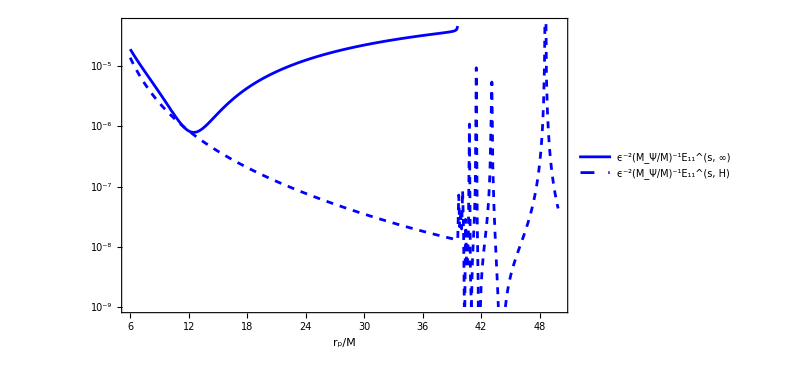

$Aborted

```mathematica
ListLogPlot[{tabμ02l1[[1;;-2,{1,2}]],tabμ02l1[[1;;-2,{1,3}]]},Joined->True,Frame->True,FrameStyle->Directive[GrayLevel[0],20,Italic(*,FontFamily->"Times New Roman"*),AbsoluteThickness[2]],FrameLabel->{{None,None},{"r_p/M",None}},ImageSize->600,PlotRange->{{6,50},{10^-9,5*10^-5}},PlotStyle->{Blue,{Blue,Dashed}},PlotLegends->Placed[{Style["ϵ^-2(M_Ψ/M)^-1E_11^(s, ∞)",20,Italic],Style["ϵ^-2(M_Ψ/M)^-1E_11^(s, H)",20,Italic]},{0.25,0.15}]]
```